## Thorough comparison to fn_cross old and new to qlanth

```mathematica
AppendTo[$Path,NotebookDirectory[]];
SetDirectory[NotebookDirectory[]];
Get["qlanth.m"];
Get["qplotter.m"];
Get["misc.m"];
```

### All together

```mathematica
Dynamic[Framed[{vintage,workingon,numE}]]
```

```mathematica
numEmax=7;
Tsubset={T2,T3,T4,T6,T7,T8};
LoadThreeBody[];
LoadElectrostatic[];
LoadSOOandECSOLS[];
LoadV1k[];
LoadUk[];
LoadCFP[];

Do[
(
fncrossReidfname=FileNameJoin[{NotebookDirectory[],"data",<|"old"->"fncross_old.m","new"->"fncross.m"|>[vintage]}];
fncrossReid=Import[fncrossReidfname];
allTerms=fncrossReid["terms"];
headers=<||>;

workingon="E-S";
EScomparison={};
ESparams={F2,F4,F6,α,β,γ,T2,T3,T4,T6,T7,T8};
Do[
terms=allTerms[numE];
extraα=<|
1->0.012,
2->0.022154,
3->0.030462,
4->0.036923,
5->0.041538,
6->0.044308,
7->0.045231|>[numE];
extraβ=<|
1->0.5,
2->0.923077,
3->1.269231,
4->1.538462,
5->1.730769,
6->1.8461530000000002,
7->1.8846154201680647
|>[numE];
extraγ=<|
1->0.6,
2->1.107692,
3->1.523077,
4->1.846154,
5->2.076923,
6->2.2153840000000002,
7->2.26153874789916
|>[numE];
Do[(
braTerm=terms[[braTermIndex]];
ketTerm=terms[[ketTermIndex]];
{braS,braL}=FindSL[braTerm];
{ketS,ketL}=FindSL[ketTerm];
ourSlaters=N@Coefficient[ElectrostaticTable[{numE,braTerm,ketTerm}],{F2,F4,F6}];
casimirOps=If[
braTerm==ketTerm,
{(braL*(braL+1)),
CasimirG2[{braTerm,ketTerm}]/.{β->1},
CasimirSO7[{braTerm,ketTerm}]/.{γ->1}},
{0,0,0}
];
ourTees=N@Coefficient[ThreeBodyTable[{numE,braTerm,ketTerm}],Tsubset]/.{t2Switch->1};
crossed=fncrossReid["E-S"][#][{numE,braTerm,ketTerm}]&/@ESparams;
crossed[[4]]=1000*(crossed[[4]]+extraα);
crossed[[5]]=crossed[[5]]+extraβ;
crossed[[6]]=crossed[[6]]+extraγ;
crossed=If[FreeQ[#,Missing],#,0.]&/@crossed;
ours=N@Join[ourSlaters,casimirOps,ourTees];
combos=Transpose[{ours,crossed}];
combos=MapIndexed[{numE,ESparams[[#2[[1]]]],braTerm,ketTerm,#1[[1]],#1[[2]],Abs@Chop[#1[[1]]-#1[[2]]]}&,combos];
EScomparison=Append[EScomparison,combos];
),
{braTermIndex,1,Length[terms]},
{ketTermIndex,braTermIndex,Length[terms]}],
{numE,2,numEmax}
];
EScomparison=Flatten[EScomparison,1];
headers["E-S"]={"n","op","bTerm","kTerm","ql","fncross","|ql-fncross|"};

workingon="MkPk";
MkPkcomparison={};
MkPkParams={M0,M2,M4,P2,P4,P6};
Prescaling={P2->P2/225,P4->P4/1089,P6->25*P6/184041};
Do[
terms=allTerms[numE];
Do[(
{braS,braL}=FindSL[braTerm];
{ketS,ketL}=FindSL[ketTerm];
ourMsAndPs=N@Coefficient[SOOandECSOLSTable[{numE,braTerm,ketTerm}]/.Prescaling,MkPkParams];
crossed=fncrossReid["MKPK"][#][{numE,braTerm,ketTerm}]&/@MkPkParams;
switched="N";
If[Not[FreeQ[crossed,Missing]],
(
phase=Phaser[braL-ketL+braS-ketS];
crossed=phase*fncrossReid["MKPK"][#][{numE,ketTerm,braTerm}]&/@MkPkParams;
switched="Y";
)
];
If[Not[FreeQ[crossed,Missing]],
crossed=ConstantArray[0.,Length[MkPkParams]];
];
crossed=If[FreeQ[#,Missing],#,0.]&/@crossed;
combos=Transpose[{ourMsAndPs,crossed}];
combos=MapIndexed[{numE,MkPkParams[[#2[[1]]]],switched,braTerm,ketTerm,#1[[1]],#1[[2]],Abs@Chop[#1[[1]]-#1[[2]]]}&,combos];
MkPkcomparison=Append[MkPkcomparison,combos];
),
{braTerm,terms},
{ketTerm,terms}
],
{numE,2,numEmax}
];
MkPkcomparison=Flatten[MkPkcomparison,1];
headers["MkPk"]={"n","op","switched","bTerm","kTerm","ql","fncross","|ql-fncross|"};

workingon="V1k";
V1kcomparison={};
V1ks={1};
Do[
terms=allTerms[numE];
Do[(
{braS,braL}=FindSL[braTerm];
{ketS,ketL}=FindSL[ketTerm];
ourV1k=N@Map[ReducedV1kTable[{numE,braTerm,ketTerm,#}]&,V1ks];
crossed=fncrossReid["V1K"][#][{numE,braTerm,ketTerm}]&/@V1ks;
switched="N";
If[Not[FreeQ[crossed,Missing]],
(
phase=Phaser[braL-ketL+braS-ketS];
crossed=phase*fncrossReid["V1K"][#][{numE,ketTerm,braTerm}]&/@V1ks;
switched="Y";
)
];
If[Not[FreeQ[crossed,Missing]],
crossed={0.};
];
combos=Transpose[{ourV1k,crossed}];
combos=MapIndexed[{numE,V1ks[[#2[[1]]]],switched,braTerm,ketTerm,#1[[1]],#1[[2]],Abs@Chop[#1[[1]]-#1[[2]]]}&,combos];
V1kcomparison=Append[V1kcomparison,combos];
),
{braTerm,terms},
{ketTerm,terms}],
{numE,2,numEmax}
];
V1kcomparison=Flatten[V1kcomparison,1];
headers["V1k"]={"n","op","switched","bTerm","kTerm","ql","fncross","|ql-fncross|"};

workingon="UK";
Ukcomparison={};
Uks={0,2,4,6};
Do[
terms=allTerms[numE];
Do[(
{braS,braL}=FindSL[braTerm];
{ketS,ketL}=FindSL[ketTerm];
ourUks=N@Map[ReducedUkTable[{numE,3,braTerm,ketTerm,#}]&,Uks];
crossed=fncrossReid["UK"][#][{numE,braTerm,ketTerm}]&/@Uks;
switched="N";
If[Not[FreeQ[crossed,Missing]],
(
phase=Phaser[braL-ketL+braS-ketS];
crossed=phase*fncrossReid["UK"][#][{numE,ketTerm,braTerm}]&/@Uks;
switched="Y";
)
];
If[Not[FreeQ[crossed,Missing]],
crossed=ConstantArray[0.,Length[Uks]];
];
crossed=If[FreeQ[#,Missing],#,0.]&/@crossed;
combos=Transpose[{ourUks,crossed}];
combos=MapIndexed[{numE,"U"<>ToString[#2[[1]]],switched,braTerm,ketTerm,#1[[1]],#1[[2]],Abs@Chop[#1[[1]]-#1[[2]]]}&,combos];
Ukcomparison=Append[Ukcomparison,combos];
),
{braTerm,terms},
{ketTerm,terms}],
{numE,2,numEmax}
];
Ukcomparison=Flatten[Ukcomparison,1];
headers["Uk"]={"n","op","switched","bTerm","kTerm","ql","fncross","|ql-fncross|"};

workingon="CFP";
CFPcomparison={};
Do[
terms=allTerms[numE];
Do[(
ours=SortBy[Rest@CFP[{numE,term}],First];
ours=Select[ours,#[[2]]=!=0&];
combos=Prepend[#[[{1,2,4}]],term]&/@(Flatten/@Transpose[{ours,
SortBy[Rest@fncrossReid["CFP"][{numE,term}],First]}]);
combos=Append[#,Abs[#[[-2]]-#[[-1]]]]&/@combos;
combos=Prepend[#,numE]&/@combos;
CFPcomparison=Append[CFPcomparison,N/@combos];
),
{term,terms}
],
{numE,2,numEmax}
];
CFPcomparison=Flatten[CFPcomparison,1];
headers["CFP"]={"n","bTerm","kTerm","ql","fncross","|ql-fncross|"};

comparison=<|
"CFP"->CFPcomparison,
"Uk"->Ukcomparison,
"V1k"->V1kcomparison,
"MkPk"->MkPkcomparison,
"E-S"->EScomparison
|>;

Print[Map[Max[Last/@#]&,comparison]];
exportFname=FileNameJoin[{NotebookDirectory[],"tableComparisons","ql_vs_fncross_"<>vintage<>".mx"}];
Export[exportFname,comparison];

KeyValueMap[Export[FileNameJoin[{NotebookDirectory[],"tableComparisons","ql_vs_fncross_"<>vintage<>"_"<>#1<>"_table.csv"}],Prepend[#2,headers[#1]]]&,comparison];
),
{vintage,{"old","new"}}
]
```

<|CFP→5.49899×10^-10,Uk→0.000106766,V1k→0.000069,MkPk→119.521,E-S→11.4742|>

<|CFP→5.49899×10^-10,Uk→0.000106766,V1k→0.000069,MkPk→0.000270977,E-S→11.4742|>

### Electrostatic

```mathematica
fncrossReidfname=FileNameJoin[{NotebookDirectory[],"data","fncross_old.m"}];
fncrossReid=Import[fncrossReidfname];
allTerms=fncrossReid["terms"];
Tsubset={T2,T3,T4,T6,T7,T8};
```

```mathematica
LoadThreeBody[];
LoadElectrostatic[];
```

α

{{1,0.0119999},{2,0.0221536},{3,0.0304613},{4,0.0369228},{5,0.0415382},{6,0.0443075},{7,0.0452307}}

0.0452307+1.07143×10^-7 x-0.00092306 x^2

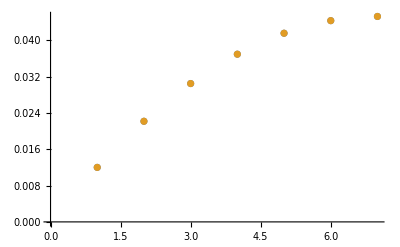

{5.48534×10^-13,{a→0.0452308,b→-0.000923076}}

```mathematica
α
fixes={#[[1]],#[[2]]}&/@Normal[<|
1->0.012,
2->0.022154,
3->0.030462,
4->0.036923,
5->0.041538,
6->0.044308,
7->0.045231|>];
formula=FindFormula[fixes];
formulaValues={#,formula[#]}&/@Range[1,7]
Print[Expand@formula[x+7]]
ListPlot[{fixes,formulaValues}]
FindMinimum[Expand[Total@(((Last/@fixes)-Last/@({#,a+b (#-7)^2}&/@Range[1,7]))^2)],{a,b}]
```

β

{{1,0.5},{2,0.923077},{3,1.26923},{4,1.53846},{5,1.73077},{6,1.84615},{7,1.88461}}

1.88461-1.97779×10^-7 x-0.0384616 x^2

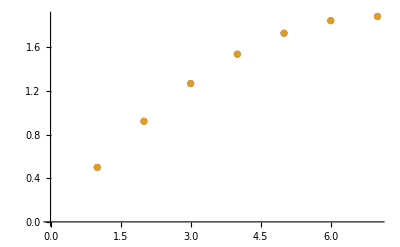

{9.09939×10^-13,{a→1.88462,b→-0.0384615}}

```mathematica
β
fixes={#[[1]],#[[2]]}&/@Normal[<|
1->0.5,
2->0.923077,
3->1.269231,
4->1.538462,
5->1.730769,
6->1.8461530000000002,
7->1.8846154201680647
|>];
formula=FindFormula[fixes];
formulaValues={#,formula[#]}&/@Range[1,7]
Print[Expand@formula[x+7]]
ListPlot[{fixes,formulaValues}]
FindMinimum[Expand[Total@(((Last/@fixes)-Last/@({#,a+b (#-7)^2}&/@Range[1,7]))^2)],{a,b}]
```

γ

{{1,0.6},{2,1.10769},{3,1.52308},{4,1.84615},{5,2.07692},{6,2.21538},{7,2.26154}}

2.26154+6.15246×10^-8 x-0.0461538 x^2

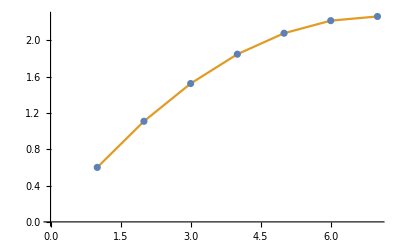

{5.45342×10^-13,{a→2.26154,b→-0.0461538}}

```mathematica
γ
fixes={#[[1]],#[[2]]}&/@Normal[<|
1->0.6,
2->1.107692,
3->1.523077,
4->1.846154,
5->2.076923,
6->2.2153840000000002,
7->2.26153874789916
|>];
formula=FindFormula[fixes];
formulaValues={#,formula[#]}&/@Range[1,7]
Print[Expand@formula[x+7]]
ListPlot[{fixes,formulaValues},Joined->{False,True}]
FindMinimum[Expand[Total@(((Last/@fixes)-Last/@({#,a+b (#-7)^2}&/@Range[1,7]))^2)],{a,b}]
```

```mathematica
EScomparison={};
ESparams={F2,F4,F6,α,β,γ,T2,T3,T4,T6,T7,T8};
Do[
terms=allTerms[numE];
extraα=<|
1->0.012,
2->0.022154,
3->0.030462,
4->0.036923,
5->0.041538,
6->0.044308,
7->0.045231|>[numE];
extraβ=<|
1->0.5,
2->0.923077,
3->1.269231,
4->1.538462,
5->1.730769,
6->1.8461530000000002,
7->1.8846154201680647
|>[numE];
extraγ=<|
1->0.6,
2->1.107692,
3->1.523077,
4->1.846154,
5->2.076923,
6->2.2153840000000002,
7->2.26153874789916
|>[numE];
Do[(
braTerm=terms[[braTermIndex]];
ketTerm=terms[[ketTermIndex]];
{braS,braL}=FindSL[braTerm];
{ketS,ketL}=FindSL[ketTerm];
ourSlaters=N@Coefficient[ElectrostaticTable[{numE,braTerm,ketTerm}],{F2,F4,F6}];
casimirOps=If[
braTerm==ketTerm,
{(braL*(braL+1)),
CasimirG2[{braTerm,ketTerm}]/.{β->1},
CasimirSO7[{braTerm,ketTerm}]/.{γ->1}},
{0,0,0}
];
ourTees=N@Coefficient[ThreeBodyTable[{numE,braTerm,ketTerm}],Tsubset]/.{t2Switch->1};
crossed=fncrossReid["E-S"][#][{numE,braTerm,ketTerm}]&/@ESparams;
crossed[[4]]=1000*(crossed[[4]]+extraα);
crossed[[5]]=crossed[[5]]+extraβ;
crossed[[6]]=crossed[[6]]+extraγ;
crossed=If[FreeQ[#,Missing],#,0.]&/@crossed;
ours=N@Join[ourSlaters,casimirOps,ourTees];
combos=Transpose[{ours,crossed}];
combos=MapIndexed[{numE,ESparams[[#2[[1]]]],braTerm,ketTerm,#1[[1]],#1[[2]],Abs@Chop[#1[[1]]-#1[[2]]]}&,combos];
EScomparison=Append[EScomparison,combos];
),
{braTermIndex,1,Length[terms]},
{ketTermIndex,braTermIndex,Length[terms]}],
{numE,2,7}
];
EScomparison=Flatten[EScomparison,1];
```

```mathematica
EScomparisonFiltered=Select[EScomparison,#[[-1]]>10^-4&];
EScomparisonFiltered=ReverseSortBy[EScomparisonFiltered,Last];
```

```mathematica
tab=TableForm[SortBy[EScomparisonFiltered,First],TableHeadings->{None,{"n","op","<bT|","|kT>","ql","cross","|Δ|"}}]
```

n | op | <bT| | |kT> | ql | cross | |Δ|
3 | T7 | 2L | 2L | -0.0265033 | -0.026053 | 0.000450256
6 | T2 | 1S2 | 1S3 | -0.44825 | 0.448249 | 0.896499
6 | T3 | 1S1 | 1S3 | 5.7371 | -5.7371 | 11.4742
6 | T4 | 1Q | 1Q | -0.856893 | 0. | 0.856893
6 | T4 | 1S3 | 1S4 | 0.29277 | -0.29277 | 0.58554
6 | T6 | 1S2 | 1S3 | 3.55842 | -3.55842 | 7.11683
6 | T7 | 1S3 | 1S4 | -2.53546 | 2.53546 | 5.07093
7 | T2 | 2F2 | 2F3 | 0.23597 | 0.196756 | 0.039214
7 | T2 | 2F2 | 2F8 | -0.410326 | -0.359701 | 0.0506249
7 | T2 | 2F3 | 2F4 | -0.793039 | -0.813518 | 0.0204786
7 | T2 | 2F3 | 2F6 | -0.699854 | -0.635095 | 0.0647592
7 | T2 | 2F4 | 2F8 | 0.25 | 0.276438 | 0.026438
7 | T2 | 2F6 | 2F8 | 0. | -0.083604 | 0.083604
7 | T3 | 2F1 | 2F8 | -4.53557 | -3.2397 | 1.29588
7 | T4 | 2F3 | 2F10 | -0.358569 | -0.32015 | 0.0384186
7 | T4 | 2F3 | 2F9 | 0.478091 | 0.490897 | 0.0128056
7 | T4 | 2F5 | 2F8 | -0.377964 | -0.357716 | 0.0202485
7 | T4 | 2F7 | 2F8 | 0. | 0.035071 | 0.035071
7 | T6 | 2F2 | 2F3 | -1.45272 | -1.14142 | 0.311297
7 | T6 | 2F4 | 2F8 | 0. | -0.209876 | 0.209876
7 | T6 | 2F6 | 2F8 | -2.72554 | -2.06185 | 0.663688
7 | T7 | 2F3 | 2F10 | 1.72516 | 1.39245 | 0.332711
7 | T7 | 2F3 | 2F9 | 0. | -0.110903 | 0.110903
7 | T7 | 2F5 | 2F8 | 0. | -0.175354 | 0.175354
7 | T7 | 2F7 | 2F8 | 1.88982 | 1.5861 | 0.303722

### Marvin and Pseudo-Magnetic

```mathematica
fncrossReidfname=FileNameJoin[{NotebookDirectory[],"data","fncross_old.m"}];
fncrossReid=Import[fncrossReidfname];
allTerms=fncrossReid["terms"];
Tsubset={T2,T3,T4,T6,T7,T8};
```

```mathematica
MkPkcomparison={};
MkPkParams={M0,M2,M4,P2,P4,P6};
Prescaling={P2->P2/225,P4->P4/1089,P6->25*P6/184041};
Do[
terms=allTerms[numE];
Do[(
{braS,braL}=FindSL[braTerm];
{ketS,ketL}=FindSL[ketTerm];
ourMsAndPs=N@Coefficient[qlanth`Private`SOOandECSOLSTable[{numE,braTerm,ketTerm}]/.Prescaling,MkPkParams];
crossed=fncrossReid["MKPK"][#][{numE,braTerm,ketTerm}]&/@MkPkParams;
combos=Transpose[{ourMsAndPs,crossed}];
combos=MapIndexed[{numE,MkPkParams[[#2[[1]]]],braTerm,ketTerm,#1[[1]],#1[[2]],Abs@Chop[#1[[1]]-#1[[2]]]}&,combos];
MkPkcomparison=Append[MkPkcomparison,combos];
),
{braTerm,terms},
{ketTerm,terms}
],
{numE,2,7}
];
MkPkcomparison=Flatten[MkPkcomparison,1];
```

```mathematica
MkPkcomparisonFiltered=Select[MkPkcomparison,#[[-1]]>10^-5&];
MkPkcomparisonFiltered=ReverseSortBy[MkPkcomparisonFiltered,Last];
tab=TableForm[SortBy[MkPkcomparisonFiltered,First],TableHeadings->{None,{"n","op","<bT|","|kT>","ql","cross","|Δ|"}}]
Export["~/Temp/MandPcomparison-old.pdf",tab]
```

n | op | <bT| | |kT> | ql | cross | |Δ|
2 | M0 | 3H | 1I | -39.5174 | -41.0046 | 1.48721
2 | M2 | 3H | 1I | -12.6317 | 0.7082 | 13.3399
2 | M2 | 3P | 3P | -72.5 | -72.5 | 0.000015
2 | M4 | 3H | 1I | -0.636162 | -8.03127 | 7.3951
2 | M4 | 3P | 3P | -82.0455 | -82.0454 | 0.0000135455
2 | P2 | 3H | 1I | 0.0991476 | -0.21482 | 0.313968
2 | P4 | 3H | 1I | -0.00409701 | 0.166612 | 0.170709
2 | P6 | 3H | 1I | 0.0103031 | -0.035657 | 0.0459601
3 | M0 | 4G | 4G | -198.031 | -198.031 | 0.000010332
3 | M0 | 4I | 2I | -49.2905 | -61.3551 | 12.0645
3 | M0 | 4I | 2K | 70.2301 | -49.2905 | 119.521
3 | M0 | 4I | 2L | 0. | 70.2301 | 70.2301
3 | M0 | 4I | 4I | -311.717 | -311.717 | 0.000015666
3 | M2 | 2F2 | 2G2 | -64.1013 | -64.1013 | 0.0000136966
3 | M2 | 2G2 | 2G2 | -56.4311 | -56.4311 | 0.000012639
3 | M2 | 4D | 4D | 85.3242 | 85.3242 | 0.0000172632
3 | M2 | 4G | 4G | -62.8787 | -62.8787 | 0.0000149536
3 | M2 | 4I | 2I | -16.6877 | 13.9612 | 30.6489
3 | M2 | 4I | 2K | 17.182 | -16.6877 | 33.8697
3 | M2 | 4I | 2L | 0. | 17.182 | 17.182
3 | M4 | 2G2 | 2G2 | -69.2609 | -69.2609 | 0.0000136938
3 | M4 | 4D | 4D | 91.4953 | 91.4953 | 0.0000149899
3 | M4 | 4G | 4G | -77.322 | -77.322 | 0.000013663
3 | M4 | 4I | 2I | 4.23027 | 17.3951 | 13.1648
3 | M4 | 4I | 2K | 15.2063 | 4.23027 | 10.976
3 | M4 | 4I | 2L | 0. | 15.2063 | 15.2063
3 | P2 | 4I | 2I | -0.207738 | -0.409034 | 0.201296
3 | P2 | 4I | 2K | 0.22951 | -0.207738 | 0.437248
3 | P2 | 4I | 2L | 0. | 0.22951 | 0.22951
3 | P4 | 4I | 2I | -0.0405799 | -0.033292 | 0.00728789
3 | P4 | 4I | 2K | -0.0924679 | -0.04058 | 0.0518879
3 | P4 | 4I | 2L | 0. | -0.092468 | 0.092468
3 | P6 | 4I | 2I | 0.10586 | 0.167067 | 0.0612074
3 | P6 | 4I | 2K | 0.0049103 | 0.10586 | 0.10095
3 | P6 | 4I | 2L | 0. | 0.00491 | 0.00491
4 | M0 | 3H1 | 3H1 | -146.692 | -146.692 | 0.0000100748
4 | M0 | 3H2 | 3H2 | -230.627 | -230.627 | 0.0000115076
4 | M0 | 3I1 | 3I1 | -287.204 | -287.204 | 0.0000141409
4 | M0 | 3I2 | 3I2 | -238.258 | -238.258 | 0.0000129729
4 | M0 | 3K1 | 3K1 | -296.212 | -296.212 | 0.0000143781
4 | M0 | 3K2 | 3K2 | -306.34 | -306.34 | 0.0000155306
4 | M0 | 3L | 3L | -338.623 | -338.623 | 0.0000163201
4 | M0 | 3M | 3M | -431.615 | -431.615 | 0.0000207792
4 | M0 | 5G | 5G | -282.916 | -282.916 | 0.0000142915
4 | M0 | 5I | 5I | -527.936 | -527.936 | 0.0000269406
4 | M2 | 3D2 | 3F4 | -47.3728 | -47.3728 | 0.0000117343
4 | M2 | 3F3 | 1D3 | -45.057 | -45.057 | 0.000010071
4 | M2 | 3G2 | 1G3 | -40.0245 | -40.0245 | 0.0000114664
4 | M2 | 3G3 | 1H2 | -67.9775 | -67.9775 | 0.0000155021
4 | M2 | 3H3 | 3H4 | 69.0157 | 69.0157 | 0.0000177274
4 | M2 | 3H4 | 1I3 | 44.7371 | 44.7371 | 0.0000109356
4 | M2 | 3I2 | 1H2 | -68.0823 | -68.0823 | 0.0000161866
4 | M2 | 3I2 | 1I3 | -81.0221 | -81.0221 | 0.0000177494
4 | M2 | 3K1 | 3K2 | -57.0006 | -57.0006 | 0.0000142281
4 | M2 | 3P1 | 3P1 | -53.3 | -53.3 | 0.000013
4 | M2 | 3P3 | 1D4 | 53.7834 | 53.7834 | 0.0000124576
4 | M2 | 3P3 | 1S2 | 52.3573 | 52.3573 | 0.0000122015
4 | M2 | 5D | 3P3 | 52.6887 | 52.6887 | 0.0000102515
4 | M2 | 5D | 5D | -81.75 | -81.75 | 0.000018
4 | M2 | 5G | 3G3 | -48.8462 | -48.8462 | 0.0000100627
4 | M2 | 5G | 3H4 | 54.18 | 54.18 | 0.0000118075
4 | M2 | 5G | 5G | 88.126 | 88.1259 | 0.0000165188
4 | M2 | 5I | 3H4 | 30.3965 | 30.3965 | 0.0000116465
4 | M2 | 5I | 3I2 | 59.0011 | 59.0011 | 0.0000110671
4 | M4 | 3F1 | 3F4 | 29.6648 | 29.6648 | 0.0000131991
4 | M4 | 3F4 | 3G3 | -30.2736 | -30.2736 | 0.0000112733
4 | M4 | 3G2 | 1G1 | 22.0257 | 22.0256 | 0.0000103497
4 | M4 | 3G3 | 1H2 | -84.7307 | -84.7307 | 0.0000121242
4 | M4 | 3H1 | 1G4 | 25.3819 | 25.3819 | 0.0000110094
4 | M4 | 3H1 | 1I3 | 27.3901 | 27.3901 | 0.0000120903
4 | M4 | 3H1 | 3H3 | 26.533 | 26.533 | 0.0000114415
4 | M4 | 3H4 | 3H4 | 32.2127 | 32.2127 | 0.0000111434
4 | M4 | 3I2 | 1H2 | -84.795 | -84.7949 | 0.0000109231
4 | M4 | 3I2 | 1I3 | -91.3178 | -91.3178 | 0.0000127907
4 | M4 | 3K2 | 3K2 | -23.3969 | -23.3969 | 0.0000127314
4 | M4 | 5D | 5D | -93.0682 | -93.0682 | 0.0000158182
4 | M4 | 5G | 3H1 | 26.0119 | 26.0119 | 0.0000117357
4 | M4 | 5G | 5G | 91.7546 | 91.7546 | 0.00001477
4 | M4 | 5I | 3H1 | 24.5728 | 24.5728 | 0.000011181
5 | M0 | 2F6 | 2G2 | -6.40502 | -4.80846 | 1.59656
5 | M0 | 2F6 | 2G4 | 8.01237 | 10.3405 | 2.32816
5 | M0 | 2F7 | 2G2 | 9.37041 | 7.77385 | 1.59656
5 | M0 | 2F7 | 2G4 | -11.8586 | -14.1868 | 2.32815
5 | M0 | 2G4 | 2G4 | -72.7689 | -76.9495 | 4.18065
5 | M0 | 2G4 | 2G5 | 0.0698212 | 4.25047 | 4.18065
5 | M0 | 2H4 | 2I2 | 7.4162 | 7.40787 | 0.00832449
5 | M0 | 2L2 | 2L2 | -232.728 | -232.728 | 0.0000107837
5 | M0 | 2L3 | 2L3 | -229.918 | -229.918 | 0.0000105787
5 | M0 | 2M2 | 2M2 | -275.326 | -275.326 | 0.0000138787
5 | M0 | 2N | 2N | -273.416 | -273.416 | 0.0000142625
5 | M0 | 2O | 2O | -327.192 | -327.192 | 0.0000152131
5 | M0 | 4F1 | 4F1 | -163.678 | -163.678 | 0.0000103324
5 | M0 | 4G1 | 4G1 | -223.435 | -223.435 | 0.0000121764
5 | M0 | 4G2 | 4G2 | -217.166 | -217.166 | 0.0000108252
5 | M0 | 4G3 | 4G3 | -205.916 | -205.916 | 0.000011437
5 | M0 | 4G4 | 4G4 | -239.716 | -239.716 | 0.0000117675
5 | M0 | 4H1 | 4H1 | -285.577 | -285.577 | 0.0000131324
5 | M0 | 4H2 | 4H2 | -325.272 | -325.272 | 0.0000159886
5 | M0 | 4H3 | 4H3 | -322.44 | -322.44 | 0.0000166225
5 | M0 | 4I1 | 4I1 | -367.022 | -367.022 | 0.000022139
5 | M0 | 4I2 | 4I2 | -397.188 | -397.188 | 0.000018397
5 | M0 | 4I3 | 4I3 | -392.64 | -392.639 | 0.0000210247
5 | M0 | 4K1 | 4K1 | -498.056 | -498.056 | 0.0000241506
5 | M0 | 4K2 | 4K2 | -490.81 | -490.81 | 0.0000249254
5 | M0 | 4L | 4L | -607.237 | -607.237 | 0.0000295187
5 | M0 | 4M | 4M | -752.141 | -752.141 | 0.0000367542
5 | M0 | 6F | 6F | -247.923 | -247.923 | 0.0000115572
5 | M0 | 6H | 6H | -586.168 | -586.168 | 0.0000300778
5 | M2 | 2D5 | 2D5 | 50.3885 | 50.3885 | 0.0000140797
5 | M2 | 2F2 | 2G2 | -51.281 | -51.281 | 0.0000115573
5 | M2 | 2F6 | 2F7 | -58.7749 | -58.7749 | 0.0000152497
5 | M2 | 2F6 | 2G2 | 6.47935 | 13.6397 | 7.16031
5 | M2 | 2F6 | 2G4 | -9.56379 | 8.95768 | 18.5215
5 | M2 | 2F7 | 2G2 | 7.43308 | 0.272767 | 7.16031
5 | M2 | 2F7 | 2G4 | 12.5178 | -6.00369 | 18.5215
5 | M2 | 2G2 | 2G2 | -33.7241 | -33.7241 | 0.0000103264
5 | M2 | 2G4 | 2G4 | 41.6279 | 49.0427 | 7.41478
5 | M2 | 2G4 | 2G5 | 5.70159 | -1.71319 | 7.41479
5 | M2 | 2G6 | 2H7 | -59.1835 | -59.1835 | 0.0000154985
5 | M2 | 2H4 | 2H5 | -53.5687 | -53.5687 | 0.0000124992
5 | M2 | 2H4 | 2I2 | -30.0802 | -30.1175 | 0.037325
5 | M2 | 2H6 | 2I4 | 40.9495 | 40.9495 | 0.0000112873
5 | M2 | 2H6 | 2I5 | -38.1 | -38.1 | 0.0000110298
5 | M2 | 2I4 | 2K4 | 37.7595 | 37.7595 | 0.000010371
5 | M2 | 2K2 | 2K3 | 42.0887 | 42.0887 | 0.0000103799
5 | M2 | 2K4 | 2K4 | 63.2215 | 63.2215 | 0.0000160307
5 | M2 | 2K5 | 2K5 | 57.4137 | 57.4137 | 0.0000153005
5 | M2 | 2L2 | 2M2 | -62.9364 | -62.9364 | 0.0000110035
5 | M2 | 2L3 | 2L3 | -54.5044 | -54.5044 | 0.00001655
5 | M2 | 2M2 | 2M2 | -64.634 | -64.634 | 0.000017297
5 | M2 | 4D1 | 4D1 | 57.2756 | 57.2756 | 0.0000142761
5 | M2 | 4D2 | 2F4 | -61.5665 | -61.5665 | 0.0000117536
5 | M2 | 4D3 | 2D5 | -49.9575 | -49.9575 | 0.0000109952
5 | M2 | 4F3 | 2F7 | -46.626 | -46.6259 | 0.0000101441
5 | M2 | 4F4 | 2F6 | -104.889 | -104.889 | 0.0000237948
5 | M2 | 4F4 | 2G6 | 62.1439 | 62.1439 | 0.00001452
5 | M2 | 4G1 | 4G1 | -40.9569 | -40.9569 | 0.0000121871
5 | M2 | 4G2 | 2F4 | -58.0549 | -58.0549 | 0.0000106353
5 | M2 | 4G2 | 2G4 | 56.0425 | 56.0425 | 0.000011032
5 | M2 | 4G3 | 2G4 | 37.2154 | 37.2154 | 0.0000113597
5 | M2 | 4G3 | 2H6 | 59.4256 | 59.4256 | 0.0000138353
5 | M2 | 4G3 | 4G3 | 37.2217 | 37.2217 | 0.0000112118
5 | M2 | 4G4 | 2H7 | -48.4612 | -48.4611 | 0.0000116377
5 | M2 | 4G4 | 4G4 | -52.9576 | -52.9576 | 0.0000152369
5 | M2 | 4H2 | 2H5 | 36.2296 | 36.2296 | 0.000010995
5 | M2 | 4H2 | 4H3 | -60.4331 | -60.4331 | 0.0000138679
5 | M2 | 4H3 | 2G6 | 55.4491 | 55.4491 | 0.0000103721
5 | M2 | 4H3 | 2I5 | -66.7453 | -66.7453 | 0.0000161466
5 | M2 | 4I1 | 2H2 | 50.3179 | 50.3179 | 0.0000101514
5 | M2 | 4I1 | 2K1 | 43.7373 | 43.7373 | 0.0000100814
5 | M2 | 4I2 | 2K5 | 53.2803 | 53.2803 | 0.0000102751
5 | M2 | 4I3 | 4I3 | 85.4056 | 85.4056 | 0.0000189123
5 | M2 | 4K1 | 2K5 | -63.7402 | -63.7402 | 0.0000120361
5 | M2 | 4K1 | 4K2 | 52.0623 | 52.0623 | 0.0000112731
5 | M2 | 4K2 | 2I5 | -63.54 | -63.5399 | 0.0000175678
5 | M2 | 4K2 | 2K5 | 81.1702 | 81.1702 | 0.0000193151
5 | M2 | 4L | 2L3 | -60.3747 | -60.3747 | 0.0000140333
5 | M2 | 4P1 | 2P2 | 56.3158 | 56.3158 | 0.0000131
5 | M2 | 4P2 | 4P2 | 50.3068 | 50.3068 | 0.0000122955
5 | M2 | 6F | 4F4 | 84.6094 | 84.6094 | 0.0000140242
5 | M2 | 6H | 4G4 | 45.7841 | 45.7841 | 0.0000138633
5 | M2 | 6H | 4H2 | 47.2981 | 47.2981 | 0.0000112302
5 | M2 | 6H | 4I3 | 47.4414 | 47.4414 | 0.0000138698
5 | M2 | 6P | 6P | 89.9244 | 89.9244 | 0.0000177031
5 | M4 | 2F1 | 2G6 | -23.7848 | -23.7847 | 0.000011018
5 | M4 | 2F6 | 2G2 | 7.17613 | 15.1149 | 7.93879
5 | M4 | 2F6 | 2G4 | -23.9734 | -17.614 | 6.35946
5 | M4 | 2F7 | 2G2 | 8.24876 | 0.309962 | 7.9388
5 | M4 | 2F7 | 2G4 | 8.65851 | 2.29905 | 6.35946
5 | M4 | 2G2 | 2H6 | -24.7447 | -24.7447 | 0.0000112708
5 | M4 | 2G4 | 2G4 | 45.5838 | 55.3167 | 9.73293
5 | M4 | 2G4 | 2G5 | 9.30314 | -0.429796 | 9.73294
5 | M4 | 2H1 | 2H4 | -23.19 | -23.19 | 0.0000101523
5 | M4 | 2H4 | 2I2 | -20.5322 | -20.5735 | 0.0413844
5 | M4 | 2I1 | 2I4 | -26.3788 | -26.3788 | 0.0000118286
5 | M4 | 2K1 | 2K5 | 28.1225 | 28.1225 | 0.0000121497
5 | M4 | 2L1 | 2L3 | 26.5999 | 26.5999 | 0.0000117384
5 | M4 | 2M2 | 2M2 | -93.4691 | -93.4691 | 0.0000148507
5 | M4 | 4F3 | 2F2 | 23.0547 | 23.0546 | 0.0000106256
5 | M4 | 4F4 | 2F1 | 34.254 | 34.2539 | 0.0000149873
5 | M4 | 4F4 | 2F6 | -128.249 | -128.249 | 0.0000165074
5 | M4 | 4G1 | 2F7 | 24.353 | 24.353 | 0.0000110353
5 | M4 | 4G1 | 4G4 | 28.6514 | 28.6514 | 0.0000127099
5 | M4 | 4G1 | 4H3 | -27.7034 | -27.7034 | 0.0000120392
5 | M4 | 4G3 | 2H2 | -26.1985 | -26.1985 | 0.0000112716
5 | M4 | 4H2 | 4H3 | -73.6601 | -73.66 | 0.0000124245
5 | M4 | 4H3 | 2G6 | 55.7689 | 55.7689 | 0.0000113625
5 | M4 | 4H3 | 2H2 | -23.8297 | -23.8297 | 0.0000111781
5 | M4 | 4H3 | 2I5 | -86.4592 | -86.4592 | 0.0000101729
5 | M4 | 4I1 | 2H6 | 28.6638 | 28.6638 | 0.0000130454
5 | M4 | 4I1 | 2K5 | 36.7119 | 36.7119 | 0.0000169465
5 | M4 | 4I1 | 4I3 | -32.0678 | -32.0677 | 0.000014028
5 | M4 | 4K1 | 2K1 | -34.2245 | -34.2245 | 0.0000158607
5 | M4 | 4K1 | 4K2 | 68.6595 | 68.6595 | 0.0000104131
5 | M4 | 4K2 | 2K4 | 54.2027 | 54.2027 | 0.0000108762
5 | M4 | 4K2 | 2K5 | 98.813 | 98.813 | 0.0000119431
5 | M4 | 4M | 2M2 | 38.184 | 38.184 | 0.0000100051
5 | M4 | 4P2 | 4D1 | 29.4119 | 29.4118 | 0.0000127557
5 | M4 | 6F | 4F4 | 56.4489 | 56.4489 | 0.0000111899
5 | M4 | 6H | 4G1 | -33.2954 | -33.2954 | 0.0000152732
5 | M4 | 6H | 4H2 | 67.1971 | 67.1971 | 0.0000107587
5 | M4 | 6H | 4I1 | -28.9366 | -28.9366 | 0.0000125675
5 | M4 | 6P | 6P | 98.9599 | 98.9599 | 0.0000170082
5 | P2 | 2F6 | 2G2 | 0.365929 | 0.454627 | 0.0886979
5 | P2 | 2F6 | 2G4 | -0.128391 | -0.255707 | 0.127316
5 | P2 | 2F7 | 2G2 | -0.188615 | -0.277313 | 0.0886977
5 | P2 | 2F7 | 2G4 | -0.171636 | -0.044319 | 0.127317
5 | P2 | 2G4 | 2G4 | 0.237366 | 0.053724 | 0.183642
5 | P2 | 2G4 | 2G5 | -0.158692 | 0.02495 | 0.183642
5 | P2 | 2H4 | 2I2 | 0.39037 | 0.389908 | 0.000462044
5 | P4 | 2F6 | 2G2 | 0.146935 | 0.168926 | 0.0219912
5 | P4 | 2F6 | 2G4 | 0.0458327 | 0.15697 | 0.111137
5 | P4 | 2F7 | 2G2 | -0.101994 | -0.123985 | 0.0219912
5 | P4 | 2F7 | 2G4 | 0.101999 | -0.009138 | 0.111137
5 | P4 | 2G4 | 2G4 | 0.139196 | 0.170992 | 0.031796
5 | P4 | 2G4 | 2G5 | 0.0469998 | 0.015204 | 0.0317958
5 | P4 | 2H4 | 2I2 | -0.225593 | -0.225708 | 0.000114851
5 | P6 | 2F6 | 2G2 | -0.0182495 | -0.067589 | 0.0493395
5 | P6 | 2F6 | 2G4 | -0.00539391 | -0.061232 | 0.0558381
5 | P6 | 2F7 | 2G2 | -0.0771562 | -0.027817 | 0.0493392
5 | P6 | 2F7 | 2G4 | -0.0250854 | 0.030753 | 0.0558384
5 | P6 | 2G4 | 2G4 | 0.00807678 | 0.041596 | 0.0335192
5 | P6 | 2G4 | 2G5 | 0.0493693 | 0.01585 | 0.0335193
5 | P6 | 2H4 | 2I2 | 0.0149229 | 0.01518 | 0.000257086
6 | M0 | 3D1 | 3D1 | -58.3773 | -58.3773 | 0.0000111269
6 | M0 | 3D5 | 3D5 | -66.0589 | -66.0589 | 0.0000158262
6 | M0 | 3F1 | 3F1 | -109.631 | -109.631 | 0.0000224325
6 | M0 | 3F2 | 1G2 | 21.4229 | 21.4229 | 0.0000101879
6 | M0 | 3F2 | 3F2 | -93.874 | -93.874 | 0.0000184371
6 | M0 | 3F3 | 3F3 | -99.3618 | -99.3618 | 0.0000196043
6 | M0 | 3F3 | 3G3 | 19.9404 | 19.9404 | 0.0000132991
6 | M0 | 3F4 | 3F4 | -102.729 | -102.729 | 0.0000192524
6 | M0 | 3F6 | 3F6 | -92.4832 | -92.4832 | 0.0000181357
6 | M0 | 3F7 | 3F7 | -84.2912 | -84.2912 | 0.0000121298
6 | M0 | 3F8 | 3F8 | -94.8076 | -94.8075 | 0.0000100578
6 | M0 | 3G1 | 3G1 | -143.999 | -143.999 | 0.0000125708
6 | M0 | 3G2 | 3G2 | -135.474 | -135.474 | 0.0000124932
6 | M0 | 3G3 | 3G3 | -142.347 | -142.347 | 0.0000218894
6 | M0 | 3G4 | 1F2 | 23.4011 | 23.4011 | 0.0000106174
6 | M0 | 3G4 | 3G4 | -121.334 | -121.334 | 0.0000155007
6 | M0 | 3G4 | 3G5 | -22.891 | -22.8909 | 0.0000132762
6 | M0 | 3G4 | 3G6 | 17.277 | 17.277 | 0.000013687
6 | M0 | 3G5 | 3G5 | -121.283 | -121.283 | 0.0000202493
6 | M0 | 3G5 | 3G7 | 16.1036 | 16.1036 | 0.0000100787
6 | M0 | 3G5 | 3H6 | 17.9145 | 17.9145 | 0.0000103982
6 | M0 | 3G6 | 1G8 | -16.6043 | -16.6043 | 0.000012493
6 | M0 | 3G6 | 3G6 | -144.988 | -144.988 | 0.0000117778
6 | M0 | 3H1 | 1I1 | -27.2798 | -27.2797 | 0.0000153977
6 | M0 | 3H1 | 3H1 | -169.238 | -169.238 | 0.0000244755
6 | M0 | 3H2 | 3H2 | -216.652 | -216.652 | 0.0000234697
6 | M0 | 3H3 | 3H3 | -189.673 | -189.673 | 0.0000104177
6 | M0 | 3H4 | 1H1 | -25.5267 | -25.5267 | 0.0000116363
6 | M0 | 3H4 | 1I3 | 17.2094 | 17.2094 | 0.0000106341
6 | M0 | 3H4 | 3H4 | -198.095 | -198.095 | 0.0000228109
6 | M0 | 3H5 | 1H3 | 24.5217 | 24.5217 | 0.0000120617
6 | M0 | 3H5 | 3H5 | -197.518 | -197.518 | 0.000020373
6 | M0 | 3H6 | 1G5 | 19.3424 | 19.3424 | 0.0000107265
6 | M0 | 3H6 | 1H3 | 19.2864 | 19.2864 | 0.0000130929
6 | M0 | 3H6 | 3H6 | -210.889 | -210.889 | 0.0000208675
6 | M0 | 3H6 | 3H8 | 18.6662 | 18.6662 | 0.0000111989
6 | M0 | 3H6 | 3I1 | -16.0923 | -16.0923 | 0.0000137007
6 | M0 | 3H6 | 3I3 | -17.3419 | -17.3419 | 0.0000146845
6 | M0 | 3H8 | 1H3 | 19.2243 | 19.2243 | 0.0000121994
6 | M0 | 3H8 | 3H8 | -206.117 | -206.117 | 0.0000115077
6 | M0 | 3H9 | 3H9 | -181.564 | -181.564 | 0.0000227387
6 | M0 | 3I1 | 3I1 | -279.027 | -279.027 | 0.000116414
6 | M0 | 3I1 | 3K1 | 34.3842 | 34.3842 | 0.0000115702
6 | M0 | 3I2 | 3I2 | -258.245 | -258.245 | 0.0000965264
6 | M0 | 3I3 | 3I3 | -185.337 | -185.337 | 0.0000131324
6 | M0 | 3I3 | 3I4 | 24.3251 | 24.3251 | 0.0000142505
6 | M0 | 3I3 | 3K4 | 39.6674 | 39.6673 | 0.000018105
6 | M0 | 3I4 | 1H4 | -19.5007 | -19.5007 | 0.0000102377
6 | M0 | 3I4 | 1I4 | 17.5521 | 17.5521 | 0.0000139543
6 | M0 | 3I4 | 1I7 | 22.3908 | 22.3908 | 0.0000146486
6 | M0 | 3I4 | 3I4 | -233.772 | -233.772 | 0.0000204425
6 | M0 | 3I5 | 1H3 | 22.5994 | 22.5994 | 0.0000137714
6 | M0 | 3I5 | 1I7 | 22.8065 | 22.8065 | 0.0000126537
6 | M0 | 3I5 | 3I5 | -275.895 | -275.895 | 0.0000960365
6 | M0 | 3I5 | 3K3 | -23.9033 | -23.9033 | 0.0000121857
6 | M0 | 3I5 | 3K5 | -19.9143 | -19.9142 | 0.0000105176
6 | M0 | 3I6 | 1I7 | -19.2087 | -19.2087 | 0.0000101806
6 | M0 | 3I6 | 3I6 | -280.467 | -280.467 | 0.000169352
6 | M0 | 3I6 | 3K6 | 29.2094 | 29.2094 | 0.0000150889
6 | M0 | 3K1 | 1K1 | 28.5361 | 28.5361 | 0.0000110479
6 | M0 | 3K1 | 1L2 | -17.5092 | -17.5092 | 0.0000101485
6 | M0 | 3K1 | 3K1 | -303.725 | -303.725 | 0.000108642
6 | M0 | 3K2 | 3K2 | -323.619 | -323.619 | 0.0000587384
6 | M0 | 3K3 | 1I4 | -31.9329 | -31.9328 | 0.0000116423
6 | M0 | 3K3 | 1K3 | -20.8392 | -20.8392 | 0.0000113995
6 | M0 | 3K3 | 1L4 | -37.0497 | -37.0497 | 0.0000153056
6 | M0 | 3K3 | 3K3 | -320.204 | -320.204 | 0.0000574956
6 | M0 | 3K3 | 3L2 | 32.5967 | 32.5967 | 0.0000132592
6 | M0 | 3K3 | 3L3 | -33.126 | -33.126 | 0.0000116655
6 | M0 | 3K4 | 1I6 | 25.1776 | 25.1776 | 0.0000118494
6 | M0 | 3K4 | 3K4 | -279.103 | -279.103 | 0.0000190213
6 | M0 | 3K5 | 1I5 | -26.4641 | -26.4641 | 0.0000172626
6 | M0 | 3K5 | 3K5 | -384.726 | -384.726 | 0.0000916893
6 | M0 | 3K6 | 1I5 | 24.8226 | 24.8225 | 0.0000103567
6 | M0 | 3K6 | 1L3 | 21.4003 | 21.4003 | 0.0000147299
6 | M0 | 3K6 | 3K6 | -302.58 | -302.58 | 0.0000875277
6 | M0 | 3K6 | 3L2 | 16.6906 | 16.6906 | 0.0000151087
6 | M0 | 3L1 | 3L1 | -364.014 | -364.014 | 0.0000728438
6 | M0 | 3L2 | 1L3 | -34.8622 | -34.8622 | 0.00001507
6 | M0 | 3L2 | 3L2 | -384.456 | -384.456 | 0.000103025
6 | M0 | 3L2 | 3M3 | 59.9401 | 59.9401 | 0.0000130668
6 | M0 | 3L3 | 1K3 | -33.4555 | -33.4555 | 0.0000125822
6 | M0 | 3L3 | 1L3 | -18.0306 | -18.0306 | 0.0000137338
6 | M0 | 3L3 | 1M1 | 33.9433 | 33.9433 | 0.0000151771
6 | M0 | 3L3 | 3L3 | -395.448 | -395.448 | 0.0000722755
6 | M0 | 3L3 | 3M3 | -22.6883 | -22.6883 | 0.0000136635
6 | M0 | 3M1 | 1L1 | 33.2176 | 33.2176 | 0.0000167841
6 | M0 | 3M1 | 1L2 | 37.6711 | 37.6711 | 0.000013344
6 | M0 | 3M1 | 1N1 | 41.1358 | 41.1358 | 0.0000116379
6 | M0 | 3M1 | 3M1 | -478.134 | -478.134 | 0.000108646
6 | M0 | 3M2 | 3M2 | -418.719 | -418.719 | 0.0000870863
6 | M0 | 3M3 | 1M1 | 17.8755 | 17.8755 | 0.0000140217
6 | M0 | 3M3 | 3M3 | -495.945 | -495.944 | 0.000255528
6 | M0 | 3N | 1N2 | 32.6642 | 32.6641 | 0.0000156653
6 | M0 | 3N | 3N | -581.365 | -581.365 | 0.000242217
6 | M0 | 3N | 3O | 29.1001 | 29.1001 | 0.0000125807
6 | M0 | 3O | 1Q | 25.5 | 25.5 | 0.000015
6 | M0 | 3O | 3O | -688.125 | -688.125 | 0.000240064
6 | M0 | 5D1 | 5D1 | -143.75 | -143.75 | 0.000015
6 | M0 | 5D2 | 3D4 | -18.1905 | -18.1905 | 0.0000161905
6 | M0 | 5D2 | 5D2 | -123.143 | -123.143 | 0.0000191429
6 | M0 | 5D3 | 3F8 | -18.5325 | -18.5325 | 0.0000113372
6 | M0 | 5D3 | 5D3 | -141.94 | -141.94 | 0.0000161905
6 | M0 | 5F1 | 3F2 | 26.8152 | 26.8152 | 0.0000102719
6 | M0 | 5F1 | 3F3 | 22.0286 | 22.0286 | 0.0000172079
6 | M0 | 5F1 | 3G2 | -17.3859 | -17.3859 | 0.0000150083
6 | M0 | 5F1 | 5F1 | -206.376 | -206.376 | 0.0000258784
6 | M0 | 5F1 | 5G1 | -22.7074 | -22.7074 | 0.0000106557
6 | M0 | 5F1 | 5G2 | 16.9926 | 16.9926 | 0.000015468
6 | M0 | 5F2 | 5F2 | -237.054 | -237.054 | 0.0000241847
6 | M0 | 5F2 | 5G3 | 23.9698 | 23.9698 | 0.0000141299
6 | M0 | 5G1 | 3H3 | 26.415 | 26.415 | 0.0000124103
6 | M0 | 5G1 | 5G1 | -316.392 | -316.392 | 0.0000911095
6 | M0 | 5G2 | 3H5 | -18.6964 | -18.6964 | 0.0000115704
6 | M0 | 5G2 | 3H6 | 31.765 | 31.7649 | 0.0000157944
6 | M0 | 5G2 | 5G2 | -311.027 | -311.027 | 0.0000211491
6 | M0 | 5G2 | 5H1 | -37.9854 | -37.9854 | 0.0000165374
6 | M0 | 5G3 | 5G3 | -320.288 | -320.288 | 0.000194224
6 | M0 | 5H1 | 3H5 | 47.3902 | 47.3902 | 0.000011027
6 | M0 | 5H1 | 3I4 | 24.8859 | 24.8858 | 0.000016509
6 | M0 | 5H1 | 5H1 | -421.764 | -421.764 | 0.000203174
6 | M0 | 5H2 | 3G5 | -24.0652 | -24.0652 | 0.0000147864
6 | M0 | 5H2 | 3G6 | -23.6464 | -23.6464 | 0.0000141149
6 | M0 | 5H2 | 3H7 | -19.1587 | -19.1587 | 0.0000112458
6 | M0 | 5H2 | 3H9 | -34.9344 | -34.9344 | 0.0000120402
6 | M0 | 5H2 | 3I3 | 17.8016 | 17.8016 | 0.0000133
6 | M0 | 5H2 | 3I5 | 35.1221 | 35.1221 | 0.0000103757
6 | M0 | 5H2 | 5H2 | -440.061 | -440.061 | 0.0000416003
6 | M0 | 5I1 | 3K1 | -16.1111 | -16.1111 | 0.0000121111
6 | M0 | 5I1 | 3K2 | 49.7063 | 49.7063 | 0.0000149311
6 | M0 | 5I1 | 5I1 | -570.597 | -570.597 | 0.000076956
6 | M0 | 5I2 | 3K3 | -46.0752 | -46.0752 | 0.0000163653
6 | M0 | 5I2 | 3K6 | 18.7577 | 18.7577 | 0.0000115284
6 | M0 | 5I2 | 5I2 | -560.693 | -560.693 | 0.0000892024
6 | M0 | 5K | 3I1 | 16.2525 | 16.2525 | 0.0000153394
6 | M0 | 5K | 3K3 | -33.0045 | -33.0045 | 0.0000158984
6 | M0 | 5K | 3K4 | 16.3824 | 16.3824 | 0.0000120147
6 | M0 | 5K | 3K5 | 55.922 | 55.922 | 0.000013882
6 | M0 | 5K | 3L2 | 40.6421 | 40.642 | 0.0000153553
6 | M0 | 5K | 5K | -742.18 | -742.18 | 0.0000683127
6 | M0 | 5L | 3K3 | -48.298 | -48.2979 | 0.0000156893
6 | M0 | 5L | 3K4 | -24.4609 | -24.4609 | 0.000015737
6 | M0 | 5L | 3K6 | 19.4513 | 19.4513 | 0.0000133257
6 | M0 | 5L | 5L | -928.182 | -928.182 | 0.000175443
6 | M0 | 5P | 5D2 | -19.1486 | -19.1486 | 0.0000148682
6 | M0 | 7F | 5D1 | -19.8108 | -19.8108 | 0.0000114809
6 | M0 | 7F | 5D2 | 22.8218 | 22.8218 | 0.0000112294
6 | M0 | 7F | 5G2 | -37.3397 | -37.3396 | 0.0000122025
6 | M0 | 7F | 7F | -375.667 | -375.667 | 0.000162667
6 | M2 | 3D1 | 1F1 | -43.4527 | -43.4527 | 0.0000189881
6 | M2 | 3D1 | 3F3 | -36.2902 | -36.2902 | 0.0000176574
6 | M2 | 3D1 | 3F4 | -21.8061 | -21.8061 | 0.0000147266
6 | M2 | 3D2 | 1F1 | 30.7491 | 30.7491 | 0.0000181223
6 | M2 | 3D2 | 3F2 | 23.2071 | 23.2071 | 0.0000147668
6 | M2 | 3D2 | 3F4 | -47.208 | -47.2079 | 0.0000146928
6 | M2 | 3D3 | 1D5 | -60.6318 | -60.6317 | 0.0000228859
6 | M2 | 3D3 | 1F2 | 27.595 | 27.5949 | 0.0000149786
6 | M2 | 3D3 | 1P | 30.72 | 30.72 | 0.0000177276
6 | M2 | 3D3 | 3F6 | 20.2712 | 20.2712 | 0.0000195826
6 | M2 | 3D3 | 3F7 | -22.1097 | -22.1097 | 0.0000133007
6 | M2 | 3D4 | 1F3 | -42.9128 | -42.9128 | 0.0000190044
6 | M2 | 3D4 | 3F5 | -37.3408 | -37.3408 | 0.0000164583
6 | M2 | 3D4 | 3F6 | -59.4077 | -59.4077 | 0.0000159678
6 | M2 | 3D4 | 3F7 | -36.5824 | -36.5824 | 0.0000196191
6 | M2 | 3D5 | 1F4 | 24.7352 | 24.7352 | 0.0000199449
6 | M2 | 3D5 | 3F5 | -16.516 | -16.516 | 0.0000100676
6 | M2 | 3D5 | 3F8 | -50.2989 | -50.2988 | 0.0000220772
6 | M2 | 3D5 | 3F9 | 41.4195 | 41.4195 | 0.0000157055
6 | M2 | 3F2 | 1D3 | -18.2791 | -18.2791 | 0.000017515
6 | M2 | 3F2 | 1F3 | 16.3845 | 16.3845 | 0.0000163439
6 | M2 | 3F2 | 1G3 | -29.4742 | -29.4742 | 0.0000166035
6 | M2 | 3F2 | 3G1 | -27.0255 | -27.0254 | 0.0000184365
6 | M2 | 3F2 | 3G2 | -27.3631 | -27.3631 | 0.0000126237
6 | M2 | 3F3 | 1D2 | -16.1445 | -16.1445 | 0.0000128578
6 | M2 | 3F3 | 1D3 | -50.796 | -50.796 | 0.000011219
6 | M2 | 3F3 | 1G3 | -24.1741 | -24.1741 | 0.0000225783
6 | M2 | 3F3 | 1G4 | 45.1975 | 45.1975 | 0.0000105586
6 | M2 | 3F3 | 3F4 | -20.5684 | -20.5684 | 0.0000173963
6 | M2 | 3F3 | 3G1 | 23.3719 | 23.3719 | 0.0000200052
6 | M2 | 3F3 | 3G3 | 31.6452 | 31.6452 | 0.0000145592
6 | M2 | 3F3 | 3G7 | -20.5079 | -20.5078 | 0.0000161663
6 | M2 | 3F4 | 3G1 | -26.5605 | -26.5605 | 0.0000102676
6 | M2 | 3F4 | 3G2 | -25.7822 | -25.7822 | 0.0000166631
6 | M2 | 3F5 | 1D5 | -16.0612 | -16.0611 | 0.0000181007
6 | M2 | 3F5 | 1D6 | 22.3628 | 22.3628 | 0.0000134708
6 | M2 | 3F5 | 1F3 | 53.1007 | 53.1007 | 0.000023703
6 | M2 | 3F5 | 1G5 | -29.5386 | -29.5385 | 0.0000175366
6 | M2 | 3F5 | 1G6 | -25.5088 | -25.5088 | 0.0000146056
6 | M2 | 3F5 | 1G7 | 22.8239 | 22.8239 | 0.0000144699
6 | M2 | 3F5 | 1G8 | 21.2331 | 21.233 | 0.0000101746
6 | M2 | 3F5 | 3G5 | 40.8922 | 40.8921 | 0.0000159013
6 | M2 | 3F6 | 1F3 | -24.3296 | -24.3296 | 0.0000179905
6 | M2 | 3F6 | 1G6 | 31.4473 | 31.4473 | 0.0000208447
6 | M2 | 3F6 | 3G5 | 54.9717 | 54.9717 | 0.0000179308
6 | M2 | 3F6 | 3G6 | 37.9224 | 37.9223 | 0.0000190245
6 | M2 | 3F7 | 1G6 | -40.3359 | -40.3359 | 0.0000206133
6 | M2 | 3F7 | 1G8 | -16.107 | -16.107 | 0.0000154167
6 | M2 | 3F7 | 3F7 | 22.9869 | 22.9869 | 0.0000184456
6 | M2 | 3F7 | 3F8 | -16.5225 | -16.5225 | 0.0000116786
6 | M2 | 3F7 | 3G5 | -21.7412 | -21.7412 | 0.0000171891
6 | M2 | 3F7 | 3G6 | 52.3979 | 52.3979 | 0.0000234831
6 | M2 | 3F8 | 1G7 | -26.8114 | -26.8114 | 0.0000106948
6 | M2 | 3F8 | 3G7 | 19.397 | 19.397 | 0.0000146298
6 | M2 | 3F9 | 1D6 | -40.4865 | -40.4865 | 0.0000209865
6 | M2 | 3F9 | 1G7 | -18.1059 | -18.1059 | 0.0000154107
6 | M2 | 3F9 | 1G8 | 47.2778 | 47.2778 | 0.0000147419
6 | M2 | 3F9 | 3G7 | 45.1991 | 45.1991 | 0.0000255526
6 | M2 | 3G1 | 1G2 | 27.3922 | 27.3922 | 0.0000107922
6 | M2 | 3G1 | 1G3 | 37.8273 | 37.8273 | 0.0000195858
6 | M2 | 3G1 | 3G2 | 40.7298 | 40.7298 | 0.0000194835
6 | M2 | 3G2 | 1F1 | 24.1741 | 24.1741 | 0.0000225783
6 | M2 | 3G2 | 1G2 | -17.4617 | -17.4617 | 0.000017351
6 | M2 | 3G2 | 1G3 | -38.9065 | -38.9064 | 0.0000262898
6 | M2 | 3G2 | 1G4 | -47.7821 | -47.7821 | 0.0000203823
6 | M2 | 3G2 | 1H1 | -37.4121 | -37.412 | 0.0000162599
6 | M2 | 3G2 | 3H8 | 18.2037 | 18.2037 | 0.0000170508
6 | M2 | 3G3 | 1G2 | -23.6921 | -23.6921 | 0.0000173969
6 | M2 | 3G3 | 1G4 | 23.9228 | 23.9228 | 0.000010389
6 | M2 | 3G3 | 1H2 | -44.4322 | -44.4322 | 0.0000170793
6 | M2 | 3G3 | 3G3 | 31.5071 | 31.5071 | 0.0000147608
6 | M2 | 3G3 | 3H3 | -39.4822 | -39.4822 | 0.0000138587
6 | M2 | 3G4 | 1F2 | 38.4646 | 38.4646 | 0.0000181448
6 | M2 | 3G4 | 1G5 | 54.1477 | 54.1477 | 0.0000225121
6 | M2 | 3G4 | 1G6 | -30.7968 | -30.7968 | 0.0000134934
6 | M2 | 3G4 | 3G5 | -21.7794 | -21.7794 | 0.0000187034
6 | M2 | 3G4 | 3G6 | -28.2421 | -28.2421 | 0.0000195403
6 | M2 | 3G4 | 3G7 | -16.2385 | -16.2385 | 0.000016318
6 | M2 | 3G4 | 3H5 | -21.13 | -21.13 | 0.0000178341
6 | M2 | 3G4 | 3H6 | 19.2685 | 19.2684 | 0.0000179598
6 | M2 | 3G4 | 3H7 | 48.2445 | 48.2445 | 0.0000140848
6 | M2 | 3G4 | 3H9 | 33.0453 | 33.0452 | 0.0000187564
6 | M2 | 3G5 | 1F2 | 17.0179 | 17.0179 | 0.000014074
6 | M2 | 3G5 | 3G5 | 90.6633 | 90.6633 | 0.0000269553
6 | M2 | 3G5 | 3H6 | 24.2191 | 24.2191 | 0.0000144762
6 | M2 | 3G6 | 1F3 | 40.3359 | 40.3359 | 0.0000206133
6 | M2 | 3G6 | 1F4 | -32.2688 | -32.2687 | 0.0000160906
6 | M2 | 3G6 | 1G6 | 40.2293 | 40.2293 | 0.0000195891
6 | M2 | 3G6 | 1G7 | -43.7471 | -43.7471 | 0.0000232572
6 | M2 | 3G6 | 1G8 | -27.5614 | -27.5614 | 0.0000157441
6 | M2 | 3G6 | 1H4 | -25.3764 | -25.3764 | 0.0000162087
6 | M2 | 3G6 | 3G6 | -17.7723 | -17.7723 | 0.0000130625
6 | M2 | 3G6 | 3H5 | -25.5935 | -25.5935 | 0.0000105898
6 | M2 | 3G6 | 3H9 | -19.0745 | -19.0745 | 0.0000144146
6 | M2 | 3G7 | 1G7 | 19.5943 | 19.5943 | 0.0000188796
6 | M2 | 3G7 | 1G8 | 16.3645 | 16.3645 | 0.0000166084
6 | M2 | 3G7 | 1H4 | 32.1125 | 32.1125 | 0.0000150184
6 | M2 | 3G7 | 3G7 | 56.5109 | 56.5108 | 0.0000259293
6 | M2 | 3G7 | 3H5 | 19.3645 | 19.3644 | 0.0000124551
6 | M2 | 3G7 | 3H8 | -42.7502 | -42.7502 | 0.0000106511
6 | M2 | 3H1 | 1H4 | 23.9311 | 23.9311 | 0.0000115267
6 | M2 | 3H1 | 1I1 | -29.3194 | -29.3194 | 0.0000112032
6 | M2 | 3H1 | 1I7 | -17.6484 | -17.6484 | 0.0000140587
6 | M2 | 3H1 | 3H9 | 34.2856 | 34.2855 | 0.0000132213
6 | M2 | 3H2 | 1G2 | -24.7081 | -24.708 | 0.0000149321
6 | M2 | 3H2 | 1G4 | 38.3774 | 38.3774 | 0.0000148507
6 | M2 | 3H2 | 1H1 | -33.4912 | -33.4912 | 0.0000196971
6 | M2 | 3H2 | 3I1 | 24.6524 | 24.6524 | 0.0000134407
6 | M2 | 3H3 | 1G4 | -20.4249 | -20.4249 | 0.0000174965
6 | M2 | 3H3 | 1H1 | 21.9024 | 21.9024 | 0.0000132121
6 | M2 | 3H3 | 1I2 | -19.9376 | -19.9376 | 0.000012902
6 | M2 | 3H3 | 3H3 | 28.1561 | 28.1561 | 0.0000174784
6 | M2 | 3H3 | 3H4 | 68.0664 | 68.0663 | 0.0000228141
6 | M2 | 3H3 | 3H8 | -20.4283 | -20.4283 | 0.0000169561
6 | M2 | 3H4 | 1G3 | 18.2414 | 18.2414 | 0.0000169114
6 | M2 | 3H4 | 1G4 | 27.1699 | 27.1699 | 0.0000134076
6 | M2 | 3H4 | 1I3 | 34.1452 | 34.1452 | 0.0000236351
6 | M2 | 3H4 | 3I1 | -42.6836 | -42.6835 | 0.0000196603
6 | M2 | 3H4 | 3I2 | 37.7354 | 37.7354 | 0.0000130643
6 | M2 | 3H5 | 1G6 | 40.5724 | 40.5724 | 0.0000132091
6 | M2 | 3H5 | 1I5 | 62.1619 | 62.1619 | 0.0000165161
6 | M2 | 3H5 | 1I7 | -34.9065 | -34.9065 | 0.0000125012
6 | M2 | 3H5 | 3H9 | -28.6901 | -28.6901 | 0.0000137506
6 | M2 | 3H5 | 3I4 | 35.4171 | 35.4171 | 0.0000179747
6 | M2 | 3H5 | 3I6 | 21.5597 | 21.5597 | 0.0000115927
6 | M2 | 3H6 | 1G3 | 17.1846 | 17.1846 | 0.0000155509
6 | M2 | 3H6 | 1G5 | 33.1645 | 33.1645 | 0.0000184939
6 | M2 | 3H6 | 1G6 | 29.0847 | 29.0846 | 0.0000110581
6 | M2 | 3H6 | 1H3 | 66.0167 | 66.0167 | 0.0000147628
6 | M2 | 3H6 | 1I4 | -38.7801 | -38.7801 | 0.0000215071
6 | M2 | 3H6 | 1I5 | -17.1782 | -17.1782 | 0.0000112903
6 | M2 | 3H6 | 1I6 | -31.1922 | -31.1922 | 0.0000111707
6 | M2 | 3H6 | 3H7 | 51.3996 | 51.3995 | 0.0000200795
6 | M2 | 3H6 | 3I3 | 17.6761 | 17.6761 | 0.0000115725
6 | M2 | 3H7 | 1G8 | 43.225 | 43.225 | 0.0000196945
6 | M2 | 3H7 | 3I3 | -30.0845 | -30.0844 | 0.0000189231
6 | M2 | 3H8 | 1G1 | 19.2062 | 19.2062 | 0.0000162713
6 | M2 | 3H8 | 1G6 | 18.54 | 18.54 | 0.0000104056
6 | M2 | 3H8 | 1G8 | -18.1577 | -18.1577 | 0.0000132054
6 | M2 | 3H8 | 1H2 | 24.6191 | 24.619 | 0.0000162044
6 | M2 | 3H8 | 1H4 | 69.6595 | 69.6594 | 0.0000281845
6 | M2 | 3H8 | 1I6 | -22.867 | -22.867 | 0.0000117803
6 | M2 | 3H8 | 1I7 | 19.6509 | 19.6509 | 0.0000116508
6 | M2 | 3H8 | 3H8 | -22.8713 | -22.8713 | 0.0000169454
6 | M2 | 3H8 | 3H9 | 34.3638 | 34.3638 | 0.0000205237
6 | M2 | 3H8 | 3I3 | -26.08 | -26.08 | 0.000011174
6 | M2 | 3H8 | 3I5 | -46.3783 | -46.3783 | 0.000018272
6 | M2 | 3H8 | 3I6 | -53.8669 | -53.8669 | 0.0000226175
6 | M2 | 3H9 | 1I7 | -44.6037 | -44.6037 | 0.0000208344
6 | M2 | 3H9 | 3H9 | 106.053 | 106.053 | 0.0000410067
6 | M2 | 3H9 | 3I5 | 35.4587 | 35.4587 | 0.0000170037
6 | M2 | 3I1 | 3K2 | 67.0156 | 67.0156 | 0.0000136101
6 | M2 | 3I2 | 1H2 | -52.8339 | -52.8339 | 0.0000244913
6 | M2 | 3I2 | 1I2 | 34.772 | 34.772 | 0.0000122221
6 | M2 | 3I2 | 1K3 | 17.6813 | 17.6812 | 0.0000157055
6 | M2 | 3I2 | 3I2 | -29.0885 | -29.0885 | 0.0000223876
6 | M2 | 3I2 | 3I4 | 19.6797 | 19.6797 | 0.0000131996
6 | M2 | 3I3 | 1I4 | -16.6273 | -16.6273 | 0.0000112389
6 | M2 | 3I3 | 1I5 | 33.849 | 33.849 | 0.0000124904
6 | M2 | 3I3 | 3I3 | 47.0156 | 47.0156 | 0.000010927
6 | M2 | 3I3 | 3I4 | 45.4216 | 45.4215 | 0.0000231506
6 | M2 | 3I3 | 3I5 | 38.9195 | 38.9195 | 0.0000165357
6 | M2 | 3I3 | 3K4 | 46.6683 | 46.6682 | 0.0000176674
6 | M2 | 3I4 | 1I5 | -31.6308 | -31.6308 | 0.0000123437
6 | M2 | 3I4 | 1I6 | -59.9142 | -59.9142 | 0.0000159468
6 | M2 | 3I4 | 1I7 | -36.3085 | -36.3085 | 0.0000140652
6 | M2 | 3I4 | 1K2 | 21.655 | 21.655 | 0.000018144
6 | M2 | 3I4 | 1K3 | 50.0102 | 50.0101 | 0.0000225506
6 | M2 | 3I4 | 3I4 | 48.0795 | 48.0795 | 0.0000242686
6 | M2 | 3I4 | 3K4 | -28.1307 | -28.1307 | 0.0000199347
6 | M2 | 3I5 | 1H3 | 30.8473 | 30.8473 | 0.0000166064
6 | M2 | 3I5 | 1H4 | 37.325 | 37.325 | 0.0000210644
6 | M2 | 3I5 | 1I1 | 33.8476 | 33.8476 | 0.0000109922
6 | M2 | 3I5 | 1I6 | 50.5431 | 50.5431 | 0.0000247948
6 | M2 | 3I5 | 1I7 | 56.5971 | 56.597 | 0.0000158209
6 | M2 | 3I5 | 1K2 | -23.4169 | -23.4169 | 0.0000159619
6 | M2 | 3I5 | 1K3 | 23.3084 | 23.3084 | 0.0000121118
6 | M2 | 3I5 | 3I5 | -24.1035 | -24.1035 | 0.0000132635
6 | M2 | 3I5 | 3I6 | -32.8806 | -32.8806 | 0.0000110074
6 | M2 | 3I5 | 3K4 | 21.4453 | 21.4453 | 0.0000129859
6 | M2 | 3I5 | 3K5 | -40.2435 | -40.2435 | 0.0000186829
6 | M2 | 3I6 | 1H4 | 18.8055 | 18.8054 | 0.0000172063
6 | M2 | 3I6 | 1I3 | -17.7161 | -17.716 | 0.0000104571
6 | M2 | 3I6 | 1I6 | -30.6796 | -30.6796 | 0.0000139522
6 | M2 | 3I6 | 1I7 | -22.4539 | -22.4539 | 0.0000135444
6 | M2 | 3I6 | 3K6 | 70.9366 | 70.9366 | 0.0000325132
6 | M2 | 3K1 | 1L1 | -34.4738 | -34.4738 | 0.0000186212
6 | M2 | 3K1 | 3K2 | -58.0331 | -58.0331 | 0.0000201577
6 | M2 | 3K2 | 1I2 | 19.8668 | 19.8667 | 0.0000116381
6 | M2 | 3K2 | 1L2 | 26.4364 | 26.4364 | 0.0000101636
6 | M2 | 3K2 | 3K5 | 20.7546 | 20.7546 | 0.0000150425
6 | M2 | 3K2 | 3L3 | 18.8058 | 18.8058 | 0.0000127785
6 | M2 | 3K3 | 1I4 | -51.5363 | -51.5363 | 0.0000202418
6 | M2 | 3K3 | 1I7 | -27.5965 | -27.5965 | 0.0000132568
6 | M2 | 3K3 | 1K2 | -48.2427 | -48.2427 | 0.0000156524
6 | M2 | 3K3 | 1L4 | -49.0171 | -49.0171 | 0.0000221545
6 | M2 | 3K3 | 3K4 | -49.1402 | -49.1402 | 0.0000212797
6 | M2 | 3K3 | 3L3 | -39.2826 | -39.2826 | 0.0000184036
6 | M2 | 3K4 | 1I4 | -31.0944 | -31.0944 | 0.0000109228
6 | M2 | 3K4 | 1I5 | -21.655 | -21.655 | 0.000018144
6 | M2 | 3K4 | 1I7 | -27.1206 | -27.1205 | 0.0000202067
6 | M2 | 3K4 | 1K3 | -26.9297 | -26.9297 | 0.0000158438
6 | M2 | 3K4 | 1L3 | 52.7395 | 52.7395 | 0.0000119366
6 | M2 | 3K4 | 3K4 | 81.0299 | 81.0299 | 0.0000247223
6 | M2 | 3K5 | 1I5 | -44.9088 | -44.9088 | 0.0000107183
6 | M2 | 3K5 | 1I7 | 34.5605 | 34.5605 | 0.0000145748
6 | M2 | 3K5 | 3K5 | -74.3932 | -74.3932 | 0.0000293802
6 | M2 | 3K5 | 3K6 | 27.9128 | 27.9128 | 0.0000233088
6 | M2 | 3K5 | 3L2 | 27.2431 | 27.2431 | 0.0000239241
6 | M2 | 3K6 | 1I4 | 16.8866 | 16.8866 | 0.0000142575
6 | M2 | 3K6 | 1I5 | 22.7381 | 22.7381 | 0.0000158868
6 | M2 | 3K6 | 1I6 | 38.1515 | 38.1514 | 0.0000213538
6 | M2 | 3K6 | 1I7 | -32.3144 | -32.3144 | 0.0000120452
6 | M2 | 3K6 | 1L2 | 22.0212 | 22.0212 | 0.0000106092
6 | M2 | 3K6 | 3K6 | 74.4133 | 74.4133 | 0.0000267309
6 | M2 | 3L1 | 1K1 | -53.8888 | -53.8888 | 0.0000176899
6 | M2 | 3L1 | 1L1 | 32.9807 | 32.9807 | 0.0000124852
6 | M2 | 3L1 | 1L2 | 61.3165 | 61.3165 | 0.0000212641
6 | M2 | 3L2 | 1K3 | -30.3984 | -30.3983 | 0.0000156869
6 | M2 | 3L2 | 1M1 | -17.8307 | -17.8307 | 0.000014047
6 | M2 | 3L2 | 1M2 | -57.4238 | -57.4238 | 0.0000151149
6 | M2 | 3L2 | 3M3 | 58.9462 | 58.9461 | 0.0000191991
6 | M2 | 3L3 | 1K3 | -41.7659 | -41.7659 | 0.0000266531
6 | M2 | 3L3 | 1L3 | -71.2055 | -71.2055 | 0.0000168978
6 | M2 | 3L3 | 1M1 | -42.9732 | -42.9732 | 0.0000120628
6 | M2 | 3L3 | 3L3 | 33.4283 | 33.4283 | 0.0000126754
6 | M2 | 3L3 | 3M2 | 19.7278 | 19.7278 | 0.0000109611
6 | M2 | 3L3 | 3M3 | -28.8267 | -28.8267 | 0.0000228031
6 | M2 | 3M1 | 1N2 | -20.2889 | -20.2889 | 0.0000123197
6 | M2 | 3M1 | 3M3 | 28.1871 | 28.1871 | 0.0000126053
6 | M2 | 3M2 | 1L3 | 20.434 | 20.434 | 0.0000205422
6 | M2 | 3M2 | 1L4 | 18.7418 | 18.7418 | 0.0000129661
6 | M2 | 3M2 | 1M1 | 38.3177 | 38.3177 | 0.000012596
6 | M2 | 3M2 | 1M2 | 77.9738 | 77.9738 | 0.0000160339
6 | M2 | 3M2 | 3M3 | -35.0352 | -35.0352 | 0.0000152335
6 | M2 | 3M3 | 1M2 | 29.3135 | 29.3134 | 0.0000256782
6 | M2 | 3M3 | 1N2 | -20.2072 | -20.2072 | 0.0000151379
6 | M2 | 3M3 | 3M3 | 82.2858 | 82.2858 | 0.0000182295
6 | M2 | 3N | 1M1 | -69.402 | -69.402 | 0.0000130639
6 | M2 | 3N | 1M2 | 25.8099 | 25.8099 | 0.0000203838
6 | M2 | 3N | 1N2 | 85.4126 | 85.4126 | 0.0000205377
6 | M2 | 3O | 3O | -37.0879 | -37.0879 | 0.0000255273
6 | M2 | 3P1 | 3P1 | -43.7 | -43.7 | 0.000018
6 | M2 | 3P1 | 3P6 | -18.5783 | -18.5783 | 0.000011068
6 | M2 | 3P2 | 1D3 | 26.7048 | 26.7047 | 0.0000197504
6 | M2 | 3P2 | 3D2 | 35.381 | 35.381 | 0.0000192738
6 | M2 | 3P2 | 3P2 | 39.663 | 39.6629 | 0.000013963
6 | M2 | 3P3 | 1D4 | 37.6275 | 37.6275 | 0.0000207516
6 | M2 | 3P3 | 1D6 | 18.2947 | 18.2946 | 0.0000169518
6 | M2 | 3P3 | 1S1 | -20.6108 | -20.6108 | 0.0000154652
6 | M2 | 3P3 | 1S2 | 37.3899 | 37.3899 | 0.0000253304
6 | M2 | 3P4 | 1S4 | -24.4972 | -24.4972 | 0.0000186747
6 | M2 | 3P4 | 3P4 | 73.6759 | 73.6759 | 0.0000229259
6 | M2 | 3P5 | 1D6 | 51.7451 | 51.7451 | 0.0000217594
6 | M2 | 3P5 | 1P | -26.9249 | -26.9249 | 0.0000229174
6 | M2 | 3P5 | 1S3 | -21.4855 | -21.4855 | 0.0000170729
6 | M2 | 3P5 | 3D3 | -36.8861 | -36.886 | 0.00001937
6 | M2 | 3P5 | 3P5 | 23.3354 | 23.3354 | 0.0000187104
6 | M2 | 3P6 | 1D6 | -16.3333 | -16.3333 | 0.0000203333
6 | M2 | 3P6 | 1S4 | -38.4758 | -38.4757 | 0.0000185758
6 | M2 | 3P6 | 3D5 | 41.2032 | 41.2032 | 0.000027085
6 | M2 | 3P6 | 3P6 | -63.5447 | -63.5447 | 0.0000189697
6 | M2 | 5D1 | 3F2 | 25.9251 | 25.9251 | 0.000017115
6 | M2 | 5D1 | 3P3 | 36.3581 | 36.3581 | 0.0000223607
6 | M2 | 5D1 | 3P6 | -16.8928 | -16.8927 | 0.0000160908
6 | M2 | 5D1 | 5D1 | -43.75 | -43.75 | 0.000015
6 | M2 | 5D1 | 5F1 | 17.3205 | 17.3205 | 0.0000120757
6 | M2 | 5D2 | 3D3 | -26.8697 | -26.8697 | 0.0000232423
6 | M2 | 5D2 | 3D4 | 26.7975 | 26.7975 | 0.0000137975
6 | M2 | 5D2 | 3F6 | 73.4491 | 73.4491 | 0.0000214423
6 | M2 | 5D2 | 3F8 | 24.0123 | 24.0123 | 0.0000115646
6 | M2 | 5D2 | 3P4 | 16.9488 | 16.9488 | 0.0000100913
6 | M2 | 5D2 | 3P6 | 30.8991 | 30.899 | 0.0000183822
6 | M2 | 5D2 | 5D3 | -21.3369 | -21.3369 | 0.0000179729
6 | M2 | 5D2 | 5F2 | -49.3467 | -49.3467 | 0.0000152915
6 | M2 | 5D3 | 3F4 | -19.1923 | -19.1923 | 0.0000167217
6 | M2 | 5D3 | 3F7 | 31.4228 | 31.4228 | 0.0000199318
6 | M2 | 5D3 | 3F8 | -56.4057 | -56.4057 | 0.0000143455
6 | M2 | 5D3 | 3F9 | 16.1507 | 16.1507 | 0.0000169401
6 | M2 | 5D3 | 3P1 | -30.1711 | -30.1711 | 0.0000167331
6 | M2 | 5D3 | 3P5 | -21.2591 | -21.2591 | 0.0000169073
6 | M2 | 5D3 | 3P6 | -72.4604 | -72.4603 | 0.0000318582
6 | M2 | 5D3 | 5D3 | -39.2132 | -39.2132 | 0.0000224632
6 | M2 | 5D3 | 5F2 | -41.551 | -41.551 | 0.0000142919
6 | M2 | 5F1 | 3D1 | 53.629 | 53.6289 | 0.0000221148
6 | M2 | 5F1 | 3G1 | 45.3872 | 45.3872 | 0.0000202874
6 | M2 | 5F2 | 3D3 | -25.8401 | -25.84 | 0.0000143797
6 | M2 | 5F2 | 3G7 | -46.1948 | -46.1948 | 0.0000254616
6 | M2 | 5F2 | 5G1 | 25.0555 | 25.0555 | 0.0000137303
6 | M2 | 5F2 | 5G3 | 71.6674 | 71.6674 | 0.0000327216
6 | M2 | 5G1 | 3F2 | 18.6233 | 18.6233 | 0.0000106908
6 | M2 | 5G1 | 3F4 | 31.7339 | 31.7339 | 0.0000187627
6 | M2 | 5G1 | 3G3 | -37.0189 | -37.0189 | 0.0000205971
6 | M2 | 5G1 | 3H3 | 25.594 | 25.594 | 0.0000181536
6 | M2 | 5G1 | 3H4 | 44.6899 | 44.6899 | 0.0000169226
6 | M2 | 5G1 | 3H9 | -21.6178 | -21.6178 | 0.0000102349
6 | M2 | 5G1 | 5G1 | 53.0413 | 53.0413 | 0.0000138595
6 | M2 | 5G1 | 5G3 | 34.2487 | 34.2487 | 0.0000102557
6 | M2 | 5G2 | 3F6 | 50.306 | 50.306 | 0.0000268589
6 | M2 | 5G2 | 3G4 | 24.0355 | 24.0355 | 0.0000164237
6 | M2 | 5G2 | 3G5 | -77.2315 | -77.2315 | 0.0000256346
6 | M2 | 5G2 | 3G7 | -24.4396 | -24.4396 | 0.0000111966
6 | M2 | 5G2 | 3H7 | -31.3215 | -31.3215 | 0.000020534
6 | M2 | 5G2 | 3H9 | 54.9088 | 54.9088 | 0.0000133086
6 | M2 | 5G2 | 5G2 | 43.0852 | 43.0852 | 0.0000117672
6 | M2 | 5G2 | 5G3 | 49.5606 | 49.5606 | 0.0000115146
6 | M2 | 5G3 | 3F8 | -20.9031 | -20.9031 | 0.0000152811
6 | M2 | 5G3 | 3F9 | -23.2566 | -23.2566 | 0.0000120324
6 | M2 | 5G3 | 3G2 | -16.7596 | -16.7595 | 0.0000161058
6 | M2 | 5G3 | 3G5 | 18.6402 | 18.6402 | 0.0000204724
6 | M2 | 5G3 | 3G7 | 25.6691 | 25.6691 | 0.0000170118
6 | M2 | 5G3 | 5G3 | 81.5505 | 81.5505 | 0.0000210794
6 | M2 | 5H1 | 3H5 | 19.9887 | 19.9887 | 0.0000124518
6 | M2 | 5H1 | 3H6 | 63.5171 | 63.5171 | 0.0000137367
6 | M2 | 5H1 | 3H9 | -71.4282 | -71.4282 | 0.0000247111
6 | M2 | 5H1 | 3I4 | 20.3252 | 20.3252 | 0.0000140982
6 | M2 | 5H1 | 3I6 | 53.6761 | 53.6761 | 0.0000105201
6 | M2 | 5H2 | 3G2 | 23.7411 | 23.7411 | 0.0000102146
6 | M2 | 5H2 | 3G6 | -29.6812 | -29.6811 | 0.0000160376
6 | M2 | 5H2 | 3G7 | -37.3285 | -37.3285 | 0.0000166516
6 | M2 | 5H2 | 3H1 | -37.8385 | -37.8385 | 0.0000131842
6 | M2 | 5H2 | 3H4 | 27.669 | 27.669 | 0.0000150551
6 | M2 | 5H2 | 3H7 | -43.1229 | -43.1229 | 0.0000291704
6 | M2 | 5H2 | 3H8 | -74.3679 | -74.3678 | 0.0000294323
6 | M2 | 5H2 | 3H9 | -70.7006 | -70.7006 | 0.0000191687
6 | M2 | 5H2 | 3I4 | 17.7492 | 17.7491 | 0.0000122492
6 | M2 | 5H2 | 3I5 | 20.3968 | 20.3968 | 0.0000196009
6 | M2 | 5H2 | 3I6 | -88.0306 | -88.0306 | 0.0000235393
6 | M2 | 5I1 | 3H3 | -51.144 | -51.144 | 0.0000151839
6 | M2 | 5I1 | 3H4 | 72.9217 | 72.9217 | 0.0000251717
6 | M2 | 5I1 | 3I2 | 30.2267 | 30.2267 | 0.0000111439
6 | M2 | 5I1 | 3I5 | -29.4996 | -29.4996 | 0.000011458
6 | M2 | 5I1 | 3K1 | -43.3434 | -43.3434 | 0.0000203434
6 | M2 | 5I1 | 3K2 | 62.9086 | 62.9086 | 0.0000274393
6 | M2 | 5I2 | 3H7 | 28.1044 | 28.1044 | 0.0000104899
6 | M2 | 5I2 | 3H8 | 27.7736 | 27.7736 | 0.0000175818
6 | M2 | 5I2 | 3H9 | -23.6273 | -23.6273 | 0.000018534
6 | M2 | 5I2 | 3I2 | -21.4965 | -21.4965 | 0.0000153253
6 | M2 | 5I2 | 3I4 | -47.2657 | -47.2657 | 0.0000178125
6 | M2 | 5I2 | 3I5 | 75.4583 | 75.4583 | 0.0000283476
6 | M2 | 5I2 | 3I6 | -20.0871 | -20.0871 | 0.0000114595
6 | M2 | 5I2 | 3K5 | 35.7838 | 35.7838 | 0.0000161252
6 | M2 | 5I2 | 3K6 | 29.0009 | 29.0009 | 0.0000146248
6 | M2 | 5I2 | 5I2 | 34.951 | 34.951 | 0.0000106944
6 | M2 | 5K | 3I3 | -24.6447 | -24.6447 | 0.0000120345
6 | M2 | 5K | 3I5 | -35.4644 | -35.4643 | 0.000011978
6 | M2 | 5K | 3I6 | -66.902 | -66.902 | 0.0000222502
6 | M2 | 5K | 3K2 | -22.3661 | -22.3661 | 0.0000149604
6 | M2 | 5K | 3K4 | 41.1977 | 41.1977 | 0.0000235925
6 | M2 | 5K | 3K5 | 59.3271 | 59.3271 | 0.0000193373
6 | M2 | 5K | 3K6 | 50.7767 | 50.7767 | 0.000011662
6 | M2 | 5K | 3L1 | 16.1403 | 16.1403 | 0.0000146049
6 | M2 | 5K | 3L2 | -40.9574 | -40.9574 | 0.0000172085
6 | M2 | 5L | 3K3 | -70.6331 | -70.6331 | 0.0000155087
6 | M2 | 5L | 3K4 | -25.6011 | -25.6011 | 0.0000113462
6 | M2 | 5L | 3K6 | 19.1452 | 19.1452 | 0.0000204255
6 | M2 | 5L | 3L3 | -44.2742 | -44.2742 | 0.0000262304
6 | M2 | 5L | 3M3 | 31.3217 | 31.3217 | 0.0000107582
6 | M2 | 5P | 3D2 | -19.4754 | -19.4754 | 0.0000131708
6 | M2 | 5P | 3D4 | -50.6464 | -50.6464 | 0.0000105248
6 | M2 | 5P | 3D5 | -57.1708 | -57.1708 | 0.0000178494
6 | M2 | 5P | 3P4 | -43.1585 | -43.1585 | 0.0000159293
6 | M2 | 5P | 3P6 | 38.7048 | 38.7048 | 0.0000123918
6 | M2 | 5S | 3P5 | 16.1934 | 16.1934 | 0.0000104799
6 | M2 | 7F | 5D1 | -24.365 | -24.365 | 0.0000118213
6 | M2 | 7F | 5D3 | -56.2225 | -56.2225 | 0.0000226792
6 | M2 | 7F | 5F2 | -29.1019 | -29.1019 | 0.0000147825
6 | M2 | 7F | 5G1 | -19.4316 | -19.4316 | 0.0000169272
6 | M4 | 3D1 | 1D4 | -27.7051 | -27.7051 | 0.0000123102
6 | M4 | 3D1 | 1F1 | -23.0298 | -23.0298 | 0.000012092
6 | M4 | 3D1 | 3D1 | -21.0079 | -21.0079 | 0.0000180484
6 | M4 | 3D1 | 3D2 | -29.8837 | -29.8837 | 0.0000173694
6 | M4 | 3D2 | 1F1 | 39.2135 | 39.2135 | 0.0000116454
6 | M4 | 3D2 | 3F2 | 21.2333 | 21.2333 | 0.0000133928
6 | M4 | 3D3 | 1D5 | -45.3713 | -45.3713 | 0.0000143078
6 | M4 | 3D4 | 1F3 | -38.4564 | -38.4564 | 0.0000158699
6 | M4 | 3D4 | 3F1 | 17.4801 | 17.4801 | 0.0000189583
6 | M4 | 3D4 | 3F6 | -49.0208 | -49.0208 | 0.0000132424
6 | M4 | 3D5 | 3D5 | -33.9498 | -33.9498 | 0.0000100029
6 | M4 | 3D5 | 3F4 | -23.024 | -23.024 | 0.000024227
6 | M4 | 3D5 | 3F8 | -58.148 | -58.148 | 0.0000161219
6 | M4 | 3D5 | 3F9 | 55.9573 | 55.9573 | 0.0000101549
6 | M4 | 3F1 | 1G1 | -24.1712 | -24.1711 | 0.000016457
6 | M4 | 3F1 | 1G7 | 16.1835 | 16.1835 | 0.0000165566
6 | M4 | 3F1 | 3G5 | -21.0758 | -21.0758 | 0.0000127149
6 | M4 | 3F1 | 3G7 | -16.8184 | -16.8183 | 0.0000140265
6 | M4 | 3F2 | 1D2 | 20.5728 | 20.5728 | 0.00001379
6 | M4 | 3F2 | 1G3 | -20.6592 | -20.6592 | 0.0000172913
6 | M4 | 3F2 | 3G2 | -23.817 | -23.817 | 0.0000180457
6 | M4 | 3F3 | 1D3 | -49.6731 | -49.673 | 0.0000202937
6 | M4 | 3F3 | 1D4 | -18.2216 | -18.2216 | 0.0000173396
6 | M4 | 3F3 | 1G4 | 41.1536 | 41.1535 | 0.0000141789
6 | M4 | 3F3 | 3F4 | -29.6267 | -29.6267 | 0.0000105166
6 | M4 | 3F3 | 3G1 | 47.1134 | 47.1133 | 0.0000119945
6 | M4 | 3F3 | 3G2 | 21.9501 | 21.9501 | 0.0000197841
6 | M4 | 3F3 | 3G7 | -19.3607 | -19.3607 | 0.0000217181
6 | M4 | 3F4 | 1D3 | -28.4562 | -28.4562 | 0.0000184589
6 | M4 | 3F4 | 3G1 | -19.0784 | -19.0784 | 0.0000107304
6 | M4 | 3F4 | 3G2 | -40.7404 | -40.7404 | 0.0000182576
6 | M4 | 3F4 | 3G3 | 21.3662 | 21.3662 | 0.0000128534
6 | M4 | 3F5 | 3F7 | 17.3909 | 17.3908 | 0.0000128627
6 | M4 | 3F6 | 1D5 | 26.2804 | 26.2804 | 0.0000158035
6 | M4 | 3F6 | 1F3 | -18.7103 | -18.7103 | 0.0000132603
6 | M4 | 3F6 | 3G4 | -24.5876 | -24.5876 | 0.0000138495
6 | M4 | 3F6 | 3G5 | 53.4017 | 53.4016 | 0.0000155419
6 | M4 | 3F7 | 1D6 | 28.0499 | 28.0499 | 0.0000124353
6 | M4 | 3F7 | 1G6 | -36.6827 | -36.6827 | 0.0000132173
6 | M4 | 3F7 | 3G5 | -24.2512 | -24.2512 | 0.0000137145
6 | M4 | 3F8 | 1F4 | 24.6846 | 24.6845 | 0.0000159312
6 | M4 | 3F8 | 1G6 | 19.1687 | 19.1687 | 0.0000117294
6 | M4 | 3F8 | 3G3 | -17.7465 | -17.7465 | 0.0000157118
6 | M4 | 3F8 | 3G5 | 31.9221 | 31.922 | 0.000014603
6 | M4 | 3F8 | 3G7 | 38.6245 | 38.6245 | 0.0000134164
6 | M4 | 3F9 | 1D4 | -21.0524 | -21.0524 | 0.0000105574
6 | M4 | 3F9 | 1D6 | -63.6043 | -63.6043 | 0.0000199225
6 | M4 | 3F9 | 1G1 | 25.1263 | 25.1263 | 0.000022916
6 | M4 | 3F9 | 1G6 | 27.6615 | 27.6615 | 0.0000147512
6 | M4 | 3F9 | 1G8 | 61.4175 | 61.4174 | 0.0000198383
6 | M4 | 3F9 | 3F9 | 21.8676 | 21.8676 | 0.0000162149
6 | M4 | 3F9 | 3G7 | 68.8915 | 68.8915 | 0.0000137258
6 | M4 | 3G1 | 1F1 | -16.8645 | -16.8645 | 0.0000138353
6 | M4 | 3G1 | 1H2 | -27.1356 | -27.1356 | 0.0000188301
6 | M4 | 3G1 | 3G2 | 53.7011 | 53.7011 | 0.0000164205
6 | M4 | 3G2 | 1G4 | -46.0883 | -46.0883 | 0.0000117735
6 | M4 | 3G2 | 1H2 | -27.9134 | -27.9134 | 0.0000157267
6 | M4 | 3G2 | 3G2 | 25.2671 | 25.267 | 0.0000154806
6 | M4 | 3G2 | 3H8 | 19.3223 | 19.3223 | 0.0000124038
6 | M4 | 3G3 | 1G7 | -17.1292 | -17.1292 | 0.0000107789
6 | M4 | 3G3 | 1H1 | 23.962 | 23.962 | 0.000011248
6 | M4 | 3G3 | 1H2 | -58.6334 | -58.6334 | 0.0000131109
6 | M4 | 3G3 | 3G3 | 31.2219 | 31.2218 | 0.0000143084
6 | M4 | 3G3 | 3G6 | -16.2828 | -16.2828 | 0.0000102147
6 | M4 | 3G3 | 3G7 | -18.7172 | -18.7172 | 0.0000146575
6 | M4 | 3G4 | 1F2 | 25.7831 | 25.7831 | 0.0000156727
6 | M4 | 3G4 | 1G5 | 40.7447 | 40.7447 | 0.00001257
6 | M4 | 3G4 | 3G4 | -19.3596 | -19.3596 | 0.0000137219
6 | M4 | 3G4 | 3G6 | -33.5032 | -33.5031 | 0.0000178285
6 | M4 | 3G4 | 3H7 | 36.049 | 36.049 | 0.000012591
6 | M4 | 3G5 | 1G5 | 20.3701 | 20.3701 | 0.0000100233
6 | M4 | 3G5 | 3G5 | 66.2259 | 66.2259 | 0.0000112454
6 | M4 | 3G5 | 3H8 | -32.0412 | -32.0412 | 0.0000154555
6 | M4 | 3G5 | 3H9 | -17.48 | -17.48 | 0.0000145131
6 | M4 | 3G6 | 1F3 | 36.6827 | 36.6827 | 0.0000132173
6 | M4 | 3G6 | 1F4 | -23.7711 | -23.7711 | 0.0000144788
6 | M4 | 3G6 | 1G7 | -31.9573 | -31.9573 | 0.0000104134
6 | M4 | 3G6 | 1H3 | -26.2298 | -26.2298 | 0.0000170296
6 | M4 | 3G6 | 1H4 | -25.052 | -25.052 | 0.0000148712
6 | M4 | 3G6 | 3H5 | -35.7353 | -35.7353 | 0.0000179398
6 | M4 | 3G6 | 3H6 | -23.5443 | -23.5443 | 0.0000113623
6 | M4 | 3G7 | 1F3 | -26.343 | -26.343 | 0.0000121606
6 | M4 | 3G7 | 3G7 | 62.999 | 62.999 | 0.0000114586
6 | M4 | 3G7 | 3H1 | -25.6571 | -25.6571 | 0.0000213053
6 | M4 | 3G7 | 3H4 | -17.6431 | -17.6431 | 0.000016198
6 | M4 | 3G7 | 3H6 | 30.2973 | 30.2973 | 0.0000111624
6 | M4 | 3G7 | 3H8 | -52.6485 | -52.6485 | 0.0000122475
6 | M4 | 3G7 | 3H9 | -40.0161 | -40.016 | 0.0000146141
6 | M4 | 3H1 | 1G1 | -27.3777 | -27.3776 | 0.0000184094
6 | M4 | 3H1 | 1H4 | 26.533 | 26.533 | 0.0000254415
6 | M4 | 3H1 | 1I1 | -17.071 | -17.071 | 0.0000191268
6 | M4 | 3H1 | 1I7 | -19.5672 | -19.5672 | 0.0000106535
6 | M4 | 3H1 | 3H9 | 38.0132 | 38.0131 | 0.0000192202
6 | M4 | 3H1 | 3I6 | -28.5657 | -28.5657 | 0.0000259185
6 | M4 | 3H2 | 1H1 | -45.3817 | -45.3817 | 0.0000120146
6 | M4 | 3H2 | 3H3 | -19.9191 | -19.9191 | 0.0000145244
6 | M4 | 3H3 | 1G4 | -19.3276 | -19.3276 | 0.000014471
6 | M4 | 3H3 | 1H1 | 18.4358 | 18.4358 | 0.0000108455
6 | M4 | 3H3 | 3H4 | 87.4312 | 87.4312 | 0.000010676
6 | M4 | 3H3 | 3H7 | 17.1827 | 17.1826 | 0.0000182764
6 | M4 | 3H3 | 3H8 | -18.9604 | -18.9604 | 0.0000112407
6 | M4 | 3H3 | 3H9 | -21.2139 | -21.2138 | 0.0000162777
6 | M4 | 3H3 | 3I2 | -28.4031 | -28.4031 | 0.0000181615
6 | M4 | 3H4 | 1G2 | -19.5428 | -19.5427 | 0.0000119325
6 | M4 | 3H4 | 1H1 | -36.8879 | -36.8879 | 0.0000121372
6 | M4 | 3H4 | 3H4 | -17.1905 | -17.1905 | 0.000012546
6 | M4 | 3H4 | 3H9 | -23.7966 | -23.7966 | 0.0000222764
6 | M4 | 3H4 | 3I2 | 30.2955 | 30.2955 | 0.0000173383
6 | M4 | 3H5 | 1G6 | 53.2301 | 53.2301 | 0.0000112283
6 | M4 | 3H5 | 3H6 | 16.2787 | 16.2787 | 0.0000133267
6 | M4 | 3H6 | 1G3 | 18.5303 | 18.5303 | 0.0000154611
6 | M4 | 3H6 | 1G6 | 28.6897 | 28.6897 | 0.000015389
6 | M4 | 3H6 | 1H3 | 54.0095 | 54.0095 | 0.0000121064
6 | M4 | 3H6 | 1I1 | -16.3523 | -16.3522 | 0.0000220318
6 | M4 | 3H6 | 1I4 | -34.7657 | -34.7657 | 0.0000144141
6 | M4 | 3H6 | 1I5 | -16.1485 | -16.1485 | 0.0000101291
6 | M4 | 3H6 | 1I6 | -31.899 | -31.899 | 0.000016798
6 | M4 | 3H6 | 3H7 | 49.3683 | 49.3683 | 0.0000132072
6 | M4 | 3H7 | 1G6 | 26.2298 | 26.2298 | 0.0000170296
6 | M4 | 3H7 | 1G8 | 48.5755 | 48.5755 | 0.0000149319
6 | M4 | 3H7 | 1H3 | 33.7533 | 33.7533 | 0.0000170332
6 | M4 | 3H8 | 1G1 | 19.8106 | 19.8106 | 0.0000219127
6 | M4 | 3H8 | 1G7 | -37.6133 | -37.6133 | 0.0000163415
6 | M4 | 3H8 | 1H2 | 26.532 | 26.532 | 0.0000242787
6 | M4 | 3H8 | 1H4 | 74.5724 | 74.5724 | 0.0000107173
6 | M4 | 3H8 | 3H8 | -44.7343 | -44.7343 | 0.0000105455
6 | M4 | 3H8 | 3H9 | 56.8437 | 56.8436 | 0.0000168641
6 | M4 | 3H8 | 3I5 | -68.7788 | -68.7788 | 0.0000152995
6 | M4 | 3H8 | 3I6 | -73.94 | -73.9399 | 0.0000203789
6 | M4 | 3H9 | 1G8 | -26.4279 | -26.4279 | 0.0000138263
6 | M4 | 3H9 | 1H4 | 25.1098 | 25.1098 | 0.0000125417
6 | M4 | 3H9 | 3H9 | 140.2 | 140.2 | 0.0000255596
6 | M4 | 3I1 | 1I5 | -17.4585 | -17.4585 | 0.00001645
6 | M4 | 3I1 | 3K2 | 29.8584 | 29.8584 | 0.000010758
6 | M4 | 3I1 | 3K4 | -19.5866 | -19.5866 | 0.000016937
6 | M4 | 3I2 | 1I6 | -23.5061 | -23.5061 | 0.0000208427
6 | M4 | 3I2 | 1K3 | 19.6036 | 19.6036 | 0.0000159658
6 | M4 | 3I2 | 3I4 | 17.5551 | 17.5551 | 0.0000118267
6 | M4 | 3I2 | 3K5 | 23.416 | 23.416 | 0.0000118239
6 | M4 | 3I3 | 1I6 | 16.0133 | 16.0133 | 0.0000149341
6 | M4 | 3I4 | 1I1 | -21.1911 | -21.1911 | 0.000023214
6 | M4 | 3I4 | 1I5 | -60.8991 | -60.8991 | 0.0000122991
6 | M4 | 3I4 | 1K2 | 20.7173 | 20.7173 | 0.0000131599
6 | M4 | 3I4 | 1K3 | 38.6133 | 38.6133 | 0.0000168801
6 | M4 | 3I4 | 3I4 | 62.6589 | 62.6588 | 0.0000197039
6 | M4 | 3I5 | 1H3 | 24.6502 | 24.6502 | 0.0000108514
6 | M4 | 3I5 | 1I1 | 36.6461 | 36.6461 | 0.0000275441
6 | M4 | 3I5 | 1I3 | 19.8851 | 19.885 | 0.0000171133
6 | M4 | 3I5 | 1K2 | -21.7693 | -21.7693 | 0.0000115724
6 | M4 | 3I5 | 3I5 | -32.6484 | -32.6483 | 0.0000159662
6 | M4 | 3I5 | 3K3 | 33.5887 | 33.5886 | 0.0000135429
6 | M4 | 3I5 | 3K5 | -50.7948 | -50.7948 | 0.0000109388
6 | M4 | 3I6 | 1H2 | 20.3026 | 20.3026 | 0.0000206336
6 | M4 | 3I6 | 1H3 | 26.6558 | 26.6558 | 0.0000116854
6 | M4 | 3I6 | 1H4 | 28.0786 | 28.0786 | 0.000014646
6 | M4 | 3I6 | 1I3 | -19.6788 | -19.6787 | 0.0000101404
6 | M4 | 3I6 | 1I6 | -42.4763 | -42.4763 | 0.000010733
6 | M4 | 3I6 | 1I7 | -17.7735 | -17.7735 | 0.00001004
6 | M4 | 3I6 | 1K2 | 46.2508 | 46.2507 | 0.0000148121
6 | M4 | 3I6 | 3K3 | 33.808 | 33.808 | 0.0000140374
6 | M4 | 3I6 | 3K6 | 108.763 | 108.763 | 0.0000179369
6 | M4 | 3K1 | 1I3 | -25.8087 | -25.8087 | 0.0000104434
6 | M4 | 3K1 | 1K1 | -17.051 | -17.051 | 0.0000192409
6 | M4 | 3K1 | 1L1 | -21.8903 | -21.8903 | 0.0000149565
6 | M4 | 3K1 | 3K2 | -66.2461 | -66.2461 | 0.0000139618
6 | M4 | 3K1 | 3K5 | 26.653 | 26.653 | 0.0000239547
6 | M4 | 3K2 | 1I6 | 17.1405 | 17.1405 | 0.0000126419
6 | M4 | 3K2 | 1K1 | 38.4421 | 38.4421 | 0.0000138052
6 | M4 | 3K2 | 1L1 | 20.2412 | 20.2412 | 0.0000167064
6 | M4 | 3K2 | 1L2 | 34.0128 | 34.0128 | 0.0000117843
6 | M4 | 3K2 | 3K2 | 35.6992 | 35.6992 | 0.0000225264
6 | M4 | 3K2 | 3K5 | 22.902 | 22.9019 | 0.0000187172
6 | M4 | 3K2 | 3L3 | 19.9745 | 19.9745 | 0.00002339
6 | M4 | 3K3 | 1I1 | -16.0452 | -16.0452 | 0.0000146942
6 | M4 | 3K3 | 1I6 | -18.9104 | -18.9104 | 0.0000122424
6 | M4 | 3K3 | 1K1 | -20.0704 | -20.0704 | 0.0000142013
6 | M4 | 3K3 | 1L1 | 16.0188 | 16.0188 | 0.0000183162
6 | M4 | 3K3 | 3K4 | -38.675 | -38.675 | 0.0000171865
6 | M4 | 3K3 | 3K5 | -23.7095 | -23.7095 | 0.0000131344
6 | M4 | 3K3 | 3L3 | -39.9798 | -39.9798 | 0.0000183441
6 | M4 | 3K4 | 1I5 | -20.7173 | -20.7173 | 0.0000131599
6 | M4 | 3K4 | 1I6 | -22.7308 | -22.7307 | 0.000011284
6 | M4 | 3K4 | 1I7 | -18.8403 | -18.8402 | 0.0000124967
6 | M4 | 3K4 | 1K2 | -36.1116 | -36.1116 | 0.0000107695
6 | M4 | 3K4 | 1K3 | -31.1516 | -31.1516 | 0.0000125524
6 | M4 | 3K5 | 1I3 | 16.4624 | 16.4624 | 0.0000221454
6 | M4 | 3K5 | 1I6 | -16.7285 | -16.7285 | 0.0000117778
6 | M4 | 3K5 | 1L3 | -33.9971 | -33.9971 | 0.000012915
6 | M4 | 3K5 | 1L4 | -43.9268 | -43.9268 | 0.0000182128
6 | M4 | 3K5 | 3K5 | -92.9391 | -92.9391 | 0.0000130024
6 | M4 | 3K5 | 3L1 | -22.2874 | -22.2874 | 0.0000166611
6 | M4 | 3K6 | 1I5 | 21.1788 | 21.1788 | 0.0000154127
6 | M4 | 3K6 | 1K2 | 26.8084 | 26.8084 | 0.0000111187
6 | M4 | 3K6 | 1L2 | 25.435 | 25.435 | 0.0000236271
6 | M4 | 3K6 | 3K6 | 84.5505 | 84.5505 | 0.0000133645
6 | M4 | 3L1 | 1K1 | -24.2131 | -24.2131 | 0.0000204677
6 | M4 | 3L1 | 1L2 | 54.4814 | 54.4814 | 0.000015258
6 | M4 | 3L1 | 1M1 | 18.8145 | 18.8145 | 0.0000141326
6 | M4 | 3L1 | 3L3 | -23.5678 | -23.5678 | 0.0000164935
6 | M4 | 3L2 | 1M2 | -47.2916 | -47.2916 | 0.0000115742
6 | M4 | 3L2 | 3M3 | 44.7138 | 44.7137 | 0.0000194594
6 | M4 | 3L3 | 1K3 | -65.5406 | -65.5406 | 0.0000159287
6 | M4 | 3L3 | 1L3 | -76.6178 | -76.6178 | 0.0000222344
6 | M4 | 3L3 | 1M2 | 18.972 | 18.972 | 0.0000112066
6 | M4 | 3M1 | 1L2 | -37.4336 | -37.4336 | 0.0000164353
6 | M4 | 3M1 | 1M2 | 30.6453 | 30.6453 | 0.0000188344
6 | M4 | 3M1 | 1N2 | -18.2406 | -18.2405 | 0.0000184385
6 | M4 | 3M1 | 3M3 | 31.7746 | 31.7746 | 0.0000192952
6 | M4 | 3M2 | 1L1 | 17.8549 | 17.8549 | 0.0000106971
6 | M4 | 3M2 | 1L3 | 55.3288 | 55.3288 | 0.0000133213
6 | M4 | 3M2 | 1M1 | 19.5089 | 19.5089 | 0.0000113429
6 | M4 | 3M2 | 1N2 | 31.8802 | 31.8802 | 0.0000105092
6 | M4 | 3M3 | 1L3 | 20.5031 | 20.5031 | 0.0000111595
6 | M4 | 3N | 1M1 | -36.8431 | -36.8431 | 0.0000115986
6 | M4 | 3N | 1N1 | -35.9137 | -35.9137 | 0.0000241778
6 | M4 | 3N | 1N2 | 93.6935 | 93.6935 | 0.0000114459
6 | M4 | 3N | 3N | -39.9659 | -39.9659 | 0.0000143188
6 | M4 | 3O | 3O | -26.2574 | -26.2574 | 0.00001472
6 | M4 | 3P1 | 3D5 | 30.4256 | 30.4255 | 0.000017453
6 | M4 | 3P1 | 3P6 | -20.5982 | -20.5982 | 0.0000227382
6 | M4 | 3P2 | 3P2 | 66.7003 | 66.7003 | 0.0000197003
6 | M4 | 3P3 | 1D3 | 17.2281 | 17.2281 | 0.000011643
6 | M4 | 3P3 | 1D4 | 46.9109 | 46.9109 | 0.0000125512
6 | M4 | 3P3 | 1D6 | 20.2837 | 20.2837 | 0.0000119687
6 | M4 | 3P3 | 1S1 | -22.8516 | -22.8516 | 0.0000246545
6 | M4 | 3P3 | 1S2 | 48.287 | 48.287 | 0.0000131329
6 | M4 | 3P5 | 1P | -42.0087 | -42.0087 | 0.0000136114
6 | M4 | 3P5 | 3D3 | -30.1024 | -30.1024 | 0.0000140156
6 | M4 | 3P6 | 1S4 | -43.0929 | -43.0929 | 0.0000112293
6 | M4 | 3P6 | 3D2 | 18.0595 | 18.0595 | 0.0000129536
6 | M4 | 3P6 | 3D5 | 66.9169 | 66.9169 | 0.0000162979
6 | M4 | 3P6 | 3P6 | -81.5476 | -81.5476 | 0.0000116385
6 | M4 | 5D1 | 3F3 | 29.3187 | 29.3187 | 0.0000138936
6 | M4 | 5D1 | 3P3 | 33.2452 | 33.2452 | 0.000010824
6 | M4 | 5D1 | 3P6 | -17.6793 | -17.6793 | 0.0000195097
6 | M4 | 5D1 | 5D3 | -18.5885 | -18.5885 | 0.0000208396
6 | M4 | 5D1 | 5F2 | -38.0861 | -38.0861 | 0.0000210909
6 | M4 | 5D2 | 3D3 | -48.9477 | -48.9477 | 0.0000144972
6 | M4 | 5D2 | 3D4 | 35.6262 | 35.6262 | 0.0000151716
6 | M4 | 5D2 | 3F1 | -21.3423 | -21.3423 | 0.0000241598
6 | M4 | 5D2 | 3F6 | 70.2234 | 70.2233 | 0.0000186988
6 | M4 | 5D2 | 3P3 | -21.3704 | -21.3704 | 0.0000116227
6 | M4 | 5D2 | 3P6 | 32.5604 | 32.5603 | 0.0000164256
6 | M4 | 5D2 | 5F2 | -24.545 | -24.545 | 0.0000166107
6 | M4 | 5D3 | 3D4 | -22.863 | -22.863 | 0.0000163612
6 | M4 | 5D3 | 3F3 | 19.1873 | 19.1873 | 0.0000149285
6 | M4 | 5D3 | 3F4 | -21.1179 | -21.1179 | 0.0000222853
6 | M4 | 5D3 | 3F6 | -40.5435 | -40.5434 | 0.0000150386
6 | M4 | 5D3 | 3F7 | 59.533 | 59.533 | 0.0000126335
6 | M4 | 5D3 | 3F8 | -59.7073 | -59.7073 | 0.0000171499
6 | M4 | 5D3 | 3P1 | -33.4514 | -33.4514 | 0.0000183835
6 | M4 | 5D3 | 3P6 | -84.9715 | -84.9715 | 0.00002137
6 | M4 | 5D3 | 5D3 | -35.0025 | -35.0024 | 0.0000186616
6 | M4 | 5D3 | 5F2 | -77.9273 | -77.9272 | 0.0000212097
6 | M4 | 5F1 | 3D1 | 36.8611 | 36.8611 | 0.0000116758
6 | M4 | 5F1 | 3F7 | -26.2202 | -26.2202 | 0.0000223097
6 | M4 | 5F1 | 3G1 | 32.6294 | 32.6294 | 0.0000117929
6 | M4 | 5F1 | 3G7 | -17.1652 | -17.1651 | 0.0000187818
6 | M4 | 5F2 | 3G4 | 17.1568 | 17.1568 | 0.0000131855
6 | M4 | 5F2 | 3G5 | 43.6381 | 43.6381 | 0.0000105204
6 | M4 | 5F2 | 3G6 | -39.6517 | -39.6517 | 0.0000131346
6 | M4 | 5F2 | 3G7 | -52.326 | -52.326 | 0.0000183672
6 | M4 | 5F2 | 5G1 | 28.8541 | 28.8541 | 0.00001401
6 | M4 | 5F2 | 5G3 | 83.3247 | 83.3247 | 0.0000148197
6 | M4 | 5G1 | 3F4 | 43.2726 | 43.2726 | 0.0000161353
6 | M4 | 5G1 | 3H3 | 17.4207 | 17.4207 | 0.0000166137
6 | M4 | 5G1 | 3H4 | 51.1702 | 51.1702 | 0.0000157392
6 | M4 | 5G1 | 3H9 | -25.8318 | -25.8317 | 0.0000241165
6 | M4 | 5G1 | 5G3 | 36.7706 | 36.7706 | 0.0000194283
6 | M4 | 5G2 | 3F1 | -18.7537 | -18.7537 | 0.0000210719
6 | M4 | 5G2 | 3F6 | 59.8281 | 59.828 | 0.0000190174
6 | M4 | 5G2 | 3F8 | 30.8761 | 30.8761 | 0.0000145891
6 | M4 | 5G2 | 3G3 | 19.3222 | 19.3222 | 0.0000192286
6 | M4 | 5G2 | 3G4 | 44.942 | 44.942 | 0.0000164697
6 | M4 | 5G2 | 3G6 | 24.5432 | 24.5431 | 0.0000140559
6 | M4 | 5G2 | 3G7 | -23.8624 | -23.8624 | 0.0000156513
6 | M4 | 5G2 | 3H4 | -20.2025 | -20.2025 | 0.0000117357
6 | M4 | 5G2 | 3H5 | 18.7614 | 18.7614 | 0.0000142887
6 | M4 | 5G2 | 3H7 | -22.0676 | -22.0676 | 0.0000120196
6 | M4 | 5G2 | 3H8 | -17.4429 | -17.4429 | 0.0000135363
6 | M4 | 5G2 | 5G3 | 28.7504 | 28.7504 | 0.0000174207
6 | M4 | 5G3 | 3F1 | 17.38 | 17.38 | 0.0000167787
6 | M4 | 5G3 | 3F6 | -43.6381 | -43.6381 | 0.0000105204
6 | M4 | 5G3 | 3F8 | -29.7538 | -29.7538 | 0.0000102956
6 | M4 | 5G3 | 3H7 | -17.787 | -17.787 | 0.0000103525
6 | M4 | 5G3 | 3H8 | 37.7002 | 37.7002 | 0.0000162058
6 | M4 | 5G3 | 5G3 | 108.504 | 108.504 | 0.0000173644
6 | M4 | 5H1 | 3G7 | -26.9129 | -26.9129 | 0.0000147558
6 | M4 | 5H1 | 3H3 | 27.0801 | 27.0801 | 0.0000201572
6 | M4 | 5H1 | 3H6 | 49.8562 | 49.8562 | 0.0000103148
6 | M4 | 5H1 | 3H9 | -42.7335 | -42.7335 | 0.0000189021
6 | M4 | 5H1 | 3I6 | 35.4992 | 35.4992 | 0.0000143422
6 | M4 | 5H2 | 3G2 | 24.7593 | 24.7593 | 0.0000171509
6 | M4 | 5H2 | 3G3 | 19.6961 | 19.6961 | 0.0000149164
6 | M4 | 5H2 | 3H1 | -41.9524 | -41.9523 | 0.0000236956
6 | M4 | 5H2 | 3H4 | 29.7498 | 29.7498 | 0.00001902
6 | M4 | 5H2 | 3H7 | -86.0926 | -86.0926 | 0.0000141527
6 | M4 | 5H2 | 3H8 | -88.0077 | -88.0077 | 0.0000217268
6 | M4 | 5H2 | 3H9 | -70.4151 | -70.4151 | 0.000015561
6 | M4 | 5H2 | 3I1 | 19.5371 | 19.537 | 0.0000132098
6 | M4 | 5H2 | 3I3 | -22.119 | -22.119 | 0.0000129551
6 | M4 | 5H2 | 3I4 | 31.5805 | 31.5805 | 0.0000130805
6 | M4 | 5H2 | 3I5 | 27.8997 | 27.8996 | 0.0000124907
6 | M4 | 5I1 | 3H3 | -38.9223 | -38.9223 | 0.0000254727
6 | M4 | 5I1 | 3H4 | 93.0703 | 93.0703 | 0.0000189112
6 | M4 | 5I1 | 3H8 | -22.4889 | -22.4889 | 0.0000172698
6 | M4 | 5I1 | 3I5 | -32.3413 | -32.3413 | 0.0000200044
6 | M4 | 5I1 | 3K1 | -35.5382 | -35.5382 | 0.0000106292
6 | M4 | 5I1 | 3K2 | 82.5313 | 82.5313 | 0.0000173637
6 | M4 | 5I1 | 3K5 | -16.3662 | -16.3662 | 0.0000181122
6 | M4 | 5I1 | 3K6 | -18.9085 | -18.9085 | 0.0000143297
6 | M4 | 5I2 | 3H7 | -17.7725 | -17.7725 | 0.0000128975
6 | M4 | 5I2 | 3I2 | -25.9168 | -25.9167 | 0.0000186909
6 | M4 | 5I2 | 3I5 | 48.899 | 48.899 | 0.0000126321
6 | M4 | 5I2 | 3K5 | 30.5019 | 30.5019 | 0.0000151024
6 | M4 | 5K | 3I5 | -65.5006 | -65.5006 | 0.0000147346
6 | M4 | 5K | 3I6 | -70.3456 | -70.3455 | 0.0000214271
6 | M4 | 5K | 3K1 | -20.9819 | -20.9819 | 0.0000126834
6 | M4 | 5K | 3K2 | -25.8065 | -25.8064 | 0.0000185672
6 | M4 | 5K | 3K4 | 72.3284 | 72.3284 | 0.0000116859
6 | M4 | 5K | 3K5 | 56.4622 | 56.4622 | 0.0000146258
6 | M4 | 5K | 3K6 | 50.5091 | 50.509 | 0.0000197586
6 | M4 | 5K | 3L1 | 19.8783 | 19.8783 | 0.0000223499
6 | M4 | 5K | 3L2 | -24.7136 | -24.7136 | 0.0000108517
6 | M4 | 5L | 3K2 | 19.0568 | 19.0568 | 0.0000222075
6 | M4 | 5L | 3L1 | 17.493 | 17.493 | 0.0000101845
6 | M4 | 5L | 3L3 | -62.9663 | -62.9662 | 0.0000193995
6 | M4 | 5P | 3D2 | -21.5928 | -21.5928 | 0.0000203528
6 | M4 | 5P | 3D4 | -42.5795 | -42.5795 | 0.0000114006
6 | M4 | 5P | 3D5 | -34.6661 | -34.6661 | 0.0000161436
6 | M4 | 5P | 3P1 | 17.8788 | 17.8788 | 0.0000188788
6 | M4 | 5S | 3P5 | 17.954 | 17.9539 | 0.0000168055
6 | M4 | 7F | 5D1 | -24.7376 | -24.7376 | 0.0000242128
6 | M4 | 7F | 5D2 | -37.2064 | -37.2064 | 0.0000160527
6 | M4 | 7F | 5D3 | -44.2782 | -44.2782 | 0.0000107885
6 | M4 | 7F | 5G1 | -23.9318 | -23.9317 | 0.0000249265
6 | M4 | 7F | 5G2 | -27.6282 | -27.6282 | 0.0000140324
7 | M0 | 2D1 | 2D1 | -39.3832 | -39.3832 | 0.000011918
7 | M0 | 2D6 | 2D6 | -32.4478 | -32.4478 | 0.0000158735
7 | M0 | 2D6 | 2F9 | 17.9032 | 17.9032 | 0.0000100699
7 | M0 | 2F1 | 2F1 | -38.1649 | -38.1649 | 0.0000193451
7 | M0 | 2F3 | 2G3 | -16.7815 | -16.7814 | 0.0000138051
7 | M0 | 2F4 | 2F4 | -64.0806 | -64.0806 | 0.0000100634
7 | M0 | 2F5 | 2F5 | -48.9014 | -48.9014 | 0.0000163466
7 | M0 | 2F6 | 2F6 | -43.8038 | -43.8038 | 0.0000145886
7 | M0 | 2F7 | 2F7 | -61.8101 | -61.8101 | 0.000012331
7 | M0 | 2F9 | 2F9 | -39.0587 | -39.0587 | 0.0000147208
7 | M0 | 2G2 | 2G2 | -90.8646 | -90.8645 | 0.0000160875
7 | M0 | 2G2 | 2H2 | -16.6319 | -16.6319 | 0.0000106118
7 | M0 | 2G4 | 2G4 | -70.9449 | -70.9448 | 0.000012012
7 | M0 | 2G5 | 2G5 | -61.6705 | -61.6705 | 0.000015072
7 | M0 | 2G6 | 2G6 | -85.4721 | -85.4721 | 0.0000130987
7 | M0 | 2G7 | 2G7 | -54.3462 | -54.3462 | 0.0000123169
7 | M0 | 2G7 | 2G8 | -20.5813 | -20.5813 | 0.0000121086
7 | M0 | 2G8 | 2H9 | -26.8578 | -26.8578 | 0.0000140151
7 | M0 | 2G9 | 2G9 | -84.5379 | -84.5379 | 0.0000158478
7 | M0 | 2H2 | 2H2 | -73.7335 | -73.7335 | 0.0000184028
7 | M0 | 2H3 | 2H3 | -84.2975 | -84.2974 | 0.0000161367
7 | M0 | 2H3 | 2H5 | -20.9923 | -20.9923 | 0.0000148728
7 | M0 | 2H3 | 2I2 | 18.7371 | 18.7371 | 0.0000135045
7 | M0 | 2H3 | 2I3 | -29.8574 | -29.8574 | 0.0000160275
7 | M0 | 2H4 | 2H4 | -93.1025 | -93.1025 | 0.0000133404
7 | M0 | 2H4 | 2H5 | -14.7101 | -24.327 | 9.61694
7 | M0 | 2H4 | 2H6 | -9.60418 | -9.30105 | 0.303124
7 | M0 | 2H4 | 2I2 | 7.40122 | 7.41786 | 0.0166447
7 | M0 | 2H4 | 2I4 | -18.3083 | -18.3083 | 0.0000138207
7 | M0 | 2H8 | 2I6 | -16.6246 | -16.6245 | 0.0000108534
7 | M0 | 2H8 | 2I9 | -30.6003 | -30.6003 | 0.0000148373
7 | M0 | 2H9 | 2H9 | -97.8279 | -97.8279 | 0.0000172653
7 | M0 | 2H9 | 2I7 | 20.8743 | 20.8743 | 0.0000172471
7 | M0 | 2I1 | 2I1 | -152.025 | -152.025 | 0.0000145433
7 | M0 | 2I2 | 2I2 | -136.277 | -136.277 | 0.0000207738
7 | M0 | 2I4 | 2I4 | -146.175 | -146.175 | 0.0000216305
7 | M0 | 2I5 | 2I5 | -142.346 | -142.346 | 0.0000131219
7 | M0 | 2I5 | 2K3 | -18.549 | -18.549 | 0.0000122351
7 | M0 | 2I7 | 2I7 | -111.974 | -111.974 | 0.0000179758
7 | M0 | 2I7 | 2I9 | 28.6669 | 28.6669 | 0.0000161399
7 | M0 | 2I8 | 2I8 | -125.711 | -125.711 | 0.0000122348
7 | M0 | 2K1 | 2K1 | -135.901 | -135.901 | 0.0000171603
7 | M0 | 2K1 | 2L1 | -50.4002 | -50.4002 | 0.0000143665
7 | M0 | 2K2 | 2K2 | -162.843 | -162.843 | 0.0000203717
7 | M0 | 2K2 | 2L2 | -18.4391 | -18.4391 | 0.0000169146
7 | M0 | 2K3 | 2K3 | -139.197 | -139.197 | 0.0000217538
7 | M0 | 2K3 | 2K5 | 34.4689 | 34.4689 | 0.0000115418
7 | M0 | 2K4 | 2K4 | -147.886 | -147.886 | 0.0000209773
7 | M0 | 2K5 | 2K5 | -146.612 | -146.612 | 0.0000176931
7 | M0 | 2K6 | 2K6 | -131.675 | -131.675 | 0.0000148867
7 | M0 | 2K6 | 2K7 | 30.3505 | 30.3505 | 0.0000132687
7 | M0 | 2K7 | 2K7 | -191.653 | -191.653 | 0.0000111639
7 | M0 | 2L1 | 2L1 | -190.438 | -190.438 | 0.0000114278
7 | M0 | 2L1 | 2M4 | 17.2408 | 17.2408 | 0.0000105336
7 | M0 | 2L2 | 2L2 | -219.581 | -219.581 | 0.0000182675
7 | M0 | 2L3 | 2L3 | -235.328 | -235.328 | 0.0000216307
7 | M0 | 2L4 | 2L4 | -231.083 | -231.083 | 0.0000228281
7 | M0 | 2L4 | 2M3 | 21.831 | 21.831 | 0.0000136143
7 | M0 | 2L5 | 2L5 | -197.324 | -197.324 | 0.0000226797
7 | M0 | 2M1 | 2M1 | -174.916 | -174.916 | 0.0000223616
7 | M0 | 2M2 | 2M2 | -259.738 | -259.738 | 0.0000351605
7 | M0 | 2M3 | 2M3 | -204.272 | -204.272 | 0.0000104952
7 | M0 | 2M3 | 2N2 | 65.2691 | 65.2691 | 0.0000161253
7 | M0 | 2M4 | 2M4 | -234.134 | -234.134 | 0.0000179193
7 | M0 | 2N1 | 2N1 | -273.844 | -273.844 | 0.000122903
7 | M0 | 2N2 | 2N2 | -267.898 | -267.898 | 0.0000400032
7 | M0 | 2O | 2O | -345.596 | -345.596 | 0.0000181064
7 | M0 | 2Q | 2Q | -402.823 | -402.823 | 0.0000315738
7 | M0 | 4D1 | 4D1 | -80.9244 | -80.9244 | 0.0000197358
7 | M0 | 4D2 | 2P2 | -18.3469 | -18.3469 | 0.0000123714
7 | M0 | 4D2 | 4D2 | -96.7726 | -96.7726 | 0.0000157681
7 | M0 | 4D2 | 4D3 | -18.6014 | -18.6014 | 0.0000159507
7 | M0 | 4D3 | 4D3 | -100.589 | -100.589 | 0.0000156031
7 | M0 | 4D5 | 4D5 | -100.589 | -100.589 | 0.0000156031
7 | M0 | 4F1 | 4F1 | -167.622 | -167.622 | 0.0000225212
7 | M0 | 4F1 | 4G1 | 21.4087 | 21.4087 | 0.0000139644
7 | M0 | 4F2 | 2G3 | -24.2932 | -24.2932 | 0.0000157919
7 | M0 | 4F2 | 2G4 | -17.8369 | -17.8369 | 0.0000163597
7 | M0 | 4F2 | 4F2 | -149.217 | -149.217 | 0.0000189737
7 | M0 | 4F3 | 4F3 | -146.587 | -146.587 | 0.0000141812
7 | M0 | 4F4 | 2F4 | -17.1541 | -17.1541 | 0.0000100833
7 | M0 | 4F5 | 2G8 | 21.4955 | 21.4955 | 0.0000131735
7 | M0 | 4F5 | 4F5 | -146.587 | -146.587 | 0.0000141812
7 | M0 | 4G1 | 2H1 | -26.1415 | -26.1415 | 0.0000163241
7 | M0 | 4G1 | 4G1 | -231.902 | -231.902 | 0.0000141245
7 | M0 | 4G2 | 2F3 | -20.5558 | -20.5558 | 0.0000140547
7 | M0 | 4G2 | 2H6 | 18.1666 | 18.1666 | 0.0000100856
7 | M0 | 4G2 | 2H7 | 21.3326 | 21.3326 | 0.0000107441
7 | M0 | 4G2 | 4G2 | -221.455 | -221.455 | 0.0000195392
7 | M0 | 4G2 | 4H1 | -16.5738 | -16.5738 | 0.0000147161
7 | M0 | 4G3 | 4G3 | -198.933 | -198.933 | 0.0000164668
7 | M0 | 4G4 | 2F4 | 26.0671 | 26.0671 | 0.0000159207
7 | M0 | 4G4 | 4G4 | -259.962 | -259.961 | 0.000155207
7 | M0 | 4G5 | 4G5 | -199.939 | -199.939 | 0.0000145074
7 | M0 | 4G6 | 2G7 | 23.8924 | 23.8923 | 0.0000165647
7 | M0 | 4G6 | 4G6 | -198.933 | -198.933 | 0.0000164668
7 | M0 | 4G7 | 2H8 | 20.8625 | 20.8625 | 0.0000132916
7 | M0 | 4G7 | 4G7 | -243.796 | -243.796 | 0.0000276698
7 | M0 | 4H1 | 2G5 | -22.5421 | -22.5421 | 0.0000116052
7 | M0 | 4H1 | 4H1 | -274.702 | -274.702 | 0.000112334
7 | M0 | 4H2 | 2G6 | 17.1238 | 17.1238 | 0.00001428
7 | M0 | 4H2 | 2H5 | 22.8079 | 22.8079 | 0.0000143614
7 | M0 | 4H2 | 4H2 | -323.013 | -323.013 | 0.00011466
7 | M0 | 4H2 | 4H3 | -20.9404 | -20.9404 | 0.0000102783
7 | M0 | 4H2 | 4I2 | -39.5556 | -39.5555 | 0.0000135556
7 | M0 | 4H3 | 2H6 | 19.8076 | 19.8076 | 0.0000127075
7 | M0 | 4H3 | 4H3 | -334.635 | -334.635 | 0.0000965981
7 | M0 | 4H3 | 4I3 | -27.0231 | -27.0231 | 0.0000101267
7 | M0 | 4H4 | 2G7 | 27.898 | 27.898 | 0.000016018
7 | M0 | 4H4 | 2G8 | 26.148 | 26.148 | 0.0000130823
7 | M0 | 4H4 | 2H9 | -22.9501 | -22.9501 | 0.0000148739
7 | M0 | 4H4 | 2I6 | 30.0718 | 30.0718 | 0.0000101918
7 | M0 | 4H4 | 4H4 | -323.013 | -323.013 | 0.00011466
7 | M0 | 4H4 | 4H5 | 16.5699 | 16.5698 | 0.0000131418
7 | M0 | 4H5 | 4H5 | -355.742 | -355.742 | 0.0000345173
7 | M0 | 4I1 | 4I1 | -385.457 | -385.457 | 0.0000489633
7 | M0 | 4I2 | 2I3 | -17.8032 | -17.8031 | 0.0000104885
7 | M0 | 4I2 | 2I5 | -32.9639 | -32.9639 | 0.0000135935
7 | M0 | 4I2 | 4I2 | -409.399 | -409.398 | 0.0000765014
7 | M0 | 4I3 | 2H4 | 19.8173 | 19.8173 | 0.0000107723
7 | M0 | 4I3 | 2K2 | 29.3557 | 29.3557 | 0.0000112268
7 | M0 | 4I3 | 2K4 | 33.4922 | 33.4922 | 0.0000108776
7 | M0 | 4I3 | 4I3 | -405.568 | -405.568 | 0.000257135
7 | M0 | 4I4 | 2H8 | 19.0941 | 19.0941 | 0.0000103956
7 | M0 | 4I4 | 2I6 | 40.7756 | 40.7756 | 0.0000126329
7 | M0 | 4I4 | 2K6 | -41.9877 | -41.9876 | 0.000012506
7 | M0 | 4I4 | 4I4 | -333.396 | -333.396 | 0.000192735
7 | M0 | 4I5 | 4I5 | -407.83 | -407.83 | 0.0000276046
7 | M0 | 4I5 | 4K3 | 20.8614 | 20.8614 | 0.0000126966
7 | M0 | 4K1 | 2I2 | 20.978 | 20.978 | 0.000011004
7 | M0 | 4K1 | 2I3 | -25.8169 | -25.8169 | 0.0000129616
7 | M0 | 4K1 | 4K1 | -503.075 | -503.075 | 0.0000373598
7 | M0 | 4K2 | 2I5 | -16.8636 | -16.8635 | 0.0000122606
7 | M0 | 4K2 | 2K5 | 32.0501 | 32.0501 | 0.000011196
7 | M0 | 4K2 | 4K2 | -526.326 | -526.326 | 0.0000564062
7 | M0 | 4K3 | 2I7 | 16.3951 | 16.3951 | 0.0000102255
7 | M0 | 4K3 | 2I8 | -16.2839 | -16.2839 | 0.0000123142
7 | M0 | 4K3 | 2I9 | -16.3711 | -16.371 | 0.000015808
7 | M0 | 4K3 | 4K3 | -503.075 | -503.075 | 0.0000373598
7 | M0 | 4L1 | 2K5 | 24.3069 | 24.3069 | 0.0000156677
7 | M0 | 4L1 | 2L2 | -58.6155 | -58.6155 | 0.0000162762
7 | M0 | 4L1 | 2L3 | -32.4133 | -32.4133 | 0.0000154073
7 | M0 | 4L1 | 4L1 | -603.473 | -603.473 | 0.0000872551
7 | M0 | 4L2 | 4L2 | -603.473 | -603.473 | 0.0000872551
7 | M0 | 4L3 | 2M3 | -39.3548 | -39.3548 | 0.000014404
7 | M0 | 4L3 | 4L3 | -651.399 | -651.399 | 0.0000988109
7 | M0 | 4M | 4M | -791.29 | -791.29 | 0.0000936783
7 | M0 | 4N | 4N | -947.272 | -947.271 | 0.000270977
7 | M0 | 4P1 | 4P1 | -37.6311 | -37.6311 | 0.000016156
7 | M0 | 6D | 4D5 | 25.8936 | 25.8935 | 0.0000159988
7 | M0 | 6D | 4D6 | 17.0169 | 17.0169 | 0.0000123611
7 | M0 | 6D | 6D | -168.799 | -168.799 | 0.0000136459
7 | M0 | 6F | 4G2 | -37.607 | -37.607 | 0.0000112317
7 | M0 | 6F | 6F | -287.767 | -287.767 | 0.000177075
7 | M0 | 6G | 4F1 | -19.8997 | -19.8997 | 0.0000147421
7 | M0 | 6G | 4G1 | 18.783 | 18.783 | 0.000012011
7 | M0 | 6G | 4H5 | 0. | 2.5923 | 2.5923
7 | M0 | 6G | 6G | -431.617 | -431.617 | 0.000143514
7 | M0 | 6H | 6H | -601.963 | -601.962 | 0.000154975
7 | M0 | 6I | 6I | -801.388 | -801.388 | 0.000236181
7 | M0 | 6P | 6P | -74.5426 | -74.5426 | 0.0000182671
7 | M2 | 2D1 | 2D2 | 18.3998 | 18.3998 | 0.0000107596
7 | M2 | 2D1 | 2F2 | 35.2412 | 35.2412 | 0.0000149195
7 | M2 | 2D3 | 2D3 | -44.0612 | -44.0612 | 0.0000150995
7 | M2 | 2D3 | 2F7 | -20.5281 | -20.5281 | 0.0000102513
7 | M2 | 2D4 | 2F3 | -18.9898 | -18.9898 | 0.000013737
7 | M2 | 2D4 | 2F4 | -49.9663 | -49.9662 | 0.0000151142
7 | M2 | 2D5 | 2D5 | 64.2489 | 64.2488 | 0.0000252246
7 | M2 | 2D5 | 2F1 | 18.2947 | 18.2946 | 0.0000169518
7 | M2 | 2D5 | 2F5 | -21.5383 | -21.5383 | 0.0000132846
7 | M2 | 2D5 | 2F6 | -36.6268 | -36.6268 | 0.0000168444
7 | M2 | 2D6 | 2D6 | -44.6626 | -44.6626 | 0.0000215324
7 | M2 | 2D6 | 2F8 | 42.6694 | 42.6693 | 0.0000181843
7 | M2 | 2D7 | 2D7 | -51.4025 | -51.4024 | 0.0000246282
7 | M2 | 2D7 | 2F8 | 24.4972 | 24.4972 | 0.0000186747
7 | M2 | 2F1 | 2F7 | 23.1712 | 23.1712 | 0.0000159249
7 | M2 | 2F1 | 2G6 | -26.2737 | -26.2737 | 0.0000137921
7 | M2 | 2F2 | 2F2 | -35.5646 | -35.5646 | 0.0000214339
7 | M2 | 2F2 | 2G1 | -16.2583 | -16.2583 | 0.0000189331
7 | M2 | 2F2 | 2G2 | -47.0076 | -47.0076 | 0.0000141775
7 | M2 | 2F3 | 2F5 | -35.117 | -35.117 | 0.0000166436
7 | M2 | 2F3 | 2G3 | -29.3959 | -29.3959 | 0.000016005
7 | M2 | 2F4 | 2G4 | 36.9068 | 36.9068 | 0.0000197344
7 | M2 | 2F4 | 2G6 | -17.4335 | -17.4334 | 0.0000149955
7 | M2 | 2F5 | 2F7 | 26.5434 | 26.5434 | 0.0000163409
7 | M2 | 2F5 | 2G5 | -34.932 | -34.9319 | 0.0000199887
7 | M2 | 2F6 | 2F7 | -53.8431 | -53.8431 | 0.0000158087
7 | M2 | 2F6 | 2G6 | 16.0108 | 16.0108 | 0.0000103706
7 | M2 | 2F7 | 2F7 | -36.7678 | -36.7677 | 0.0000219572
7 | M2 | 2F7 | 2G3 | -30.5479 | -30.5479 | 0.0000177466
7 | M2 | 2F7 | 2G5 | 19.5502 | 19.5502 | 0.000012627
7 | M2 | 2F8 | 2G7 | -50.9498 | -50.9498 | 0.00001354
7 | M2 | 2F8 | 2G9 | -25.0024 | -25.0024 | 0.0000109477
7 | M2 | 2F9 | 2F9 | 20.8827 | 20.8827 | 0.000010597
7 | M2 | 2F9 | 2G1 | -18.0085 | -18.0085 | 0.0000125701
7 | M2 | 2F9 | 2G7 | 20.9316 | 20.9316 | 0.0000108042
7 | M2 | 2F9 | 2G8 | 58.2199 | 58.2199 | 0.0000243145
7 | M2 | 2G1 | 2G1 | 18.9303 | 18.9303 | 0.0000151775
7 | M2 | 2G1 | 2H2 | -21.5799 | -21.5799 | 0.0000120783
7 | M2 | 2G2 | 2G2 | -26.1551 | -26.155 | 0.0000112222
7 | M2 | 2G2 | 2G9 | 18.7455 | 18.7455 | 0.0000160548
7 | M2 | 2G2 | 2H2 | 22.2566 | 22.2566 | 0.0000171586
7 | M2 | 2G3 | 2G3 | 43.5538 | 43.5538 | 0.0000208772
7 | M2 | 2G3 | 2G5 | 32.714 | 32.714 | 0.0000102443
7 | M2 | 2G3 | 2H4 | -17.6193 | -17.6193 | 0.0000164316
7 | M2 | 2G3 | 2H6 | 25.5896 | 25.5895 | 0.0000137257
7 | M2 | 2G4 | 2G4 | 53.4606 | 53.4605 | 0.0000259245
7 | M2 | 2G4 | 2H5 | -28.0543 | -28.0543 | 0.0000183342
7 | M2 | 2G5 | 2G5 | 27.4049 | 27.4049 | 0.000016549
7 | M2 | 2G5 | 2H3 | 34.948 | 34.948 | 0.0000112847
7 | M2 | 2G5 | 2H4 | 38.0539 | 38.0538 | 0.0000194385
7 | M2 | 2G6 | 2H5 | -38.3592 | -38.3592 | 0.0000204904
7 | M2 | 2G6 | 2H7 | -49.0484 | -49.0484 | 0.0000229138
7 | M2 | 2G7 | 2G7 | 56.4719 | 56.4719 | 0.0000135053
7 | M2 | 2G7 | 2H1 | -16.8164 | -16.8164 | 0.0000149971
7 | M2 | 2G7 | 2H8 | -37.9975 | -37.9975 | 0.000010335
7 | M2 | 2G7 | 2H9 | 16.3393 | 16.3393 | 0.0000135341
7 | M2 | 2G8 | 2G8 | -48.474 | -48.474 | 0.0000155943
7 | M2 | 2G8 | 2H8 | 20.4086 | 20.4085 | 0.0000130365
7 | M2 | 2H1 | 2H9 | 25.2256 | 25.2256 | 0.0000134561
7 | M2 | 2H2 | 2I1 | -33.2926 | -33.2926 | 0.000010665
7 | M2 | 2H3 | 2I2 | 20.9856 | 20.9856 | 0.000011765
7 | M2 | 2H3 | 2I3 | -51.9259 | -51.9259 | 0.0000150913
7 | M2 | 2H4 | 2H5 | -60.3818 | -103.512 | 43.1305
7 | M2 | 2H4 | 2H6 | -4.30652 | -2.94707 | 1.35946
7 | M2 | 2H4 | 2I2 | -22.8629 | -22.7882 | 0.0746734
7 | M2 | 2H4 | 2I4 | -22.3449 | -22.3449 | 0.0000106706
7 | M2 | 2H5 | 2H5 | 43.9249 | 43.9249 | 0.0000201504
7 | M2 | 2H6 | 2I4 | 53.5532 | 53.5532 | 0.0000279274
7 | M2 | 2H6 | 2I5 | -50.8276 | -50.8276 | 0.0000149206
7 | M2 | 2H7 | 2H7 | 29.6262 | 29.6262 | 0.0000133839
7 | M2 | 2H7 | 2I3 | -19.3589 | -19.3589 | 0.0000101841
7 | M2 | 2H7 | 2I5 | 32.6971 | 32.6971 | 0.0000180724
7 | M2 | 2H8 | 2H8 | -46.8973 | -46.8973 | 0.0000184329
7 | M2 | 2H8 | 2I6 | 51.9499 | 51.9499 | 0.0000155294
7 | M2 | 2H8 | 2I9 | -35.0959 | -35.0959 | 0.0000150026
7 | M2 | 2H9 | 2I6 | 16.8887 | 16.8887 | 0.0000106536
7 | M2 | 2H9 | 2I7 | -17.9439 | -17.9439 | 0.0000143553
7 | M2 | 2H9 | 2I8 | 33.9382 | 33.9381 | 0.0000113342
7 | M2 | 2H9 | 2I9 | 50.6922 | 50.6922 | 0.0000121508
7 | M2 | 2I2 | 2I3 | -47.4621 | -47.4621 | 0.0000143801
7 | M2 | 2I2 | 2K2 | 27.7602 | 27.7602 | 0.0000117387
7 | M2 | 2I2 | 2K5 | 53.8985 | 53.8985 | 0.000013223
7 | M2 | 2I3 | 2K2 | 18.4031 | 18.4031 | 0.000012238
7 | M2 | 2I3 | 2K4 | 45.3279 | 45.3279 | 0.0000163429
7 | M2 | 2I4 | 2K2 | -23.9441 | -23.9441 | 0.0000185887
7 | M2 | 2I4 | 2K4 | 30.554 | 30.554 | 0.0000229941
7 | M2 | 2I4 | 2K5 | 27.4326 | 27.4326 | 0.0000175103
7 | M2 | 2I5 | 2K4 | 39.2517 | 39.2516 | 0.0000241857
7 | M2 | 2I6 | 2I8 | 26.9674 | 26.9674 | 0.0000134975
7 | M2 | 2I6 | 2I9 | -23.9164 | -23.9164 | 0.0000120392
7 | M2 | 2I6 | 2K6 | -72.3918 | -72.3918 | 0.000020697
7 | M2 | 2I6 | 2K7 | 22.3325 | 22.3325 | 0.0000109133
7 | M2 | 2I7 | 2I7 | 73.3418 | 73.3418 | 0.0000221219
7 | M2 | 2I7 | 2K6 | -31.2563 | -31.2563 | 0.0000145942
7 | M2 | 2I8 | 2I9 | -37.5344 | -37.5344 | 0.0000111898
7 | M2 | 2I8 | 2K6 | 19.6077 | 19.6076 | 0.0000157872
7 | M2 | 2I8 | 2K7 | -49.2206 | -49.2206 | 0.0000110467
7 | M2 | 2I9 | 2K7 | 54.9061 | 54.9061 | 0.0000153077
7 | M2 | 2K1 | 2K1 | 53.0253 | 53.0253 | 0.0000204181
7 | M2 | 2K1 | 2K7 | 25.8373 | 25.8373 | 0.0000171583
7 | M2 | 2K2 | 2K3 | 49.1176 | 49.1176 | 0.0000111141
7 | M2 | 2K2 | 2L3 | 40.0438 | 40.0438 | 0.0000226505
7 | M2 | 2K3 | 2K3 | -22.0645 | -22.0645 | 0.0000178866
7 | M2 | 2K3 | 2K4 | 40.9992 | 40.9992 | 0.0000213087
7 | M2 | 2K3 | 2L2 | 35.2589 | 35.2588 | 0.0000189316
7 | M2 | 2K4 | 2K4 | 45.6549 | 45.6549 | 0.0000189348
7 | M2 | 2K4 | 2K5 | -30.1128 | -30.1128 | 0.0000159095
7 | M2 | 2K4 | 2L2 | -35.7363 | -35.7363 | 0.0000128708
7 | M2 | 2K5 | 2K5 | 79.7171 | 79.7171 | 0.0000312456
7 | M2 | 2K5 | 2L3 | 23.7218 | 23.7218 | 0.0000161502
7 | M2 | 2K6 | 2K6 | 75.3024 | 75.3024 | 0.0000224051
7 | M2 | 2K6 | 2L4 | 38.1438 | 38.1438 | 0.0000130826
7 | M2 | 2K6 | 2L5 | -32.7044 | -32.7044 | 0.0000216274
7 | M2 | 2K7 | 2K7 | -70.3476 | -70.3475 | 0.0000328754
7 | M2 | 2L1 | 2L5 | -39.1643 | -39.1643 | 0.0000141011
7 | M2 | 2L1 | 2M4 | 25.7306 | 25.7305 | 0.0000108418
7 | M2 | 2L2 | 2M2 | -56.6104 | -56.6104 | 0.0000163101
7 | M2 | 2L3 | 2L3 | -85.5774 | -85.5773 | 0.0000202604
7 | M2 | 2L4 | 2L4 | -67.0098 | -67.0098 | 0.0000256821
7 | M2 | 2L4 | 2L5 | -18.9715 | -18.9715 | 0.0000101733
7 | M2 | 2L4 | 2M3 | -37.5856 | -37.5856 | 0.0000194258
7 | M2 | 2L4 | 2M4 | -19.4084 | -19.4083 | 0.0000191989
7 | M2 | 2L5 | 2L5 | 106.069 | 106.069 | 0.0000345957
7 | M2 | 2M1 | 2M1 | 42.0684 | 42.0684 | 0.0000177988
7 | M2 | 2M1 | 2M2 | 51.7399 | 51.7399 | 0.0000183894
7 | M2 | 2M1 | 2N1 | 20.357 | 20.357 | 0.0000154421
7 | M2 | 2M2 | 2M2 | -14.2024 | -14.2024 | 0.000012926
7 | M2 | 2M3 | 2M4 | 20.8237 | 20.8237 | 0.0000106489
7 | M2 | 2M3 | 2N2 | 68.0005 | 68.0004 | 0.0000283542
7 | M2 | 2M4 | 2M4 | 55.5137 | 55.5137 | 0.0000221592
7 | M2 | 2M4 | 2N2 | -53.7155 | -53.7155 | 0.0000239403
7 | M2 | 2N1 | 2N1 | 67.8285 | 67.8285 | 0.0000203928
7 | M2 | 2N2 | 2N2 | 75.1798 | 75.1797 | 0.0000230329
7 | M2 | 2O | 2O | -33.153 | -33.153 | 0.0000140737
7 | M2 | 2P1 | 2D2 | -23.8855 | -23.8855 | 0.0000130387
7 | M2 | 2P2 | 2P2 | 48.7778 | 48.7778 | 0.0000217778
7 | M2 | 2P3 | 2D3 | 37.7869 | 37.7869 | 0.000016899
7 | M2 | 2P3 | 2D4 | 23.3177 | 23.3177 | 0.000012284
7 | M2 | 2P5 | 2P5 | 44.3253 | 44.3252 | 0.0000115253
7 | M2 | 2Q | 2Q | -60.1066 | -60.1066 | 0.0000259633
7 | M2 | 4D1 | 2D1 | -23.3202 | -23.3202 | 0.0000171999
7 | M2 | 4D1 | 2F2 | -17.9228 | -17.9228 | 0.0000156923
7 | M2 | 4D1 | 4D1 | 47.9261 | 47.9261 | 0.0000242804
7 | M2 | 4D1 | 4D6 | -43.7895 | -43.7895 | 0.0000129869
7 | M2 | 4D1 | 4F1 | -16.3299 | -16.3299 | 0.0000216186
7 | M2 | 4D2 | 2D3 | 45.838 | 45.838 | 0.0000156074
7 | M2 | 4D2 | 2D4 | -24.0345 | -24.0344 | 0.0000167365
7 | M2 | 4D2 | 2F4 | -44.0594 | -44.0594 | 0.0000218995
7 | M2 | 4D2 | 2F7 | -22.6792 | -22.6792 | 0.0000126736
7 | M2 | 4D2 | 4D2 | -36.8369 | -36.8369 | 0.0000121247
7 | M2 | 4D2 | 4F3 | 56.6148 | 56.6148 | 0.000017846
7 | M2 | 4D3 | 2D5 | -72.2522 | -72.2522 | 0.0000218947
7 | M2 | 4D3 | 2F3 | -24.7492 | -24.7492 | 0.0000115346
7 | M2 | 4D3 | 2F4 | -19.0074 | -19.0074 | 0.0000133645
7 | M2 | 4D3 | 2F5 | -25.1306 | -25.1306 | 0.0000215088
7 | M2 | 4D3 | 2F6 | 22.1925 | 22.1924 | 0.0000161105
7 | M2 | 4D3 | 2F7 | -18.2028 | -18.2028 | 0.0000135134
7 | M2 | 4D3 | 2P2 | -19.5563 | -19.5563 | 0.0000141902
7 | M2 | 4D3 | 4F3 | -41.1332 | -41.1332 | 0.0000155677
7 | M2 | 4D4 | 2D6 | 65.9342 | 65.9342 | 0.0000216343
7 | M2 | 4D4 | 2F8 | -19.9555 | -19.9555 | 0.0000160628
7 | M2 | 4D4 | 2F9 | 16.4564 | 16.4563 | 0.0000174376
7 | M2 | 4D4 | 2P5 | -58.9503 | -58.9503 | 0.0000226696
7 | M2 | 4D4 | 4D4 | 19.1547 | 19.1547 | 0.0000130281
7 | M2 | 4D4 | 4D6 | -49.0368 | -49.0368 | 0.0000151068
7 | M2 | 4D4 | 4F5 | -46.7179 | -46.7179 | 0.0000192878
7 | M2 | 4D5 | 2D7 | -38.3498 | -38.3498 | 0.0000155401
7 | M2 | 4D5 | 2F8 | 17.3488 | 17.3488 | 0.000012913
7 | M2 | 4D5 | 2F9 | -58.554 | -58.5539 | 0.0000140172
7 | M2 | 4D5 | 2P5 | 37.622 | 37.6219 | 0.0000142362
7 | M2 | 4D5 | 4D5 | -36.5838 | -36.5838 | 0.0000158105
7 | M2 | 4D5 | 4F1 | -21.6101 | -21.61 | 0.0000118922
7 | M2 | 4D5 | 4F5 | -56.8016 | -56.8015 | 0.0000259943
7 | M2 | 4D6 | 2D7 | 20.8437 | 20.8437 | 0.0000181905
7 | M2 | 4D6 | 4D6 | 112.559 | 112.559 | 0.000041078
7 | M2 | 4F1 | 2D1 | -36.6195 | -36.6195 | 0.0000180158
7 | M2 | 4F1 | 2G2 | -26.0962 | -26.0961 | 0.0000165565
7 | M2 | 4F1 | 2G9 | 18.844 | 18.844 | 0.0000142113
7 | M2 | 4F1 | 4G1 | 27.68 | 27.6799 | 0.0000154591
7 | M2 | 4F2 | 2D4 | -41.3502 | -41.3502 | 0.0000215504
7 | M2 | 4F2 | 2F7 | -36.4101 | -36.4101 | 0.0000179864
7 | M2 | 4F2 | 2G6 | 41.2852 | 41.2851 | 0.0000124845
7 | M2 | 4F2 | 4F2 | 17.6168 | 17.6168 | 0.0000109097
7 | M2 | 4F3 | 2D4 | 28.0583 | 28.0583 | 0.000013717
7 | M2 | 4F3 | 2D5 | -27.4794 | -27.4794 | 0.0000113328
7 | M2 | 4F3 | 2F6 | -44.2434 | -44.2434 | 0.0000201601
7 | M2 | 4F3 | 2F7 | -68.6282 | -68.6282 | 0.0000201021
7 | M2 | 4F3 | 2G4 | 25.7697 | 25.7697 | 0.0000194628
7 | M2 | 4F3 | 4G2 | -40.1795 | -40.1795 | 0.0000227913
7 | M2 | 4F3 | 4G3 | 27.0275 | 27.0275 | 0.0000112744
7 | M2 | 4F4 | 2F1 | 37.8385 | 37.8385 | 0.0000131842
7 | M2 | 4F4 | 2F6 | -61.1591 | -61.1591 | 0.0000258542
7 | M2 | 4F4 | 2G5 | 49.4012 | 49.4012 | 0.0000238484
7 | M2 | 4F4 | 2G6 | 37.9768 | 37.9768 | 0.0000267067
7 | M2 | 4F5 | 2F9 | -20.8167 | -20.8167 | 0.0000177124
7 | M2 | 4F5 | 2G8 | 39.3243 | 39.3243 | 0.0000168976
7 | M2 | 4F5 | 4F5 | 39.7991 | 39.7991 | 0.0000101772
7 | M2 | 4F5 | 4G5 | 27.2974 | 27.2974 | 0.0000101618
7 | M2 | 4F5 | 4G6 | 81.0824 | 81.0824 | 0.0000188232
7 | M2 | 4G1 | 2F2 | -36.6887 | -36.6887 | 0.0000167804
7 | M2 | 4G1 | 4G1 | -33.6496 | -33.6496 | 0.0000245982
7 | M2 | 4G1 | 4G6 | 20.9118 | 20.9118 | 0.0000139807
7 | M2 | 4G1 | 4H5 | -40.0245 | -40.0244 | 0.0000184916
7 | M2 | 4G2 | 2F4 | -41.7755 | -41.7754 | 0.0000154562
7 | M2 | 4G2 | 2F7 | 29.9264 | 29.9263 | 0.0000158971
7 | M2 | 4G2 | 2G3 | -38.2581 | -38.2581 | 0.000012447
7 | M2 | 4G2 | 2G4 | 40.7708 | 40.7708 | 0.0000202204
7 | M2 | 4G2 | 2H3 | -34.4504 | -34.4504 | 0.000013456
7 | M2 | 4G2 | 2H6 | 27.6956 | 27.6956 | 0.0000133239
7 | M2 | 4G2 | 4G3 | -63.4031 | -63.403 | 0.0000131167
7 | M2 | 4G2 | 4G4 | -17.1477 | -17.1477 | 0.0000151365
7 | M2 | 4G3 | 2F1 | -19.7223 | -19.7223 | 0.0000118646
7 | M2 | 4G3 | 2F3 | -20.5703 | -20.5703 | 0.0000108853
7 | M2 | 4G3 | 2F4 | -25.7697 | -25.7697 | 0.0000194628
7 | M2 | 4G3 | 2F6 | 34.9851 | 34.9851 | 0.0000202421
7 | M2 | 4G3 | 2G4 | 25.4501 | 25.4501 | 0.000015102
7 | M2 | 4G3 | 2G6 | 19.6374 | 19.6374 | 0.0000120988
7 | M2 | 4G3 | 2H6 | 90.7089 | 90.7089 | 0.000025764
7 | M2 | 4G3 | 4G3 | 67.4455 | 67.4455 | 0.0000285893
7 | M2 | 4G3 | 4H2 | 30.1657 | 30.1657 | 0.0000135809
7 | M2 | 4G4 | 2F1 | 18.177 | 18.177 | 0.0000101594
7 | M2 | 4G4 | 2F5 | -49.4012 | -49.4012 | 0.0000238484
7 | M2 | 4G4 | 2F6 | -32.3323 | -32.3322 | 0.0000204759
7 | M2 | 4G4 | 2F7 | -19.991 | -19.991 | 0.0000163152
7 | M2 | 4G4 | 2G5 | -16.9723 | -16.9723 | 0.000013686
7 | M2 | 4G4 | 2H7 | -32.0234 | -32.0234 | 0.000019038
7 | M2 | 4G4 | 4G4 | -88.9959 | -88.9959 | 0.0000246762
7 | M2 | 4G4 | 4H1 | 46.5391 | 46.5391 | 0.0000132443
7 | M2 | 4G4 | 4H3 | 72.6047 | 72.6047 | 0.0000217039
7 | M2 | 4G5 | 2F8 | -33.8255 | -33.8255 | 0.0000178539
7 | M2 | 4G5 | 2G7 | -48.4944 | -48.4943 | 0.0000239069
7 | M2 | 4G5 | 2G8 | 49.3188 | 49.3187 | 0.0000136192
7 | M2 | 4G5 | 2H8 | -63.3003 | -63.3003 | 0.0000195519
7 | M2 | 4G5 | 2H9 | 34.0901 | 34.0901 | 0.0000205181
7 | M2 | 4G5 | 4G7 | 24.9359 | 24.9359 | 0.0000114187
7 | M2 | 4G5 | 4H5 | -44.8206 | -44.8206 | 0.0000134374
7 | M2 | 4G6 | 2F8 | 16.3536 | 16.3535 | 0.0000129059
7 | M2 | 4G6 | 2G8 | -16.0009 | -16.0008 | 0.0000158102
7 | M2 | 4G6 | 2H8 | 16.4856 | 16.4856 | 0.0000133492
7 | M2 | 4G6 | 2H9 | -37.63 | -37.63 | 0.0000161889
7 | M2 | 4G6 | 4G6 | 110.774 | 110.774 | 0.0000256485
7 | M2 | 4G7 | 2F9 | -28.97 | -28.9699 | 0.0000105504
7 | M2 | 4G7 | 2G2 | -37.4534 | -37.4534 | 0.0000177825
7 | M2 | 4G7 | 2G9 | 40.9397 | 40.9397 | 0.0000260857
7 | M2 | 4G7 | 2H9 | -63.0385 | -63.0385 | 0.0000319992
7 | M2 | 4G7 | 4G7 | -42.388 | -42.388 | 0.0000220361
7 | M2 | 4G7 | 4H5 | 72.6047 | 72.6047 | 0.0000217039
7 | M2 | 4H1 | 2H4 | -75.1616 | -75.1616 | 0.0000163499
7 | M2 | 4H1 | 2I3 | 26.7404 | 26.7404 | 0.0000176478
7 | M2 | 4H1 | 2I5 | 17.5305 | 17.5305 | 0.00001194
7 | M2 | 4H1 | 4H2 | 20.4958 | 20.4958 | 0.0000179331
7 | M2 | 4H1 | 4I3 | -55.0729 | -55.0729 | 0.0000197029
7 | M2 | 4H2 | 2G6 | 48.1869 | 48.1869 | 0.0000157535
7 | M2 | 4H2 | 2H3 | -24.5262 | -24.5262 | 0.0000153225
7 | M2 | 4H2 | 2H5 | 42.1051 | 42.1051 | 0.0000256121
7 | M2 | 4H2 | 2I4 | 45.8013 | 45.8013 | 0.0000125658
7 | M2 | 4H3 | 2H5 | -46.8129 | -46.8129 | 0.0000133262
7 | M2 | 4H3 | 2H6 | -16.8641 | -16.8641 | 0.0000132907
7 | M2 | 4H3 | 2I5 | -42.5395 | -42.5394 | 0.0000282883
7 | M2 | 4H3 | 4I3 | -72.7167 | -72.7166 | 0.0000256682
7 | M2 | 4H4 | 2G1 | -18.2346 | -18.2345 | 0.0000100782
7 | M2 | 4H4 | 2G7 | 39.1129 | 39.1129 | 0.0000140656
7 | M2 | 4H4 | 2G8 | 53.966 | 53.966 | 0.00001207
7 | M2 | 4H4 | 2G9 | 75.4994 | 75.4994 | 0.000022024
7 | M2 | 4H4 | 2H1 | 21.846 | 21.846 | 0.0000107918
7 | M2 | 4H4 | 2H8 | 81.1388 | 81.1388 | 0.000034307
7 | M2 | 4H4 | 2I6 | -42.9378 | -42.9377 | 0.0000236361
7 | M2 | 4H4 | 2I7 | -31.955 | -31.955 | 0.000019467
7 | M2 | 4H4 | 2I8 | 71.3044 | 71.3044 | 0.0000154045
7 | M2 | 4H4 | 4I4 | 22.4998 | 22.4998 | 0.0000143823
7 | M2 | 4H5 | 2G7 | -18.8891 | -18.8891 | 0.0000114468
7 | M2 | 4H5 | 2I9 | -58.3666 | -58.3665 | 0.00001692
7 | M2 | 4H5 | 4H5 | 16.9329 | 16.9329 | 0.0000136723
7 | M2 | 4H5 | 4I4 | 30.1129 | 30.1129 | 0.000015941
7 | M2 | 4H5 | 4I5 | -92.9698 | -92.9697 | 0.0000270375
7 | M2 | 4I1 | 2H2 | 62.4368 | 62.4368 | 0.000012869
7 | M2 | 4I1 | 2H8 | 16.4204 | 16.4204 | 0.0000111601
7 | M2 | 4I1 | 2H9 | 16.6769 | 16.6768 | 0.0000107882
7 | M2 | 4I1 | 2K1 | 52.5891 | 52.5891 | 0.0000192814
7 | M2 | 4I1 | 4I1 | 24.072 | 24.072 | 0.0000171756
7 | M2 | 4I2 | 2H3 | -49.9132 | -49.9132 | 0.000020458
7 | M2 | 4I2 | 2H4 | 20.5447 | 20.5447 | 0.0000180644
7 | M2 | 4I2 | 2I3 | -22.2764 | -22.2764 | 0.0000113435
7 | M2 | 4I2 | 2K2 | 21.0085 | 21.0085 | 0.000010508
7 | M2 | 4I2 | 2K5 | 59.9214 | 59.9214 | 0.0000121982
7 | M2 | 4I2 | 4I3 | 19.1003 | 19.1003 | 0.0000144627
7 | M2 | 4I3 | 2H6 | -20.0726 | -20.0726 | 0.0000107392
7 | M2 | 4I3 | 2I3 | 17.3452 | 17.3452 | 0.0000190099
7 | M2 | 4I3 | 2K2 | -29.7325 | -29.7325 | 0.0000102714
7 | M2 | 4I3 | 2K4 | 20.5602 | 20.5602 | 0.0000199288
7 | M2 | 4I3 | 4I3 | 122.798 | 122.798 | 0.0000291108
7 | M2 | 4I4 | 2H9 | -35.2363 | -35.2363 | 0.0000155137
7 | M2 | 4I4 | 2I6 | 30.4884 | 30.4884 | 0.0000134917
7 | M2 | 4I4 | 2I7 | -73.8207 | -73.8207 | 0.0000198126
7 | M2 | 4I4 | 2I8 | 56.2643 | 56.2643 | 0.0000137323
7 | M2 | 4I4 | 2K6 | -19.2852 | -19.2852 | 0.000020796
7 | M2 | 4I4 | 2K7 | 46.5942 | 46.5942 | 0.0000174752
7 | M2 | 4I4 | 4I4 | 52.5972 | 52.5971 | 0.0000159892
7 | M2 | 4I4 | 4I5 | -31.0397 | -31.0397 | 0.00001028
7 | M2 | 4I5 | 2H1 | -28.0481 | -28.0481 | 0.0000172831
7 | M2 | 4I5 | 2H9 | 46.1259 | 46.1259 | 0.0000150675
7 | M2 | 4I5 | 2I8 | 36.8263 | 36.8262 | 0.0000122686
7 | M2 | 4I5 | 2I9 | -23.2562 | -23.2562 | 0.0000121725
7 | M2 | 4I5 | 2K6 | -21.4354 | -21.4354 | 0.0000159034
7 | M2 | 4I5 | 2K7 | 32.2909 | 32.2909 | 0.0000150909
7 | M2 | 4I5 | 4I5 | 92.3573 | 92.3573 | 0.0000296141
7 | M2 | 4K1 | 2I3 | -59.4825 | -59.4825 | 0.0000147912
7 | M2 | 4K1 | 2I5 | 35.2772 | 35.2772 | 0.0000119049
7 | M2 | 4K1 | 2K4 | 68.0061 | 68.0061 | 0.0000145388
7 | M2 | 4K1 | 2K5 | -72.6188 | -72.6188 | 0.0000272038
7 | M2 | 4K1 | 2L3 | 27.0449 | 27.0448 | 0.0000200523
7 | M2 | 4K1 | 4K1 | 55.1125 | 55.1125 | 0.0000196125
7 | M2 | 4K2 | 2I5 | -63.5293 | -63.5293 | 0.0000233852
7 | M2 | 4K2 | 2K3 | 57.2502 | 57.2502 | 0.0000140855
7 | M2 | 4K2 | 2K5 | 56.2288 | 56.2287 | 0.0000186661
7 | M2 | 4K3 | 2I1 | 29.5161 | 29.5161 | 0.0000121424
7 | M2 | 4K3 | 2I6 | -60.3089 | -60.3089 | 0.0000175036
7 | M2 | 4K3 | 2K1 | 22.286 | 22.286 | 0.0000139386
7 | M2 | 4K3 | 2K6 | -75.9755 | -75.9755 | 0.000030735
7 | M2 | 4K3 | 2K7 | -46.5149 | -46.5149 | 0.0000117119
7 | M2 | 4K3 | 2L1 | -20.6464 | -20.6464 | 0.0000171121
7 | M2 | 4K3 | 2L4 | 64.8562 | 64.8561 | 0.0000177341
7 | M2 | 4K3 | 2L5 | 69.0947 | 69.0947 | 0.0000179715
7 | M2 | 4L1 | 2K2 | 20.9692 | 20.9692 | 0.0000100111
7 | M2 | 4L1 | 2K5 | 35.4059 | 35.4059 | 0.0000129133
7 | M2 | 4L1 | 2L3 | -95.3036 | -95.3036 | 0.0000289837
7 | M2 | 4L1 | 2M1 | -45.2428 | -45.2428 | 0.000018977
7 | M2 | 4L2 | 2K6 | 41.2675 | 41.2675 | 0.0000141765
7 | M2 | 4L2 | 2K7 | 41.679 | 41.6789 | 0.0000269079
7 | M2 | 4L2 | 2L5 | 88.6032 | 88.6032 | 0.0000212551
7 | M2 | 4L2 | 2M4 | 34.0471 | 34.0471 | 0.0000225267
7 | M2 | 4L3 | 2K6 | -71.3396 | -71.3396 | 0.0000113338
7 | M2 | 4L3 | 2K7 | 54.7372 | 54.7372 | 0.0000207031
7 | M2 | 4L3 | 2L1 | 48.0621 | 48.0621 | 0.0000151437
7 | M2 | 4L3 | 2L4 | 98.4412 | 98.4412 | 0.0000380935
7 | M2 | 4L3 | 2L5 | -49.9134 | -49.9134 | 0.0000132207
7 | M2 | 4L3 | 2M3 | 50.2686 | 50.2686 | 0.0000150578
7 | M2 | 4L3 | 2M4 | -34.3513 | -34.3513 | 0.0000211086
7 | M2 | 4M | 2L2 | -66.6813 | -66.6813 | 0.0000149653
7 | M2 | 4M | 2N1 | 49.7623 | 49.7623 | 0.0000125721
7 | M2 | 4N | 2M4 | 23.6126 | 23.6126 | 0.0000214424
7 | M2 | 4N | 2N2 | 53.3829 | 53.3829 | 0.0000280708
7 | M2 | 4P1 | 2D4 | 59.9313 | 59.9313 | 0.0000187925
7 | M2 | 4P1 | 2P2 | 48.1997 | 48.1997 | 0.000026515
7 | M2 | 4P1 | 4D3 | -16.3427 | -16.3427 | 0.0000196054
7 | M2 | 4P2 | 4D2 | -17.2183 | -17.2183 | 0.0000126101
7 | M2 | 4P2 | 4P2 | 77.6387 | 77.6387 | 0.0000208869
7 | M2 | 4S1 | 2P5 | 17.7389 | 17.7389 | 0.0000104924
7 | M2 | 6D | 4D6 | 101.758 | 101.758 | 0.0000303409
7 | M2 | 6F | 4D2 | -33.4664 | -33.4664 | 0.0000160614
7 | M2 | 6F | 4D3 | 50.1197 | 50.1197 | 0.0000169863
7 | M2 | 6F | 4F3 | 33.0072 | 33.0072 | 0.0000103638
7 | M2 | 6F | 4F4 | 42.3047 | 42.3047 | 0.0000215121
7 | M2 | 6F | 4G2 | -43.6089 | -43.6089 | 0.0000119252
7 | M2 | 6F | 4G3 | 28.7357 | 28.7357 | 0.0000179808
7 | M2 | 6G | 4F1 | -25.729 | -25.729 | 0.0000100706
7 | M2 | 6G | 4F5 | -30.7045 | -30.7045 | 0.0000230433
7 | M2 | 6G | 4G1 | 41.4147 | 41.4147 | 0.0000163287
7 | M2 | 6G | 4G6 | 81.4933 | 81.4933 | 0.000021525
7 | M2 | 6G | 4G7 | -51.7451 | -51.7451 | 0.0000217594
7 | M2 | 6G | 4H5 | 93.0084 | 69.7563 | 23.2521
7 | M2 | 6H | 4G2 | -25.8749 | -25.8749 | 0.0000104397
7 | M2 | 6H | 4G4 | 95.8888 | 95.8887 | 0.0000295255
7 | M2 | 6H | 4I2 | -17.17 | -17.17 | 0.0000166259
7 | M2 | 6H | 4I3 | 89.6901 | 89.6901 | 0.0000194305
7 | M2 | 6I | 4H5 | 62.4882 | 62.4882 | 0.000014598
7 | M2 | 6I | 4I5 | 64.4113 | 64.4113 | 0.0000190241
7 | M2 | 6I | 6I | 44.8066 | 44.8066 | 0.0000132133
7 | M2 | 6P | 4P1 | 22.7684 | 22.7684 | 0.0000121532
7 | M2 | 6P | 6P | 31.9468 | 31.9468 | 0.0000228287
7 | M4 | 2D1 | 2D1 | -48.7611 | -48.7611 | 0.0000164964
7 | M4 | 2D1 | 2D2 | 18.5919 | 18.5918 | 0.0000149017
7 | M4 | 2D2 | 2D2 | 37.1003 | 37.1003 | 0.0000111922
7 | M4 | 2D2 | 2D7 | 19.7309 | 19.7309 | 0.0000138751
7 | M4 | 2D3 | 2D3 | -47.8189 | -47.8189 | 0.0000188955
7 | M4 | 2D3 | 2F3 | 25.5031 | 25.503 | 0.0000213707
7 | M4 | 2D4 | 2F5 | 45.3893 | 45.3893 | 0.0000173419
7 | M4 | 2D4 | 2F6 | 24.3806 | 24.3806 | 0.0000113857
7 | M4 | 2D5 | 2D5 | 86.1124 | 86.1124 | 0.0000203647
7 | M4 | 2D5 | 2F1 | 20.2837 | 20.2837 | 0.0000119687
7 | M4 | 2D6 | 2F8 | 32.9064 | 32.9064 | 0.0000143679
7 | M4 | 2D7 | 2D7 | -58.5042 | -58.5042 | 0.0000104704
7 | M4 | 2F1 | 2F7 | 25.6905 | 25.6904 | 0.0000212405
7 | M4 | 2F1 | 2G6 | -29.1303 | -29.1302 | 0.0000166018
7 | M4 | 2F2 | 2F2 | -30.6222 | -30.6221 | 0.0000191007
7 | M4 | 2F3 | 2G3 | -20.7786 | -20.7786 | 0.00001068
7 | M4 | 2F4 | 2F5 | 22.0072 | 22.0072 | 0.0000107564
7 | M4 | 2F4 | 2G3 | 16.6639 | 16.6639 | 0.0000163477
7 | M4 | 2F5 | 2G4 | 22.9789 | 22.9788 | 0.0000149668
7 | M4 | 2F5 | 2G5 | -21.7792 | -21.7792 | 0.0000107988
7 | M4 | 2F6 | 2F7 | -76.0662 | -76.0661 | 0.000016327
7 | M4 | 2F6 | 2G6 | 32.6168 | 32.6168 | 0.0000100433
7 | M4 | 2F7 | 2F7 | -47.6777 | -47.6777 | 0.0000117301
7 | M4 | 2F8 | 2G7 | -27.2919 | -27.2919 | 0.0000126351
7 | M4 | 2F9 | 2G1 | -18.1529 | -18.1529 | 0.0000210313
7 | M4 | 2F9 | 2G7 | 25.9011 | 25.9011 | 0.0000167392
7 | M4 | 2G1 | 2G1 | 44.6539 | 44.6539 | 0.0000143771
7 | M4 | 2G2 | 2G9 | 16.3142 | 16.3142 | 0.0000150625
7 | M4 | 2G2 | 2H2 | 20.8134 | 20.8134 | 0.0000174041
7 | M4 | 2G2 | 2H9 | 19.2702 | 19.2702 | 0.0000151435
7 | M4 | 2G3 | 2G3 | 44.3757 | 44.3757 | 0.0000130443
7 | M4 | 2G3 | 2G4 | 20.9756 | 20.9756 | 0.0000106425
7 | M4 | 2G3 | 2G5 | 28.0284 | 28.0284 | 0.0000131439
7 | M4 | 2G3 | 2H3 | -20.3975 | -20.3975 | 0.0000218888
7 | M4 | 2G3 | 2H5 | -27.698 | -27.698 | 0.0000164868
7 | M4 | 2G4 | 2G4 | 56.7257 | 56.7257 | 0.0000136079
7 | M4 | 2G4 | 2H4 | 23.1194 | 23.1193 | 0.0000135107
7 | M4 | 2G4 | 2H5 | -23.0145 | -23.0145 | 0.0000181659
7 | M4 | 2G5 | 2H3 | 50.0408 | 50.0407 | 0.0000195932
7 | M4 | 2G5 | 2H4 | 38.0013 | 38.0013 | 0.0000176766
7 | M4 | 2G6 | 2H4 | -24.5706 | -24.5706 | 0.0000153092
7 | M4 | 2G7 | 2G7 | 21.0485 | 21.0484 | 0.0000140563
7 | M4 | 2G7 | 2H8 | -35.7133 | -35.7133 | 0.0000126345
7 | M4 | 2G8 | 2G8 | -51.5209 | -51.5209 | 0.0000170692
7 | M4 | 2G8 | 2H9 | -28.0632 | -28.0632 | 0.000016156
7 | M4 | 2G9 | 2H2 | 24.3664 | 24.3664 | 0.0000112155
7 | M4 | 2H1 | 2H2 | 40.5906 | 40.5906 | 0.0000191619
7 | M4 | 2H1 | 2H9 | 27.9682 | 27.9682 | 0.0000211304
7 | M4 | 2H1 | 2I9 | -20.6256 | -20.6256 | 0.0000225522
7 | M4 | 2H3 | 2I3 | -44.962 | -44.962 | 0.0000102056
7 | M4 | 2H4 | 2H4 | -23.2265 | -23.2265 | 0.0000128161
7 | M4 | 2H4 | 2H5 | -64.7868 | -112.607 | 47.8198
7 | M4 | 2H4 | 2H6 | 35.8487 | 37.3559 | 1.50724
7 | M4 | 2H4 | 2H7 | 24.0914 | 24.0914 | 0.0000198947
7 | M4 | 2H4 | 2I2 | -8.11116 | -8.02839 | 0.082774
7 | M4 | 2H4 | 2I3 | 30.4544 | 30.4544 | 0.0000105709
7 | M4 | 2H4 | 2I5 | 43.071 | 43.071 | 0.0000164378
7 | M4 | 2H5 | 2I4 | -21.2326 | -21.2326 | 0.0000150423
7 | M4 | 2H6 | 2I4 | 67.7073 | 67.7073 | 0.000021229
7 | M4 | 2H6 | 2I5 | -67.0687 | -67.0687 | 0.00002079
7 | M4 | 2H7 | 2H7 | 33.9226 | 33.9226 | 0.0000194168
7 | M4 | 2H7 | 2I4 | 26.1146 | 26.1146 | 0.0000204298
7 | M4 | 2H7 | 2I5 | 40.5604 | 40.5604 | 0.0000182171
7 | M4 | 2H8 | 2I1 | -19.1799 | -19.1799 | 0.0000228018
7 | M4 | 2H8 | 2I6 | 59.3387 | 59.3387 | 0.0000122314
7 | M4 | 2H9 | 2I7 | -38.6769 | -38.6768 | 0.000018381
7 | M4 | 2I1 | 2I7 | -20.6396 | -20.6395 | 0.0000218812
7 | M4 | 2I1 | 2K6 | 26.4508 | 26.4508 | 0.000025733
7 | M4 | 2I2 | 2I3 | -25.6377 | -25.6377 | 0.0000139355
7 | M4 | 2I3 | 2K4 | 35.9397 | 35.9397 | 0.0000209225
7 | M4 | 2I4 | 2K2 | -40.4962 | -40.4961 | 0.0000188348
7 | M4 | 2I4 | 2K3 | -24.7954 | -24.7954 | 0.0000124427
7 | M4 | 2I4 | 2K4 | 42.0049 | 42.0049 | 0.0000117231
7 | M4 | 2I5 | 2I5 | -16.8861 | -16.886 | 0.0000216345
7 | M4 | 2I5 | 2K2 | -33.7633 | -33.7633 | 0.0000174062
7 | M4 | 2I6 | 2I7 | -18.9181 | -18.9181 | 0.0000159526
7 | M4 | 2I6 | 2K6 | -45.8627 | -45.8627 | 0.0000128497
7 | M4 | 2I7 | 2I7 | 60.2583 | 60.2583 | 0.0000131302
7 | M4 | 2I7 | 2K6 | -21.961 | -21.961 | 0.0000125006
7 | M4 | 2I8 | 2K6 | 40.2424 | 40.2424 | 0.0000101214
7 | M4 | 2I8 | 2K7 | -23.9203 | -23.9203 | 0.0000115468
7 | M4 | 2I9 | 2I9 | -27.5077 | -27.5077 | 0.000014229
7 | M4 | 2I9 | 2K1 | -20.2291 | -20.2291 | 0.0000145672
7 | M4 | 2I9 | 2K7 | 72.5084 | 72.5084 | 0.0000159042
7 | M4 | 2K1 | 2K1 | 36.2764 | 36.2764 | 0.0000152928
7 | M4 | 2K1 | 2K7 | 23.9318 | 23.9318 | 0.0000175523
7 | M4 | 2K1 | 2L4 | -30.4495 | -30.4495 | 0.0000252561
7 | M4 | 2K2 | 2K2 | 24.522 | 24.522 | 0.0000125377
7 | M4 | 2K2 | 2K3 | 54.8864 | 54.8864 | 0.0000125953
7 | M4 | 2K3 | 2K4 | 26.977 | 26.977 | 0.0000125652
7 | M4 | 2K3 | 2L2 | 25.6384 | 25.6383 | 0.0000218123
7 | M4 | 2K4 | 2K5 | -37.1483 | -37.1483 | 0.0000167487
7 | M4 | 2K5 | 2K5 | 102.61 | 102.61 | 0.0000244741
7 | M4 | 2K5 | 2L3 | 21.2515 | 21.2515 | 0.0000154071
7 | M4 | 2K6 | 2K6 | 31.7549 | 31.7549 | 0.0000117438
7 | M4 | 2K6 | 2K7 | -27.4444 | -27.4444 | 0.0000115709
7 | M4 | 2K6 | 2L4 | 47.7998 | 47.7998 | 0.0000134215
7 | M4 | 2K7 | 2K7 | -93.6668 | -93.6668 | 0.0000228312
7 | M4 | 2K7 | 2L4 | 42.0984 | 42.0984 | 0.0000139274
7 | M4 | 2L1 | 2L5 | -45.3283 | -45.3283 | 0.000033972
7 | M4 | 2L1 | 2M4 | 21.3135 | 21.3135 | 0.0000198787
7 | M4 | 2L2 | 2L2 | -17.0727 | -17.0727 | 0.0000200791
7 | M4 | 2L2 | 2L3 | 19.365 | 19.365 | 0.0000103088
7 | M4 | 2L2 | 2M1 | -22.8932 | -22.8932 | 0.0000113107
7 | M4 | 2L3 | 2L3 | -108.271 | -108.271 | 0.0000214478
7 | M4 | 2L3 | 2M1 | -37.8929 | -37.8929 | 0.0000153012
7 | M4 | 2L4 | 2L4 | -52.5863 | -52.5863 | 0.0000179386
7 | M4 | 2L4 | 2M3 | -71.0271 | -71.0271 | 0.0000129083
7 | M4 | 2L5 | 2L5 | 139.472 | 139.472 | 0.0000185208
7 | M4 | 2L5 | 2M4 | -40.2353 | -40.2353 | 0.0000119994
7 | M4 | 2M1 | 2M2 | 27.2561 | 27.2561 | 0.0000154709
7 | M4 | 2M1 | 2N1 | 21.6643 | 21.6643 | 0.0000178483
7 | M4 | 2M3 | 2M3 | -29.022 | -29.022 | 0.0000152853
7 | M4 | 2M3 | 2M4 | 25.9548 | 25.9548 | 0.0000101932
7 | M4 | 2M3 | 2N2 | 51.7054 | 51.7054 | 0.0000171858
7 | M4 | 2M4 | 2N2 | -44.6275 | -44.6275 | 0.000014606
7 | M4 | 2N1 | 2N1 | 81.1632 | 81.1632 | 0.0000200183
7 | M4 | 2N2 | 2N2 | 37.2886 | 37.2886 | 0.0000181791
7 | M4 | 2O | 2O | -28.3689 | -28.3688 | 0.0000174272
7 | M4 | 2P1 | 2D2 | -34.4398 | -34.4398 | 0.0000210578
7 | M4 | 2P1 | 2P1 | 42.9293 | 42.9293 | 0.0000169293
7 | M4 | 2P3 | 2D3 | 26.1629 | 26.1629 | 0.0000122421
7 | M4 | 2P3 | 2D4 | 25.7488 | 25.7488 | 0.0000164602
7 | M4 | 2P5 | 2D6 | 26.7659 | 26.7659 | 0.0000125551
7 | M4 | 2P5 | 2D7 | 27.6466 | 27.6466 | 0.0000129351
7 | M4 | 2Q | 2Q | -58.5377 | -58.5377 | 0.0000208822
7 | M4 | 4D1 | 2D2 | -19.6504 | -19.6503 | 0.0000111608
7 | M4 | 4D1 | 4D6 | -48.5504 | -48.5504 | 0.0000326697
7 | M4 | 4D1 | 4F5 | -20.7314 | -20.7314 | 0.0000216611
7 | M4 | 4D2 | 2D3 | 52.2529 | 52.2529 | 0.000020718
7 | M4 | 4D2 | 2F3 | -20.2363 | -20.2363 | 0.0000133472
7 | M4 | 4D2 | 2P3 | -30.0819 | -30.0819 | 0.0000176041
7 | M4 | 4D2 | 4D2 | -34.3758 | -34.3758 | 0.0000191979
7 | M4 | 4D2 | 4D3 | 31.962 | 31.9619 | 0.0000188439
7 | M4 | 4D2 | 4F3 | 62.2767 | 62.2766 | 0.0000232838
7 | M4 | 4D3 | 2D5 | -65.757 | -65.757 | 0.0000256389
7 | M4 | 4D3 | 2F1 | -17.338 | -17.338 | 0.0000110587
7 | M4 | 4D3 | 2F5 | -41.7439 | -41.7439 | 0.0000196665
7 | M4 | 4D3 | 2P3 | 16.2733 | 16.2733 | 0.0000118283
7 | M4 | 4D3 | 4D3 | -35.7375 | -35.7375 | 0.0000208007
7 | M4 | 4D3 | 4F3 | -60.3077 | -60.3077 | 0.0000107705
7 | M4 | 4D4 | 2D1 | 20.2133 | 20.2132 | 0.0000124521
7 | M4 | 4D4 | 2F2 | 16.7944 | 16.7944 | 0.0000101633
7 | M4 | 4D5 | 2D7 | -34.7231 | -34.7231 | 0.0000163561
7 | M4 | 4D5 | 2F9 | -64.5943 | -64.5943 | 0.0000161109
7 | M4 | 4D5 | 2P1 | 19.3132 | 19.3132 | 0.000012088
7 | M4 | 4D5 | 2P5 | 30.6745 | 30.6745 | 0.000016785
7 | M4 | 4D5 | 4F1 | -19.1138 | -19.1138 | 0.0000140374
7 | M4 | 4D5 | 4F5 | -60.3077 | -60.3077 | 0.0000107705
7 | M4 | 4D6 | 2F2 | 16.0357 | 16.0357 | 0.0000151908
7 | M4 | 4D6 | 4D6 | 155.171 | 155.171 | 0.0000171948
7 | M4 | 4F1 | 2D1 | -32.0358 | -32.0358 | 0.0000198155
7 | M4 | 4F1 | 2D7 | 20.4707 | 20.4706 | 0.0000114918
7 | M4 | 4F1 | 2F9 | -19.1485 | -19.1485 | 0.0000139625
7 | M4 | 4F1 | 2G9 | 20.8928 | 20.8928 | 0.0000122318
7 | M4 | 4F1 | 4G1 | 21.1335 | 21.1335 | 0.000010065
7 | M4 | 4F1 | 4G6 | 23.6039 | 23.6039 | 0.0000227741
7 | M4 | 4F2 | 2D4 | -33.8674 | -33.8674 | 0.0000180798
7 | M4 | 4F2 | 2F4 | -20.1047 | -20.1047 | 0.0000127319
7 | M4 | 4F2 | 2F5 | 17.4801 | 17.4801 | 0.0000152065
7 | M4 | 4F3 | 2D3 | -19.2847 | -19.2847 | 0.0000173884
7 | M4 | 4F3 | 2D4 | 43.2907 | 43.2906 | 0.0000165629
7 | M4 | 4F3 | 2D5 | -35.8168 | -35.8168 | 0.0000152726
7 | M4 | 4F3 | 2F4 | 16.8446 | 16.8446 | 0.0000118155
7 | M4 | 4F3 | 2F5 | -21.336 | -21.336 | 0.0000122962
7 | M4 | 4F3 | 2F6 | -38.4986 | -38.4986 | 0.0000157622
7 | M4 | 4F3 | 2F7 | -64.1897 | -64.1897 | 0.0000267732
7 | M4 | 4F3 | 2G3 | -17.6683 | -17.6683 | 0.0000151027
7 | M4 | 4F3 | 2G4 | 46.1685 | 46.1684 | 0.0000175277
7 | M4 | 4F3 | 2G5 | 42.3728 | 42.3728 | 0.0000100232
7 | M4 | 4F3 | 4F3 | 23.9305 | 23.9305 | 0.0000195597
7 | M4 | 4F3 | 4G3 | 72.4614 | 72.4614 | 0.0000243827
7 | M4 | 4F4 | 2D4 | -20.7458 | -20.7458 | 0.0000125902
7 | M4 | 4F4 | 2F1 | 41.9524 | 41.9523 | 0.0000236956
7 | M4 | 4F4 | 2G4 | 24.0842 | 24.0842 | 0.0000101326
7 | M4 | 4F4 | 2G5 | 49.3588 | 49.3588 | 0.0000240176
7 | M4 | 4F5 | 2D6 | 34.7841 | 34.7841 | 0.0000133164
7 | M4 | 4F5 | 2F9 | -33.4798 | -33.4798 | 0.0000165243
7 | M4 | 4F5 | 2G8 | 43.9632 | 43.9632 | 0.0000143023
7 | M4 | 4F5 | 4G1 | 16.365 | 16.365 | 0.0000186783
7 | M4 | 4G1 | 4G6 | 19.2787 | 19.2786 | 0.0000105053
7 | M4 | 4G1 | 4G7 | 24.6885 | 24.6885 | 0.0000150348
7 | M4 | 4G1 | 4H5 | -44.376 | -44.376 | 0.000025569
7 | M4 | 4G2 | 2F6 | 25.7514 | 25.7514 | 0.0000121787
7 | M4 | 4G2 | 2F7 | 19.279 | 19.279 | 0.0000111907
7 | M4 | 4G2 | 2G3 | -48.0234 | -48.0233 | 0.0000216834
7 | M4 | 4G2 | 2G4 | 30.4069 | 30.4069 | 0.0000114527
7 | M4 | 4G2 | 2G5 | 30.8255 | 30.8255 | 0.0000120073
7 | M4 | 4G2 | 2H3 | -30.0882 | -30.0882 | 0.0000198124
7 | M4 | 4G2 | 2H5 | -28.9177 | -28.9177 | 0.0000169727
7 | M4 | 4G2 | 2H7 | 18.6934 | 18.6933 | 0.0000112149
7 | M4 | 4G2 | 4G2 | 32.9449 | 32.9449 | 0.0000101244
7 | M4 | 4G2 | 4G3 | -55.1843 | -55.1843 | 0.0000179661
7 | M4 | 4G3 | 2F4 | -46.1685 | -46.1684 | 0.0000175277
7 | M4 | 4G3 | 2F6 | 37.3341 | 37.3341 | 0.0000113752
7 | M4 | 4G3 | 2H6 | 91.6152 | 91.6152 | 0.0000279874
7 | M4 | 4G3 | 4G3 | 82.6837 | 82.6837 | 0.0000179909
7 | M4 | 4G4 | 2F1 | 20.1533 | 20.1532 | 0.0000157959
7 | M4 | 4G4 | 2F5 | -49.3588 | -49.3588 | 0.0000240176
7 | M4 | 4G4 | 2F6 | -49.7304 | -49.7304 | 0.0000222506
7 | M4 | 4G4 | 2G5 | -56.0683 | -56.0683 | 0.000012119
7 | M4 | 4G4 | 2G6 | 19.9978 | 19.9978 | 0.0000137402
7 | M4 | 4G4 | 2H3 | 16.9276 | 16.9276 | 0.0000196167
7 | M4 | 4G4 | 2H5 | 22.1939 | 22.1939 | 0.0000137529
7 | M4 | 4G4 | 2H6 | -36.0311 | -36.031 | 0.000015519
7 | M4 | 4G4 | 4G4 | -100.459 | -100.459 | 0.000023839
7 | M4 | 4G4 | 4H3 | 73.7726 | 73.7726 | 0.000019023
7 | M4 | 4G5 | 2F8 | -25.8256 | -25.8255 | 0.0000103338
7 | M4 | 4G5 | 2G1 | -17.4743 | -17.4742 | 0.0000130813
7 | M4 | 4G5 | 2G2 | -17.9875 | -17.9874 | 0.0000203835
7 | M4 | 4G5 | 2G7 | -53.5811 | -53.5811 | 0.00001765
7 | M4 | 4G5 | 2G9 | 20.2364 | 20.2364 | 0.0000121311
7 | M4 | 4G5 | 2H8 | -44.1412 | -44.1412 | 0.0000135346
7 | M4 | 4G5 | 2H9 | 18.3272 | 18.3272 | 0.0000165485
7 | M4 | 4G6 | 2H8 | 18.0451 | 18.0451 | 0.0000127012
7 | M4 | 4G6 | 4G6 | 82.6837 | 82.6837 | 0.0000179909
7 | M4 | 4G7 | 2F2 | -39.2792 | -39.2792 | 0.0000318985
7 | M4 | 4G7 | 2G2 | -41.5254 | -41.5254 | 0.0000307048
7 | M4 | 4G7 | 2G9 | 53.8713 | 53.8713 | 0.0000150572
7 | M4 | 4G7 | 2H1 | -23.7767 | -23.7767 | 0.0000232158
7 | M4 | 4G7 | 2H2 | 17.7504 | 17.7504 | 0.0000100276
7 | M4 | 4G7 | 2H9 | -85.6283 | -85.6283 | 0.0000192564
7 | M4 | 4G7 | 4H5 | 104.644 | 104.644 | 0.0000164212
7 | M4 | 4H1 | 2G4 | 17.691 | 17.6909 | 0.0000191205
7 | M4 | 4H1 | 2G6 | -21.9743 | -21.9743 | 0.0000163304
7 | M4 | 4H1 | 2H4 | -54.69 | -54.6899 | 0.0000250816
7 | M4 | 4H1 | 2H7 | -34.8918 | -34.8917 | 0.0000126621
7 | M4 | 4H1 | 2I5 | 28.985 | 28.9849 | 0.0000152927
7 | M4 | 4H1 | 4I3 | -36.9363 | -36.9362 | 0.0000182779
7 | M4 | 4H2 | 2H5 | 60.3099 | 60.3099 | 0.0000109276
7 | M4 | 4H2 | 2I4 | 28.5217 | 28.5217 | 0.000016641
7 | M4 | 4H2 | 2I5 | 33.2031 | 33.2031 | 0.0000165774
7 | M4 | 4H3 | 2G5 | -22.1939 | -22.1939 | 0.0000137529
7 | M4 | 4H3 | 2G6 | 5.90658 | 5.90659 | 0.0000103999
7 | M4 | 4H3 | 2H5 | -48.0528 | -48.0528 | 0.0000235212
7 | M4 | 4H3 | 2H6 | -30.1908 | -30.1908 | 0.0000117902
7 | M4 | 4H3 | 2H7 | 48.7185 | 48.7185 | 0.0000169644
7 | M4 | 4H3 | 2I5 | -60.8847 | -60.8846 | 0.0000109463
7 | M4 | 4H3 | 4I3 | -65.7638 | -65.7638 | 0.0000216482
7 | M4 | 4H4 | 2G2 | -23.7345 | -23.7345 | 0.0000258175
7 | M4 | 4H4 | 2G8 | 48.7023 | 48.7022 | 0.0000105942
7 | M4 | 4H4 | 2H1 | 24.2212 | 24.2212 | 0.000012854
7 | M4 | 4H4 | 2H8 | 96.1306 | 96.1306 | 0.0000142946
7 | M4 | 4H4 | 2I1 | 36.0246 | 36.0245 | 0.000018002
7 | M4 | 4H5 | 2G2 | 24.5648 | 24.5648 | 0.0000261902
7 | M4 | 4H5 | 2G8 | 37.8066 | 37.8066 | 0.000012826
7 | M4 | 4H5 | 2I7 | 49.1262 | 49.1262 | 0.0000137075
7 | M4 | 4H5 | 2I9 | -82.7725 | -82.7725 | 0.0000176625
7 | M4 | 4H5 | 4I1 | 29.8142 | 29.8142 | 0.000016957
7 | M4 | 4H5 | 4I5 | -126.184 | -126.184 | 0.0000219123
7 | M4 | 4I1 | 2H2 | 68.6857 | 68.6857 | 0.0000150004
7 | M4 | 4I1 | 2H9 | 18.49 | 18.49 | 0.0000173204
7 | M4 | 4I1 | 2I8 | -29.5243 | -29.5243 | 0.00001428
7 | M4 | 4I1 | 2I9 | 26.184 | 26.184 | 0.0000247282
7 | M4 | 4I1 | 2K1 | 56.7363 | 56.7363 | 0.0000222234
7 | M4 | 4I1 | 2K7 | -24.45 | -24.45 | 0.0000128509
7 | M4 | 4I1 | 4I5 | -30.7318 | -30.7318 | 0.0000201533
7 | M4 | 4I2 | 2H3 | -18.8672 | -18.8672 | 0.0000138363
7 | M4 | 4I2 | 2I3 | -31.7359 | -31.7359 | 0.0000138689
7 | M4 | 4I2 | 2I5 | 22.2325 | 22.2325 | 0.0000154755
7 | M4 | 4I2 | 2K5 | 40.2301 | 40.23 | 0.0000183376
7 | M4 | 4I3 | 2H6 | -29.4597 | -29.4597 | 0.0000146924
7 | M4 | 4I3 | 2H7 | -16.3988 | -16.3988 | 0.000016729
7 | M4 | 4I3 | 2I3 | 62.4933 | 62.4933 | 0.000021288
7 | M4 | 4I3 | 2K2 | -37.2951 | -37.2951 | 0.000013118
7 | M4 | 4I3 | 2K3 | -29.8419 | -29.8419 | 0.000010535
7 | M4 | 4I3 | 2K5 | -50.5362 | -50.5362 | 0.000011862
7 | M4 | 4I3 | 4I3 | 130.908 | 130.908 | 0.0000254436
7 | M4 | 4I4 | 2H8 | -45.7856 | -45.7856 | 0.000011596
7 | M4 | 4I4 | 2I8 | 33.1494 | 33.1494 | 0.0000163111
7 | M4 | 4I4 | 2K6 | -27.5558 | -27.5558 | 0.000016203
7 | M4 | 4I4 | 2K7 | 34.6595 | 34.6594 | 0.0000136324
7 | M4 | 4I5 | 2H1 | -20.6058 | -20.6058 | 0.0000216256
7 | M4 | 4I5 | 2H8 | -28.8866 | -28.8866 | 0.0000128337
7 | M4 | 4I5 | 2H9 | 67.3614 | 67.3614 | 0.0000133789
7 | M4 | 4I5 | 2K1 | 28.4083 | 28.4083 | 0.0000168618
7 | M4 | 4I5 | 2K7 | 48.7603 | 48.7603 | 0.0000155785
7 | M4 | 4I5 | 4I5 | 122.259 | 122.259 | 0.0000126539
7 | M4 | 4K1 | 2I3 | -32.9279 | -32.9279 | 0.000010651
7 | M4 | 4K1 | 2K4 | 75.2197 | 75.2197 | 0.000023098
7 | M4 | 4K1 | 2L2 | 24.8128 | 24.8128 | 0.0000129176
7 | M4 | 4K1 | 2L3 | 46.7662 | 46.7662 | 0.0000203374
7 | M4 | 4K2 | 2I3 | 29.8419 | 29.8419 | 0.000010535
7 | M4 | 4K2 | 2I4 | 18.2576 | 18.2576 | 0.000014586
7 | M4 | 4K2 | 2K2 | 21.2303 | 21.2303 | 0.0000112688
7 | M4 | 4K2 | 2K3 | 47.6162 | 47.6162 | 0.0000183933
7 | M4 | 4K2 | 2K4 | 6.63564 | 6.63565 | 0.0000101016
7 | M4 | 4K2 | 2K5 | 68.3383 | 68.3383 | 0.0000125238
7 | M4 | 4K2 | 2L2 | -30.3302 | -30.3302 | 0.0000135421
7 | M4 | 4K2 | 2L3 | -21.4943 | -21.4943 | 0.0000263707
7 | M4 | 4K3 | 2I1 | 28.4572 | 28.4572 | 0.0000128621
7 | M4 | 4K3 | 2I6 | -32.8955 | -32.8955 | 0.0000102415
7 | M4 | 4K3 | 2K1 | 18.8284 | 18.8284 | 0.000019176
7 | M4 | 4K3 | 2K6 | -75.9126 | -75.9126 | 0.0000158556
7 | M4 | 4K3 | 2K7 | -46.7719 | -46.7719 | 0.0000130224
7 | M4 | 4K3 | 2L5 | 71.2265 | 71.2265 | 0.0000154649
7 | M4 | 4L1 | 2K2 | 19.4189 | 19.4189 | 0.000017017
7 | M4 | 4L1 | 2K3 | -20.7087 | -20.7087 | 0.0000141116
7 | M4 | 4L1 | 2K4 | 58.2739 | 58.2739 | 0.0000142821
7 | M4 | 4L1 | 2K5 | 23.8347 | 23.8347 | 0.0000137324
7 | M4 | 4L1 | 2L3 | -87.8451 | -87.8451 | 0.0000202243
7 | M4 | 4L1 | 2M1 | -37.3098 | -37.3098 | 0.0000167186
7 | M4 | 4L2 | 2K7 | 81.5402 | 81.5402 | 0.0000163581
7 | M4 | 4L2 | 2L5 | 45.5821 | 45.5821 | 0.0000166981
7 | M4 | 4L2 | 2M4 | 56.7465 | 56.7465 | 0.0000175477
7 | M4 | 4L3 | 2L1 | 53.2875 | 53.2875 | 0.0000373626
7 | M4 | 4L3 | 2L4 | 133.345 | 133.345 | 0.0000183681
7 | M4 | 4L3 | 2L5 | -68.3693 | -68.3693 | 0.0000188779
7 | M4 | 4L3 | 2M3 | 43.0124 | 43.0123 | 0.0000196104
7 | M4 | 4M | 2L3 | 60.5957 | 60.5956 | 0.0000278833
7 | M4 | 4M | 2M2 | -16.9173 | -16.9173 | 0.0000153388
7 | M4 | 4M | 2N1 | 59.6089 | 59.6089 | 0.0000137206
7 | M4 | 4N | 2M3 | -25.9767 | -25.9767 | 0.0000176188
7 | M4 | 4N | 2M4 | 23.3906 | 23.3906 | 0.0000135501
7 | M4 | 4N | 2N2 | 77.3477 | 77.3477 | 0.000019362
7 | M4 | 4P1 | 2D4 | 44.9264 | 44.9264 | 0.0000178884
7 | M4 | 4P1 | 2D5 | -28.3047 | -28.3047 | 0.0000135259
7 | M4 | 4P1 | 2P2 | 51.5538 | 51.5538 | 0.0000174812
7 | M4 | 4P2 | 2P3 | 44.561 | 44.561 | 0.0000182239
7 | M4 | 4P2 | 4P2 | 86.0218 | 86.0218 | 0.0000187144
7 | M4 | 4S1 | 2P5 | 19.6676 | 19.6676 | 0.000010705
7 | M4 | 4S2 | 2P5 | -32.9353 | -32.9353 | 0.0000175859
7 | M4 | 6D | 4D1 | -47.248 | -47.248 | 0.0000312737
7 | M4 | 6D | 4D4 | -46.8638 | -46.8638 | 0.0000127271
7 | M4 | 6D | 4D5 | -46.6334 | -46.6333 | 0.0000182355
7 | M4 | 6D | 4D6 | 92.1043 | 92.1043 | 0.00001192
7 | M4 | 6D | 4F1 | -25.2982 | -25.2982 | 0.0000182813
7 | M4 | 6D | 6D | -18.841 | -18.8409 | 0.0000143061
7 | M4 | 6F | 4D2 | -47.8091 | -47.8091 | 0.0000163734
7 | M4 | 6F | 4D3 | 20.936 | 20.936 | 0.0000145321
7 | M4 | 6F | 4G2 | -37.1235 | -37.1235 | 0.0000161194
7 | M4 | 6F | 4G3 | 25.3647 | 25.3647 | 0.0000132176
7 | M4 | 6G | 4F1 | -19.6439 | -19.6439 | 0.0000149346
7 | M4 | 6G | 4F5 | -70.9282 | -70.9282 | 0.0000192934
7 | M4 | 6G | 4G1 | 39.9289 | 39.9289 | 0.0000263172
7 | M4 | 6G | 4G6 | 82.7174 | 82.7174 | 0.0000135458
7 | M4 | 6G | 4G7 | -40.6108 | -40.6108 | 0.0000140024
7 | M4 | 6G | 4H5 | 88.9807 | 101.871 | 12.8901
7 | M4 | 6H | 4G4 | 114.213 | 114.213 | 0.0000362827
7 | M4 | 6H | 4H3 | -21.3806 | -21.3806 | 0.0000133801
7 | M4 | 6H | 4I3 | 110.809 | 110.809 | 0.0000258336
7 | M4 | 6I | 4K3 | 16.3516 | 16.3516 | 0.0000121465
7 | M4 | 6I | 6I | 16.2048 | 16.2048 | 0.0000104653
7 | P2 | 2H4 | 2H5 | -0.0764094 | -0.610685 | 0.534276
7 | P2 | 2H4 | 2H6 | 0.587659 | 0.6045 | 0.0168405
7 | P2 | 2H4 | 2I2 | 0.184781 | 0.185705 | 0.000924297
7 | P2 | 6G | 4H5 | -0.691279 | -0.144017 | 0.547262
7 | P4 | 2H4 | 2H5 | 0.0549236 | -0.077541 | 0.132465
7 | P4 | 2H4 | 2H6 | -0.188578 | -0.184402 | 0.00417575
7 | P4 | 2H4 | 2I2 | -0.315328 | -0.315099 | 0.000229249
7 | P4 | 6G | 4H5 | 0.261848 | -0.035707 | 0.297555
7 | P6 | 2H4 | 2H5 | 0.124609 | 0.421807 | 0.297198
7 | P6 | 2H4 | 2H6 | 0.0114681 | 0.002101 | 0.00936707
7 | P6 | 2H4 | 2I2 | 0.00149585 | 0.000981 | 0.000514853
7 | P6 | 6G | 4H5 | 0. | 0.080111 | 0.080111

~/Temp/MandPcomparison-old.pdf

### V1k

```mathematica
fncrossReidfname=FileNameJoin[{NotebookDirectory[],"data","fncross_old.m"}];
fncrossReid=Import[fncrossReidfname];
allTerms=fncrossReid["terms"];
Tsubset={T2,T3,T4,T6,T7,T8};
```

```mathematica
LoadV1k[]
```

```mathematica
V1kcomparison={};
V1ks={1};
Do[
terms=allTerms[numE];
Do[(
{braS,braL}=FindSL[braTerm];
{ketS,ketL}=FindSL[ketTerm];
ourV1k=N@Map[ReducedV1kTable[{numE,braTerm,ketTerm,#}]&,V1ks];
crossed=fncrossReid["V1K"][#][{numE,braTerm,ketTerm}]&/@V1ks;
switched="N";
If[Not[FreeQ[crossed,Missing]],
(
phase=Phaser[braL-ketL+braS-ketS];
crossed=phase*fncrossReid["V1K"][#][{numE,ketTerm,braTerm}]&/@V1ks;
switched="Y";
)
];
If[Not[FreeQ[crossed,Missing]],
crossed={0.};
];
combos=Transpose[{ourV1k,crossed}];
combos=MapIndexed[{numE,V1ks[[#2[[1]]]],switched,braTerm,ketTerm,#1[[1]],#1[[2]],Abs@Chop[#1[[1]]-#1[[2]]]}&,combos];
V1kcomparison=Append[V1kcomparison,combos];
),
{braTerm,terms},
{ketTerm,terms}],
{numE,2,7}
];
V1kcomparison=Flatten[V1kcomparison,1];
```

```mathematica
V1kcomparisonFiltered=Select[V1kcomparison,#[[-1]]>10^-6&];
V1kcomparisonFiltered=ReverseSortBy[V1kcomparisonFiltered,Last];
tab=TableForm[V1kcomparisonFiltered[[;;100]],TableHeadings->{None,{"n","op","switch","<bT|","|kT>","ql","cross","|Δ|"}}]
(*Export["~/Temp/V11comparison.pdf",tab]*)
```

n | op | switch | <bT| | |kT> | ql | cross | |Δ|
7 | 1 | N | 2G2 | 2G2 | 0. | -0.000069 | 0.000069
7 | 1 | N | 2K5 | 2K5 | 0. | -0.000046 | 0.000046
7 | 1 | Y | 2I9 | 2H7 | 0.948278 | 0.948322 | 0.000044032
7 | 1 | N | 2H7 | 2I9 | -0.948278 | -0.948322 | 0.000044032
6 | 1 | N | 3K4 | 3K4 | 1.18341 | 1.18337 | 0.000041578
7 | 1 | Y | 2K4 | 2I4 | 0. | 0.000039 | 0.000039
7 | 1 | N | 4M | 4M | 0. | -0.000039 | 0.000039
7 | 1 | N | 2I4 | 2K4 | 0. | -0.000039 | 0.000039
6 | 1 | N | 3K6 | 3K6 | 1.19076 | 1.19073 | 0.0000369605
5 | 1 | N | 2G2 | 2G2 | -0.025612 | -0.025647 | 0.0000349584
6 | 1 | Y | 3K5 | 3I5 | 0.649681 | 0.649713 | 0.0000315484
6 | 1 | N | 3I5 | 3K5 | -0.649681 | -0.649713 | 0.0000315484
7 | 1 | Y | 2K5 | 2K2 | 0. | -0.000025 | 0.000025
7 | 1 | N | 2K2 | 2K5 | 0. | -0.000025 | 0.000025
6 | 1 | N | 3M1 | 3M1 | 0.61399 | 0.613966 | 0.0000243313
7 | 1 | Y | 2L3 | 2K4 | 0. | 0.000024 | 0.000024
7 | 1 | N | 2K4 | 2L3 | 0. | -0.000024 | 0.000024
6 | 1 | N | 3H7 | 3H7 | 0.741742 | 0.741764 | 0.0000215391
7 | 1 | N | 2I9 | 2I9 | 0. | -0.000021 | 0.000021
7 | 1 | Y | 2M3 | 4M | -1.06346 | -1.06348 | 0.0000205508
7 | 1 | N | 4M | 2M3 | 1.06346 | 1.06348 | 0.0000205508
7 | 1 | Y | 2N2 | 2M1 | -1.38444 | -1.38446 | 0.0000176895
7 | 1 | N | 2M1 | 2N2 | 1.38444 | 1.38446 | 0.0000176895
6 | 1 | Y | 1M1 | 3M1 | 0.751982 | 0.751997 | 0.0000154906
6 | 1 | N | 3M1 | 1M1 | -0.751982 | -0.751997 | 0.0000154906
7 | 1 | N | 2K4 | 2K4 | 0. | -0.000014 | 0.000014
7 | 1 | Y | 2H8 | 2H5 | 0.660687 | 0.660674 | 0.0000134726
7 | 1 | N | 2H5 | 2H8 | 0.660687 | 0.660674 | 0.0000134726
7 | 1 | N | 2G10 | 2G10 | 0. | 0.000011 | 0.000011
7 | 1 | N | 2K3 | 2K3 | 0. | 0.00001 | 0.00001
7 | 1 | Y | 2M1 | 4M | 0. | -9.×10^-6 | 9.×10^-6
7 | 1 | N | 4M | 2M1 | 0. | 9.×10^-6 | 9.×10^-6
6 | 1 | Y | 3M2 | 3M1 | 0.434157 | 0.434165 | 8.27312×10^-6
6 | 1 | N | 3M1 | 3M2 | 0.434157 | 0.434165 | 8.27312×10^-6
7 | 1 | N | 2H7 | 2H7 | 0. | 8.×10^-6 | 8.×10^-6
7 | 1 | N | 2M3 | 2M3 | 0. | 5.×10^-6 | 5.×10^-6
6 | 1 | Y | 1M1 | 3M2 | -1.06346 | -1.06347 | 4.55076×10^-6
6 | 1 | N | 3M2 | 1M1 | 1.06346 | 1.06347 | 4.55076×10^-6
6 | 1 | N | 3I6 | 3I6 | 1.39769 | 1.39769 | 3.97179×10^-6
6 | 1 | N | 3M2 | 3M2 | 1.68847 | 1.68847 | 3.4112×10^-6
7 | 1 | N | 2H5 | 2H5 | 0. | 2.×10^-6 | 2.×10^-6
6 | 1 | N | 3K5 | 3K5 | -0.800949 | -0.800947 | 1.70161×10^-6
6 | 1 | Y | 3H7 | 5I2 | -1.32309 | -1.32309 | 1.36689×10^-6
6 | 1 | N | 5I2 | 3H7 | -1.32309 | -1.32309 | 1.36689×10^-6
7 | 1 | Y | 2G1 | 4H2 | -1.21135 | -1.21135 | 1.36688×10^-6
7 | 1 | N | 4H2 | 2G1 | -1.21135 | -1.21135 | 1.36688×10^-6
7 | 1 | Y | 2H5 | 4G6 | 1.55708 | 1.55708 | 1.32496×10^-6
7 | 1 | N | 4G6 | 2H5 | 1.55708 | 1.55708 | 1.32496×10^-6
6 | 1 | Y | 3H8 | 3G7 | -1.13809 | -1.13808 | 1.27591×10^-6
6 | 1 | N | 3G7 | 3H8 | 1.13809 | 1.13808 | 1.27591×10^-6
6 | 1 | Y | 5D3 | 7F | 1.14434 | 1.14434 | 1.27054×10^-6
6 | 1 | N | 7F | 5D3 | 1.14434 | 1.14434 | 1.27054×10^-6
7 | 1 | Y | 2Q | 2O | -2.31455 | -2.31455 | 1.24943×10^-6
7 | 1 | N | 2O | 2Q | 2.31455 | 2.31455 | 1.24943×10^-6
7 | 1 | Y | 2I6 | 2I2 | -1.5066 | -1.5066 | 1.23996×10^-6
7 | 1 | N | 2I2 | 2I6 | -1.5066 | -1.5066 | 1.23996×10^-6
7 | 1 | Y | 2L2 | 4L2 | 1.64455 | 1.64455 | 1.22865×10^-6
7 | 1 | N | 4L2 | 2L2 | -1.64455 | -1.64455 | 1.22865×10^-6
7 | 1 | Y | 2I7 | 4H1 | -1.55158 | -1.55158 | 1.22709×10^-6
7 | 1 | N | 4H1 | 2I7 | -1.55158 | -1.55158 | 1.22709×10^-6
6 | 1 | Y | 3I4 | 5H1 | -1.55158 | -1.55158 | 1.22709×10^-6
6 | 1 | N | 5H1 | 3I4 | -1.55158 | -1.55158 | 1.22709×10^-6
7 | 1 | Y | 6G | 6F | 1.81659 | 1.81659 | 1.21246×10^-6
7 | 1 | N | 6F | 6G | -1.81659 | -1.81659 | 1.21246×10^-6
7 | 1 | Y | 2G10 | 4H3 | 1.04833 | 1.04833 | 1.19081×10^-6
7 | 1 | N | 4H3 | 2G10 | 1.04833 | 1.04833 | 1.19081×10^-6
6 | 1 | Y | 3M1 | 3L3 | 2.20847 | 2.20847 | 1.1629×10^-6
6 | 1 | N | 3L3 | 3M1 | -2.20847 | -2.20847 | 1.1629×10^-6
6 | 1 | Y | 3F8 | 5G1 | -1.09659 | -1.09659 | 1.15827×10^-6
6 | 1 | N | 5G1 | 3F8 | -1.09659 | -1.09659 | 1.15827×10^-6
6 | 1 | Y | 3G7 | 5F2 | 1.2776 | 1.2776 | 1.14475×10^-6
6 | 1 | N | 5F2 | 3G7 | 1.2776 | 1.2776 | 1.14475×10^-6
7 | 1 | Y | 2L3 | 4L3 | 1.72286 | 1.72286 | 1.1443×10^-6
7 | 1 | N | 4L3 | 2L3 | -1.72286 | -1.72286 | 1.1443×10^-6
6 | 1 | Y | 1I2 | 3I3 | 1.53567 | 1.53567 | 1.14253×10^-6
6 | 1 | N | 3I3 | 1I2 | -1.53567 | -1.53567 | 1.14253×10^-6
6 | 1 | Y | 3K4 | 5I2 | 1.55865 | 1.55864 | 1.09353×10^-6
6 | 1 | N | 5I2 | 3K4 | 1.55865 | 1.55864 | 1.09353×10^-6
7 | 1 | Y | 4G3 | 6G | 1.47945 | 1.47945 | 1.08409×10^-6
7 | 1 | N | 6G | 4G3 | -1.47945 | -1.47945 | 1.08409×10^-6
7 | 1 | Y | 2G2 | 4H3 | -1.69513 | -1.69513 | 1.08276×10^-6
7 | 1 | N | 4H3 | 2G2 | -1.69513 | -1.69513 | 1.08276×10^-6
7 | 1 | Y | 4F3 | 4F1 | -1.23603 | -1.23603 | 1.08118×10^-6
7 | 1 | N | 4F1 | 4F3 | -1.23603 | -1.23603 | 1.08118×10^-6
7 | 1 | Y | 2I3 | 2H9 | -1.05723 | -1.05722 | 1.07903×10^-6
7 | 1 | N | 2H9 | 2I3 | 1.05723 | 1.05722 | 1.07903×10^-6
6 | 1 | Y | 1H4 | 3I2 | -1.05723 | -1.05722 | 1.07903×10^-6
6 | 1 | N | 3I2 | 1H4 | -1.05723 | -1.05722 | 1.07903×10^-6
7 | 1 | Y | 2I8 | 4H2 | 1.84527 | 1.84527 | 1.0647×10^-6
7 | 1 | N | 4H2 | 2I8 | 1.84527 | 1.84527 | 1.0647×10^-6
7 | 1 | Y | 2M2 | 2L1 | -1.98956 | -1.98956 | 1.06439×10^-6
7 | 1 | N | 2L1 | 2M2 | 1.98956 | 1.98956 | 1.06439×10^-6
6 | 1 | Y | 1I3 | 3H9 | 1.30035 | 1.30035 | 1.06327×10^-6
6 | 1 | N | 3H9 | 1I3 | 1.30035 | 1.30035 | 1.06327×10^-6
7 | 1 | Y | 2G8 | 2F4 | -1.31101 | -1.31101 | 1.06021×10^-6
7 | 1 | N | 2F4 | 2G8 | 1.31101 | 1.31101 | 1.06021×10^-6
7 | 1 | Y | 2L4 | 2K5 | -1.56683 | -1.56683 | 1.05123×10^-6
7 | 1 | N | 2K5 | 2L4 | 1.56683 | 1.56683 | 1.05123×10^-6
6 | 1 | Y | 3I5 | 3H9 | -1.05429 | -1.05428 | 1.0446×10^-6
6 | 1 | N | 3H9 | 3I5 | 1.05429 | 1.05428 | 1.0446×10^-6

### Uk

```mathematica
fncrossReidfname=FileNameJoin[{NotebookDirectory[],"data","fncross_old.m"}];
fncrossReid=Import[fncrossReidfname];
allTerms=fncrossReid["terms"];
Tsubset={T2,T3,T4,T6,T7,T8};
```

```mathematica
LoadUk[];
```

```mathematica
Ukcomparison={};
Uks={0,2,4,6};
Do[
terms=allTerms[numE];
Do[(
{braS,braL}=FindSL[braTerm];
{ketS,ketL}=FindSL[ketTerm];
ourUks=N@Map[ReducedUkTable[{numE,3,braTerm,ketTerm,#}]&,Uks];
crossed=fncrossReid["UK"][#][{numE,braTerm,ketTerm}]&/@Uks;
crossed=If[FreeQ[#,Missing],#,0.]&/@crossed;
combos=Transpose[{ourUks,crossed}];
combos=MapIndexed[{numE,Row[{U,Uks[[#2[[1]]]]}],braTerm,ketTerm,#1[[1]],#1[[2]],Abs@Chop[#1[[1]]-#1[[2]]]}&,combos];
Ukcomparison=Append[Ukcomparison,combos];
),
{braTerm,terms},
{ketTerm,terms}],
{numE,2,2}
];
Ukcomparison=Flatten[Ukcomparison,1];
```

```mathematica
fncrossReid["UK"][0][{2,"3P","1S"}]
```

Missing[KeyAbsent,{2,3P,1S}]

```mathematica
UkcomparisonFiltered=Select[Ukcomparison,#[[-1]]>10^-8&];
UkcomparisonFiltered=ReverseSortBy[UkcomparisonFiltered,Last];
tab=TableForm[UkcomparisonFiltered,TableHeadings->{None,{"n","op","<bT|","|kT>","ql","cross","|Δ|"}}]
(*Export["~/Temp/Ukcomparison.pdf",tab]*)
```

n | op | <bT| | |kT> | ql | cross | |Δ|
2 | U0 | 1D | 1D | 1.69031 | 1.69031 | 4.90543×10^-7
2 | U4 | 3H | 3H | -0.908514 | -0.908514 | 4.74841×10^-7
2 | U2 | 3H | 3H | 1.06533 | 1.06533 | 4.60895×10^-7
2 | U4 | 1I | 1I | 1.27417 | 1.27417 | 4.57068×10^-7
2 | U6 | 1G | 1G | 1.1977 | 1.1977 | 4.55927×10^-7
2 | U4 | 3P | 3H | 0.690066 | 0.690066 | 4.40658×10^-7
2 | U0 | 1I | 1I | 2.72554 | 2.72554 | 4.24523×10^-7
2 | U6 | 3H | 3H | -1.16155 | -1.16155 | 4.20729×10^-7
2 | U2 | 1I | 1I | 2.21906 | 2.21906 | 4.11496×10^-7
2 | U4 | 1D | 1D | 0.706305 | 0.706305 | 3.82181×10^-7
2 | U0 | 3P | 3P | 1.30931 | 1.30931 | 3.41416×10^-7
2 | U6 | 1I | 1I | 0.356532 | 0.356532 | 3.39253×10^-7
2 | U6 | 3F | 3F | -0.333333 | -0.333333 | 3.33333×10^-7
2 | U4 | 3F | 3F | -0.333333 | -0.333333 | 3.33333×10^-7
2 | U2 | 3F | 3F | -0.333333 | -0.333333 | 3.33333×10^-7
2 | U0 | 3H | 3H | 2.50713 | 2.50713 | 3.17888×10^-7
2 | U6 | 1D | 1I | 1.3762 | 1.37621 | 2.93592×10^-7
2 | U2 | 3P | 3P | -0.801784 | -0.801784 | 2.74263×10^-7
2 | U2 | 1G | 1I | 0.581087 | 0.581087 | 2.03148×10^-7
2 | U4 | 1D | 1G | 0.166821 | 0.166821 | 2.0232×10^-7
2 | U4 | 1D | 1I | 0.433117 | 0.433117 | 1.70969×10^-7
2 | U0 | 1G | 1G | 2.26779 | 2.26779 | 1.61945×10^-7
2 | U4 | 1G | 1G | -1.07698 | -1.07698 | 1.51485×10^-7
2 | U4 | 3P | 3F | -0.723747 | -0.723747 | 1.35544×10^-7
2 | U2 | 1G | 1G | 0.223814 | 0.223814 | 1.29086×10^-7
2 | U6 | 3F | 3H | -1.24722 | -1.24722 | 1.28925×10^-7
2 | U2 | 3F | 3H | 0.835711 | 0.835711 | 1.05963×10^-7
2 | U4 | 1G | 1I | 1.43945 | 1.43945 | 1.0115×10^-7
2 | U2 | 3P | 3F | 0.92582 | 0.92582 | 9.97726×10^-8
2 | U2 | 1D | 1G | 0.947607 | 0.947607 | 8.29587×10^-8
2 | U6 | 1G | 1I | 1.06017 | 1.06017 | 7.17901×10^-8
2 | U6 | 1S | 1I | 0.755929 | 0.755929 | 5.39815×10^-8
2 | U4 | 1S | 1G | 0.755929 | 0.755929 | 5.39815×10^-8
2 | U2 | 1S | 1D | 0.755929 | 0.755929 | 5.39815×10^-8
2 | U0 | 1S | 1S | 0.755929 | 0.755929 | 5.39815×10^-8
2 | U6 | 3P | 3H | -0.46291 | -0.46291 | 4.98863×10^-8
2 | U2 | 1D | 1D | -0.641533 | -0.641533 | 2.78718×10^-8
2 | U6 | 1D | 1G | 0.360375 | 0.360375 | 1.49218×10^-8

```mathematica
Select[V1kcomparison,FreeQ[#,Missing]&]
```

{}

### CFP

```mathematica
fncrossReidfname=FileNameJoin[{NotebookDirectory[],"data","fncross_old.m"}];
fncrossReid=Import[fncrossReidfname];
allTerms=fncrossReid["terms"];
Tsubset={T2,T3,T4,T6,T7,T8};
```

```mathematica
LoadCFP[];
```

```mathematica
CFPcomparison={};
Do[
terms=allTerms[numE];
Do[(
(*ourCFPs=CFP[{numE,term}];
crossed=fncrossReid["CFP"][{numE,term}];
combos=Transpose[{ourUks,crossed}];*)
ours=SortBy[Rest@CFP[{numE,term}],First];
ours=Select[ours,#[[2]]=!=0&];
combos=Prepend[#[[{1,2,4}]],term]&/@(Flatten/@Transpose[{ours,
SortBy[Rest@fncrossReid["CFP"][{numE,term}],First]}]);
combos=Append[#,Abs[#[[-2]]-#[[-1]]]]&/@combos;
combos=Prepend[#,numE]&/@combos;
CFPcomparison=Append[CFPcomparison,N/@combos];
),
{term,terms}],
{numE,2,7}
];
CFPcomparison=Flatten[CFPcomparison,1];
```

```mathematica
CFPcomparisonFiltered=Select[CFPcomparison,True&];
CFPcomparisonFiltered=ReverseSortBy[CFPcomparisonFiltered,Last];
tab=TableForm[CFPcomparisonFiltered[[;;100]],TableHeadings->{None,{"n","dau","par","ql","cross","|Δ|"}}]
Export["~/Temp/CFPcomparison.pdf",tab]
```

n | dau | par | ql | cross | |Δ|
7. | 6G | 5H2 | 0.356348 | 0.356348 | 5.49899×10^-10
7. | 4F2 | 3F5 | -0.356348 | -0.356348 | 5.49899×10^-10
6. | 3K3 | 4G2 | 0.356348 | 0.356348 | 5.49899×10^-10
6. | 3H6 | 4G2 | -0.356348 | -0.356348 | 5.49899×10^-10
7. | 2L2 | 1H2 | 0.0722357 | 0.0722357 | 5.49633×10^-10
7. | 2H9 | 3I4 | 0.0722357 | 0.0722357 | 5.49633×10^-10
5. | 2P4 | 3G3 | -0.570088 | -0.570088 | 5.49569×10^-10
5. | 4I2 | 3M | 0.306523 | 0.306523 | 5.49305×10^-10
6. | 3K6 | 4G3 | -0.322569 | -0.322569 | 5.49284×10^-10
7. | 2I1 | 3I1 | -0.243658 | -0.243658 | 5.49269×10^-10
7. | 2D5 | 1D4 | -0.243658 | -0.243658 | 5.49269×10^-10
7. | 4H5 | 3K6 | 0.214497 | 0.214497 | 5.48941×10^-10
7. | 4D3 | 3D2 | 0.117827 | 0.117827 | 5.48903×10^-10
5. | 2K5 | 3H3 | -0.0655747 | -0.0655747 | 5.48196×10^-10
7. | 2I3 | 1K1 | 0.168616 | 0.168616 | 5.48164×10^-10
7. | 2F4 | 1G2 | 0.0246452 | 0.0246452 | 5.47941×10^-10
6. | 3L2 | 2H6 | -0.0648015 | -0.0648015 | 5.47922×10^-10
7. | 2L2 | 3L2 | 0.264176 | 0.264176 | 5.4792×10^-10
7. | 2K4 | 1M1 | -0.000770145 | -0.000770144 | 5.47825×10^-10
6. | 3F5 | 2H3 | -0.220229 | -0.220229 | 5.47803×10^-10
7. | 4G4 | 3G2 | 0.0886618 | 0.0886618 | 5.47739×10^-10
7. | 4G3 | 3G3 | 0.0886618 | 0.0886618 | 5.47739×10^-10
5. | 4D3 | 3F4 | -0.272554 | -0.272554 | 5.47699×10^-10
7. | 2F5 | 3G6 | 0.23065 | 0.23065 | 5.4759×10^-10
5. | 2I5 | 1L2 | 0.0746175 | 0.0746175 | 5.47319×10^-10
7. | 6G | 5G2 | -0.222924 | -0.222924 | 5.47271×10^-10
6. | 3L1 | 4K1 | 0.278083 | 0.278083 | 5.47135×10^-10
6. | 3K4 | 2M2 | 0.0742916 | 0.0742916 | 5.471×10^-10
7. | 2N2 | 1K2 | -0.155434 | -0.155434 | 5.47008×10^-10
7. | 2G4 | 1I2 | -0.0402978 | -0.0402978 | 5.46805×10^-10
5. | 2K4 | 3G3 | -0.334787 | -0.334787 | 5.46732×10^-10
7. | 2P4 | 3F3 | -0.219916 | -0.219916 | 5.46562×10^-10
7. | 2H7 | 3L1 | 0.0546615 | 0.0546615 | 5.46185×10^-10
6. | 1I4 | 2M1 | -0.171831 | -0.171831 | 5.45288×10^-10
6. | 1I3 | 2L3 | -0.171831 | -0.171831 | 5.45288×10^-10
7. | 4L3 | 5H2 | 0.386182 | 0.386182 | 5.45178×10^-10
7. | 4I4 | 3M2 | -0.386182 | -0.386182 | 5.45178×10^-10
5. | 2G6 | 3K2 | -0.267074 | -0.267074 | 5.45079×10^-10
6. | 3M1 | 2M2 | 0.0670333 | 0.0670333 | 5.44987×10^-10
7. | 2K4 | 3K5 | -0.0533561 | -0.0533561 | 5.44682×10^-10
6. | 3H3 | 2D5 | 0.0535687 | 0.0535687 | 5.44435×10^-10
6. | 1H1 | 2D5 | -0.0535687 | -0.0535687 | 5.44435×10^-10
5. | 2D3 | 1D3 | 0.180197 | 0.180197 | 5.44018×10^-10
5. | 2D1 | 1D3 | 0.180197 | 0.180197 | 5.44018×10^-10
6. | 3G7 | 2H5 | 0.0149758 | 0.0149758 | 5.43869×10^-10
7. | 4I3 | 3F4 | 0.215917 | 0.215917 | 5.43765×10^-10
6. | 3M2 | 2K3 | -0.306837 | -0.306837 | 5.43765×10^-10
6. | 3H4 | 2H5 | -0.0515662 | -0.0515662 | 5.43584×10^-10
6. | 1I3 | 2K1 | -0.362179 | -0.362179 | 5.43313×10^-10
6. | 3F7 | 2H4 | -0.167506 | -0.167506 | 5.43202×10^-10
7. | 2G3 | 3G1 | -0.158877 | -0.158877 | 5.43168×10^-10
4. | 3H1 | 2D2 | 0.111907 | 0.111907 | 5.42949×10^-10
7. | 2I5 | 3G2 | 0.104391 | 0.104391 | 5.42678×10^-10
7. | 2H8 | 3H8 | 0.104391 | 0.104391 | 5.42678×10^-10
7. | 2F5 | 1D2 | -0.160422 | -0.160422 | 5.42621×10^-10
6. | 5D2 | 4H2 | -0.324169 | -0.324169 | 5.42507×10^-10
7. | 4G1 | 3H1 | -0.364216 | -0.364216 | 5.42342×10^-10
7. | 2F1 | 1I1 | -0.364216 | -0.364216 | 5.42342×10^-10
6. | 5G3 | 6P | 0.364216 | 0.364216 | 5.42342×10^-10
6. | 3P1 | 2G2 | 0.364216 | 0.364216 | 5.42342×10^-10
7. | 2G8 | 3G7 | -0.0689085 | -0.0689085 | 5.42171×10^-10
6. | 3F3 | 2F6 | -0.15891 | -0.15891 | 5.40932×10^-10
6. | 3D5 | 4H2 | -0.15891 | -0.15891 | 5.40932×10^-10
6. | 1F1 | 2F6 | 0.15891 | 0.15891 | 5.40932×10^-10
7. | 2G9 | 1H4 | -0.00651121 | -0.00651121 | 5.40812×10^-10
7. | 4M | 3L2 | -0.124367 | -0.124367 | 5.40773×10^-10
5. | 2K5 | 3M | 0.271584 | 0.271584 | 5.40735×10^-10
7. | 4G5 | 3H5 | 0.187332 | 0.187332 | 5.40344×10^-10
5. | 2G4 | 3F3 | -0.0988449 | -0.0988449 | 5.39829×10^-10
7. | 2L4 | 3I5 | -0.0172417 | -0.0172417 | 5.39643×10^-10
7. | 2L3 | 1K2 | 0.0719312 | 0.0719312 | 5.3963×10^-10
7. | 2K6 | 1N2 | 0.183912 | 0.183912 | 5.3957×10^-10
7. | 2D7 | 3F8 | 0.336886 | 0.336886 | 5.39505×10^-10
4. | 3D1 | 2H2 | 0.336886 | 0.336886 | 5.39505×10^-10
7. | 2I9 | 3M3 | 0.202131 | 0.202131 | 5.39428×10^-10
6. | 3I2 | 2I3 | 0.0383805 | 0.0383805 | 5.3932×10^-10
7. | 4I3 | 5I1 | -0.180187 | -0.180187 | 5.39112×10^-10
7. | 4F5 | 3F8 | 0.180187 | 0.180187 | 5.39112×10^-10
7. | 4F3 | 3F8 | -0.180187 | -0.180187 | 5.39112×10^-10
7. | 2P5 | 3F6 | 0.180187 | 0.180187 | 5.39112×10^-10
7. | 2H8 | 3I3 | -0.180187 | -0.180187 | 5.39112×10^-10
6. | 1G7 | 2F6 | 0.218068 | 0.218068 | 5.38959×10^-10
6. | 1I7 | 2F6 | -0.241169 | -0.241169 | 5.38903×10^-10
7. | 4K2 | 5G3 | -0.200078 | -0.200078 | 5.38826×10^-10
7. | 4I2 | 3L1 | 0.200078 | 0.200078 | 5.38826×10^-10
7. | 2I5 | 3G7 | -0.239743 | -0.239743 | 5.3878×10^-10
7. | 2G7 | 3G6 | -0.0280552 | -0.0280552 | 5.38562×10^-10
7. | 4I2 | 5G3 | -0.0857829 | -0.0857829 | 5.3844×10^-10
7. | 2I5 | 1F4 | -0.00908605 | -0.00908605 | 5.38283×10^-10
7. | 2G2 | 1D3 | -0.0813487 | -0.0813487 | 5.38105×10^-10
4. | 3F2 | 4I | 0.0239414 | 0.0239414 | 5.38093×10^-10
4. | 1I1 | 2I | -0.330289 | -0.330289 | 5.37908×10^-10
7. | 4G1 | 3I2 | -0.273927 | -0.273927 | 5.37773×10^-10
7. | 2H3 | 3I1 | 0.273927 | 0.273927 | 5.37773×10^-10
4. | 3G1 | 2I | 0.273927 | 0.273927 | 5.37773×10^-10
5. | 4F3 | 3D2 | -0.329914 | -0.329914 | 5.36929×10^-10
4. | 3D2 | 4G | -0.329914 | -0.329914 | 5.36929×10^-10
7. | 4L2 | 3K5 | -0.105879 | -0.105879 | 5.3656×10^-10
7. | 4L1 | 3K5 | 0.105879 | 0.105879 | 5.3656×10^-10
7. | 2G10 | 3F9 | 0.233785 | 0.233785 | 5.36159×10^-10

~/Temp/CFPcomparison.pdf

## Three Body Check Hansen & Reid

```mathematica
hansen=Import[FileNameJoin[{NotebookDirectory[],"data","ti-hansen1996.xls"}]];
Tsubset={T2,T3,T4,T6,T7,T8};
LoadThreeBody[];
```

```mathematica
fncrossReidfname=FileNameJoin[{NotebookDirectory[],"data","fncross.m"}];
fncrossReid=Import[fncrossReidfname];
allTerms=fncrossReid["terms"];
```

```mathematica
Tops={T2,T3,T4,T6,T7,T8,T11,T12,T14,T15,T16,T17,T18,T19};
hansenA=<||>;
Do[hansenA[Tope]=<||>,{Tope,Tops}];
Do[
(
hansenData=hansen[[index]];
hansenData=hansenData[[2;;]];
Do[(
Tope=Tops[[Tindex]];
hansenRow=hansenData[[rowIndex]];
hansenKey=Prepend[hansenRow[[;;2]],index+1];
{numE,bterm,kterm}=hansenKey;
hansenValues=hansenRow[[3;;]];
hansenA[Tope][hansenKey] = hansenValues[[Tindex]];
hansenA[Tope][{numE,kterm,bterm}] = hansenValues[[Tindex]];
),
{Tindex,1,Length[Tops]},
{rowIndex,1,Length[hansenData]}]
)
,{index,2,6,1}];
```

```mathematica
Transpose[{#,fncrossReid["MKPK"][#][{2,"3H","1I"}]}&/@Join[marvinSymbols,pseudoMagneticSymbols[[2;;]]]]//TableForm[#,TableAlignments->Center]&
```

M0 | M2 | M4 | P2 | P4 | P6
-39.5174 | -12.6317 | -0.636162 | 0.099148 | -0.004097 | 0.0103

```mathematica
ourmats=<||>;
mikemats=<||>;
hansenmats=<||>;
diffs=Table[(
terms=allTerms[numElectrons];
ours=Table[Coefficient[ThreeBodyTable[{numElectrons,braTerm,ketTerm}],Tsubset]/.{t2Switch->1},{braTerm,terms},{ketTerm,terms}];
mikes=Table[
(
row=fncrossReid["E-S"][#][{numElectrons,braTerm,ketTerm}]&/@Tsubset;
row/.{Missing[__]->0.}
),
{braTerm,terms},
{ketTerm,terms}
];
hansens=Table[
(
row=hansenA[#][{numElectrons,braTerm,ketTerm}]&/@Tsubset;
(*If[Not[FreeQ[row,Missing]],Print[{numElectrons,braTerm,ketTerm}]];*)
row/.{Missing[__]->0.}
),
{braTerm,terms},{ketTerm,terms}];
hansenmats[numElectrons]=hansens;
ourmats[numElectrons]=ours;
mikemats[numElectrons]=mikes;
mats={ours,mikes,hansens};
tab=Table[
(
mat1=Flatten[N[mats[[i]][[;;,;;,idx]]]];
mat2=Flatten[N[mats[[j]][[;;,;;,idx]]]];
cossim=mat1.mat2/Norm[mat1]/Norm[mat2];
N[cossim,5]),
{idx,1,Length[Tsubset]},
{i,1,3},
{j,1,3}
];
tab
),
{numElectrons,3,7}];
```

```mathematica
TableForm[Map[MatrixForm,diffs,{2}],TableHeadings->{f^{3,4,5,6,7},Tsubset},TableAlignments->Center]
```

| T2 | T3 | T4 | T6 | T7 | T8
f^3 | (1. | 1. | 0.886449
1. | 1. | 0.886449
0.886449 | 0.886449 | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.)
f^4 | (1. | 1. | 0.840415
1. | 1. | 0.840415
0.840415 | 0.840415 | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.)
f^5 | (1. | 1. | 0.653241
1. | 1. | 0.653241
0.653241 | 0.653241 | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.)
f^6 | (1. | 0.997715 | 0.496994
0.997715 | 1. | 0.496742
0.496994 | 0.496742 | 1.) | (1. | 0.701095 | 1.
0.701095 | 1. | 0.701095
1. | 0.701095 | 1.) | (1. | 0.998195 | 1.
0.998195 | 1. | 0.998195
1. | 0.998195 | 1.) | (1. | 0.622542 | 1.
0.622542 | 1. | 0.622542
1. | 0.622542 | 1.) | (1. | 0.786432 | 1.
0.786432 | 1. | 0.786432
1. | 0.786432 | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.)
f^7 | (1. | 0.999971 | 0.535126
0.999971 | 1. | 0.535193
0.535126 | 0.535193 | 1.) | (1. | 0.995265 | 1.
0.995265 | 1. | 0.995265
1. | 0.995265 | 1.) | (1. | 0.999989 | 1.
0.999989 | 1. | 0.999989
1. | 0.999989 | 1.) | (1. | 0.995101 | 1.
0.995101 | 1. | 0.995101
1. | 0.995101 | 1.) | (1. | 0.997958 | 1.
0.997958 | 1. | 0.997958
1. | 0.997958 | 1.) | (1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.)

```mathematica
(*Manipulate[(
rowOurs=MatrixPlot/@(ourmats[idx][[;;,;;,#]]&/@Range[1,6]);
rowReid=MatrixPlot/@(mikemats[idx][[;;,;;,#]]&/@Range[1,6]);
rowHansens=MatrixPlot/@(hansenmats[idx][[;;,;;,#]]&/@Range[1,6]);
Grid[{rowOurs,rowReid,rowHansens}]),{idx,3,7,1},
TrackedSymbols:>idx]*)
```

```mathematica
EigenDistance[mat1_,mat_]:=(
eigen1=Eigenvalues[mat1];
eigen2=Eigenvalues[mat2];
eigen1=Sort[Re[eigen1]];
eigen2=Sort[Re[eigen2]];
Return[(eigen1.eigen2)/(Norm[eigen1]Norm[eigen2])]
)
ourmats=<||>;
mikemats=<||>;
hansenmats=<||>;
diffs=Table[(
terms=allTerms[numElectrons];
ours=Table[Coefficient[ThreeBodyTable[{numElectrons,braTerm,ketTerm}]/.{t2Switch->1},Tsubset],{braTerm,terms},{ketTerm,terms}];
mikes=Table[
(
row=fncrossReid["E-S"][#][{numElectrons,braTerm,ketTerm}]&/@Tsubset;
row/.{Missing[__]->0.}
),
{braTerm,terms},
{ketTerm,terms}];
hansens=Table[
(
row=hansenA[#][{numElectrons,braTerm,ketTerm}]&/@Tsubset;
row/.{Missing[__]->0.}
),
{braTerm,terms},{ketTerm,terms}];
hansenmats[numElectrons]=hansens;
ourmats[numElectrons]=ours;
mikemats[numElectrons]=mikes;
mats={ours,mikes,hansens};
tab=Table[
(
mat1=N[mats[[i]][[;;,;;,idx]]];
mat2=N[mats[[j]][[;;,;;,idx]]];
cossim=EigenDistance[mat1,mat2];
N[cossim,5]),
{idx,1,Length[Tsubset]},
{i,1,2},
{j,1,2}
];
tab
),
{numElectrons,3,7}];
```

```mathematica
numE=7;
terms=allTerms[numE];
Tsubset={T2,T3,T4,T6,T7,T8};
Table[(
idx=Position[Tsubset,op][[1,1]];
ours=ourmats[numE];
mikes=mikemats[numE];
someDiffs=Chop[ours[[;;,;;,idx]]-mikes[[;;,;;,idx]]];
pairFun=({terms[[#2[[1]]]],terms[[#2[[2]]]],N@ours[[#2[[1]],#2[[2]],idx]],mikes[[#2[[1]],#2[[2]],idx]],Abs[#1]}&);
someDiffs=Flatten[MapIndexed[pairFun,someDiffs,{2}],1];
someDiffs=DeleteDuplicates@Select[ReverseSortBy[someDiffs,Last],#[[5]]>10^-5&];
Prepend[#,op]&/@someDiffs
)
,{op,Tsubset}];
```

```mathematica
tab={};
Do[(
terms=allTerms[numE];
idx=Position[Tsubset,op][[1,1]];
ours=ourmats[numE];
mikes=mikemats[numE];
someDiffs=Chop[ours[[;;,;;,idx]]-mikes[[;;,;;,idx]]];
pairFun=({terms[[#2[[1]]]],terms[[#2[[2]]]],#2[[1]],#2[[2]],N@ours[[#2[[1]],#2[[2]],idx]],mikes[[#2[[1]],#2[[2]],idx]],Abs[#1]}&);
someDiffs=Flatten[MapIndexed[pairFun,someDiffs,{2}],1];
someDiffs=DeleteDuplicates@Select[ReverseSortBy[someDiffs,Last],#[[-1]]>10^-5&];
If[Length[Flatten@someDiffs]>0,
tab=Append[tab,Join[{numE,op},#]&/@someDiffs]
]
),
{numE,3,7},
{op,Tsubset}]
```

```mathematica
OperatorAndIndicesToKey[op_,idxRow_,idxCol_]:=(
pos=ToString@Position[{F2,F4,F6,α,β,γ,T2,T3,T4,T6,T7,T8},op][[1,1]];
idxRowString=IntegerString[idxRow,10,3];
idxColString=IntegerString[idxCol,10,3];
pos<>idxRowString<>idxColString
)
```

```mathematica
?Insert
```

```mathematica
clearTab=DeleteDuplicatesBy[Flatten[tab,1],Sort[{#[[5]],#[[6]]}]&];
clearTab=Table[(
{n,Ti,bt,kt,idR,idC,ql,fnc,del}=row;
If[idR>idC,
{n,Ti,kt,bt,idC,idR,ql,fnc,del},
row
]
),{row,clearTab}];
clearTab=Insert[#,OperatorAndIndicesToKey[#[[2]],#[[5]],#[[6]]],7]&/@clearTab;
clearTab=Select[clearTab,#[[-1]]>10^-5&];
```

```mathematica
TableForm[clearTab,TableHeadings->{None,{"n","T_i","braTerm","ketTerm","idxRow","idxCol","key","ql","fncross","Δ"}},TableAlignments->Center]
```

n | T_i | braTerm | ketTerm | idxRow | idxCol | key | ql | fncross | Δ
3 | T7 | 2L | 2L | 17 | 17 | 11017017 | -0.0265033 | -0.026053 | 0.000450256
6 | T2 | 1S2 | 1S3 | 75 | 76 | 7075076 | -0.44825 | 0.448249 | 0.896499
6 | T3 | 1S1 | 1S3 | 74 | 76 | 8074076 | 5.7371 | -5.7371 | 11.4742
6 | T4 | 1Q | 1Q | 119 | 119 | 9119119 | -0.856893 | 0. | 0.856893
6 | T4 | 1S3 | 1S4 | 76 | 77 | 9076077 | 0.29277 | -0.29277 | 0.58554
7 | T2 | 2F6 | 2F8 | 67 | 69 | 7067069 | 0. | -0.083604 | 0.083604
7 | T2 | 2F3 | 2F6 | 64 | 67 | 7064067 | -0.699854 | -0.635095 | 0.0647592
7 | T2 | 2F2 | 2F8 | 63 | 69 | 7063069 | -0.410326 | -0.359701 | 0.0506249
7 | T2 | 2F2 | 2F3 | 63 | 64 | 7063064 | 0.23597 | 0.196756 | 0.039214
7 | T2 | 2F4 | 2F8 | 65 | 69 | 7065069 | 0.25 | 0.276438 | 0.026438
7 | T2 | 2F3 | 2F4 | 64 | 65 | 7064065 | -0.793039 | -0.813518 | 0.0204786
7 | T3 | 2F1 | 2F8 | 62 | 69 | 8062069 | -4.53557 | -3.2397 | 1.29588
7 | T4 | 2F3 | 2F10 | 64 | 71 | 9064071 | -0.358569 | -0.32015 | 0.0384186
7 | T4 | 2F7 | 2F8 | 68 | 69 | 9068069 | 0. | 0.035071 | 0.035071
7 | T4 | 2F5 | 2F8 | 66 | 69 | 9066069 | -0.377964 | -0.357716 | 0.0202485
7 | T4 | 2F3 | 2F9 | 64 | 70 | 9064070 | 0.478091 | 0.490897 | 0.0128056

```mathematica
?LevelSolver
```

```mathematica
First/@terbiumSol[[3]]
```

{0,563.728,1500.83,2656.57,3933.01,5268.54,6621.25,17891.9,20270.7,23451.2,25403.6,26911.9,27051.,28197.8,28216.1,28286.5,28304.6,28410.2,28424.6,29221.,29846.6,31034.9,32429.9,32473.9,33113.8,33353.4,33385.6,35355.4,35383.8,35419.6,35541.6,35927.1,36087.1,36128.5,36543.6,36720.2,36910.4,37514.3,37980.4,39466.4,40720.9,40838.5,40882.3,41103.1,41272.1,41599.4,41885.,42132.6,42463.9,42624.,42725.,43238.9,43593.9,43935.6,44106.5,44107.4,44276.4,44491.4,44882.7,44995.4,45069.7,45396.9,45987.3,46183.7,46632.6,46945.3,47564.7,47630.3,47925.1,47959.9,48397.4,48654.2,48663.7,48768.3,48961.3,49190.8,49294.7,49411.3,49851.5,49896.8,49999.1,50473.,50487.4,50641.9,50973.8,50993.5,51628.8,51946.1,52032.1,52054.5,52487.,52625.1,52824.7,53168.8,53897.5,53940.1,53949.8,54198.6,54545.4,54676.,54900.5,55120.,55634.9,55787.8,55864.8,56193.4,56280.,56749.8,57056.,57336.9,57411.6,57621.1,58351.2,58483.9,58535.6,58662.1,58937.3,59287.4,59392.4,59459.7,59635.9,60069.7,60249.3,60354.6,60426.7,60502.3,60961.6,60987.3,61157.1,61700.8,61928.1,62070.,62664.2,62710.8,62772.1,63077.2,63082.5,63449.8,63662.7,63762.1,63947.,64048.,64203.8,64326.5,64336.4,64992.3,65219.3,65256.3,65590.3,65700.9,65798.7,65873.7,65996.7,66827.8,67209.8,67832.2,68077.5,68402.4,68560.2,68910.1,69900.8,70060.3,70061.6,70186.,70529.5,70600.3,70700.1,70965.2,71112.8,71959.2,72103.9,72315.3,72516.,72748.9,72912.,73491.2,73499.7,73539.4,73741.9,73752.7,74325.5,74962.4,75217.4,75301.,75461.4,75629.5,75733.,76190.2,76562.8,76689.5,76795.4,77720.9,78145.9,78287.6,78426.8,79279.6,79675.6,80084.,80202.9,80252.7,80530.7,80888.,80906.6,80966.,81017.3,81761.2,81837.2,82363.3,84116.4,84816.4,84950.7,85133.8,85569.4,85670.6,85939.9,86382.9,87243.5,87402.7,87467.8,87492.9,88054.5,88792.3,88942.1,89432.7,89482.7,89645.7,89726.5,90570.,90899.8,90967.1,91576.6,91837.3,92691.2,94815.5,95008.1,96265.1,97012.8,97200.8,97972.6,98360.9,99096.5,99168.9,99300.2,100708.,100713.,101707.,102096.,102097.,102653.,102800.,103534.,103565.,103744.,104121.,104507.,104626.,106077.,106151.,106574.,107547.,107714.,112269.,112535.,113302.,113670.,115461.,115954.,116188.,116615.,116985.,117742.,118910.,119468.,119516.,120290.,123497.,124752.,125993.,128550.,129466.,130673.,130965.,131973.,134945.,137008.,138942.,139733.,140785.,140898.,142230.,142746.,146107.,154796.,164984.,192433.}

```mathematica
N@Coefficient[ThreeBodyTable[{6,"7F","7F"}],Tsubset]/.{t2Switch->1}
```

{0.,0.,0.,0.,0.,0.}

```mathematica
KeySelect[ThreeBodyTable,#[[1]]==6&]
```

```mathematica
Prescaling={P2->P2/225,P4->P4/1089,P6->25*P6/184041}
```

{P2→P2/225,P4→P4/1089,P6→(25 P6)/184041}

```mathematica
N@qlanth`Private`SOOandECSOLSTable[{6,"7F","7F"}]/.Prescaling
```

-375.667 M0+16.3333 M2+7.42424 M4+1.27037 P2+0.577441 P4+0.158638 P6

```mathematica
?LoadSOOandECSOLS
```

```mathematica
LoadSOOandECSOLS[]
```

```mathematica
ThreeBodyTable[{6,"7F","5D1"}]
```

0

```mathematica
fncrossReid["V1K"]
```

```mathematica
ThreeBodyTable[{6,"5S","5P"}]
```

0

```mathematica
N@Coefficient[ThreeBodyTable[{6,"1S2","1S3"}],Tsubset]/.{t2Switch->0}
```

{0.589802,0.,0.,3.55842,0.,0.}

```mathematica
fncross["E-S"][T6][{7,"2G10","2G3"}]
```

Missing[KeyAbsent,{7,2G10,2G3}]

```mathematica
fcross=Import["/Users/juan/Downloads/linuxemp 2/linuxemp/fn_new/f7cross","Text"];
```

```mathematica
SafeReplace[text_,key_,newValue_]:=(
StringCount[text,key]
)
```

```mathematica
SafeReplace[fcross,"10074081",""]
```

1

```mathematica
Coefficient[N@ThreeBodyTable[{6,"1Q","1Q"}]/.{t2Switch->1},T4]
```

-0.856893

```mathematica
{ToExpression[StringTake[#[[2]],{1,-7}]],
ToExpression[StringTake[#[[2]],{-6,-4}]],
ToExpression[StringTake[#[[2]],{-3,-1}]]}&/@{{"","7092093"},{"","1109111"}}
```

{{7,92,93},{1,109,111}}

```mathematica
Position[StringSplit[RemoveWhiteSpace["8S  6P  6D  6F  6G  6H  6I  4S1 4S2 4P1 4P2 4D1 4D2 4D3 4D4 4D5 4D6 4F1 4F2 4F3    
 4F4 4F5 4G1 4G2 4G3 4G4 4G5 4G6 4G7 4H1 4H2 4H3 4H4 4H5 4I1 4I2 4I3 4I4 4I5 4K1    
 4K2 4K3 4L1 4L2 4L3 4M  4N  2S1 2S2 2P1 2P2 2P3 2P4 2P5 2D1 2D2 2D3 2D4 2D5 2D6    
 2D7 2F1 2F2 2F3 2F4 2F5 2F6 2F7 2F8 2F9 2F0 2G1 2G2 2G3 2G4 2G5 2G6 2G7 2G8 2G9    
 2G0 2H1 2H2 2H3 2H4 2H5 2H6 2H7 2H8 2H9 2I1 2I2 2I3 2I4 2I5 2I6 2I7 2I8 2I9 2K1    
 2K2 2K3 2K4 2K5 2K6 2K7 2L1 2L2 2L3 2L4 2L5 2M1 2M2 2M3 2M4 2N1 2N2 2O  2Q"]," "],"2F3"]
```

{{64}}

```mathematica
Select[tab,Length[#]>0&,3]
```

{{{},{},{},{},{{3,T7,2L,2L,-0.0265033,-0.026053,0.000450256}},{}},{{},{},{},{},{},{}},{{},{},{},{},{},{}}}

```mathematica
Length[tab[[1,1]]]
```

0

```mathematica
Position[Tsubset,T2]
```

{{1}}

```mathematica
someDiffs//TableForm
```

2F8 | 2F1 | -4.53557 | -3.2397 | 1.29588
2F1 | 2F8 | -4.53557 | -3.2397 | 1.29588

```mathematica
Dimensions[Flatten[someDiffs,1]]
```

{289,3}

```mathematica
TableForm[Map[MatrixForm,diffs,{2}],TableHeadings->{f^{3,4,5,6,7},Tsubset},TableAlignments->Center]
```

| T2 | T3 | T4 | T6 | T7 | T8
f^3 | (1. | 1.
1. | 1.) | (1. | 1.
1. | 1.) | (1. | 1.
1. | 1.) | (1. | 1.
1. | 1.) | (1. | 1.
1. | 1.) | (1. | 1.
1. | 1.)
f^4 | (1. | 1.
1. | 1.) | (1. | 1.
1. | 1.) | (1. | 1.
1. | 1.) | (1. | 1.
1. | 1.) | (1. | 1.
1. | 1.) | (1. | 1.
1. | 1.)
f^5 | (1. | 1.
1. | 1.) | (1. | 1.
1. | 1.) | (1. | 1.
1. | 1.) | (1. | 1.
1. | 1.) | (1. | 1.
1. | 1.) | (1. | 1.
1. | 1.)
f^6 | (1. | 1.
1. | 1.) | (1. | 1.
1. | 1.) | (1. | 0.999878
0.999878 | 1.) | (1. | 1.
1. | 1.) | (1. | 1.
1. | 1.) | (1. | 1.
1. | 1.)
f^7 | (1. | 0.999408
0.999408 | 1.) | (1. | 0.99807
0.99807 | 1.) | (1. | 0.995833
0.995833 | 1.) | (1. | 0.996811
0.996811 | 1.) | (1. | 0.997851
0.997851 | 1.) | (1. | 0.99517
0.99517 | 1.)

## Michael Reid' s Data from Crosswhite

```mathematica
RemoveWhiteSpace[str_]:=(
Return[StringReplace[str,RegularExpression["\\s+"]->" "]];
);

RemoveAllWhite[str_]:=(
Return[StringReplace[str,RegularExpression["\\s"]->""]]
);

ParseCFPRow[row_]:=(
numChunks=Round[StringLength[row]/16];
pieces=Table[StringTake[row,{16*i+1,16*(i+1)}],{i,0,numChunks-1,1}];
Return[pieces]
);

ParseCFPRows[rows_]:=ParseCFPAtom/@Flatten[ParseCFPRow/@rows];
ParseCFPAtom[atom_]:={ToExpression[StringTake[atom,{1,4}]],
ToExpression[StringTake[atom,{5,16}]]};

BraKetRowParser[row_]:=(
bra=RemoveAllWhite[StringTake[row,{2,4}]];
ket=RemoveAllWhite[StringTake[row,{6,8}]];
nums=RemoveWhiteSpace[StringTake[row,{9,-1}]];
nums=ToExpression/@StringSplit[nums," "];
Return[{bra,ket,nums}]
);
(*
SingleTermParser[row_]:=(
term=RemoveAllWhite[StringTake[row,{2,4}]];
nums=StringTake[row,{8,-1}];
nums=RemoveWhiteSpace[nums];
nums=ToExpression/@StringSplit[nums," "];
Return[{term,nums}]
);*)

SingleTermParser[row_]:=(
clearRow=RemoveWhiteSpace[row];
parsedRow=StringSplit[clearRow," "];
term=parsedRow[[1]];
nums=ToExpression/@parsedRow[[2;;]];
Return[{term,nums}]
);

OffDiagonalParser[row_]:=(
prow=RemoveWhiteSpace[row];
prow=StringSplit[prow," "];
prow=Partition[prow,2];
prow={
ToExpression[#[[1]]],
ToExpression[StringTake[#[[2]],{1,-7}]],
ToExpression[StringTake[#[[2]],{-6,-4}]],
ToExpression[StringTake[#[[2]],{-3,-1}]]}&/@prow;
Return[prow]
);
```

```mathematica
(*nums=OffDiagonalParser[line];
numElectrons=7;
Do[
({val,paramIndex,braTermIndex,ketTermIndex}=num;
braTerm=allterms[[braTermIndex]];
ketTerm=allterms[[ketTermIndex]];
paramSymbol=paramSymbols[[paramIndex]];
key={numElectrons,braTerm,ketTerm};
symkey={numElectrons,ketTerm,braTerm};
Print[{braTerm,ketTerm,val}];
If[val==0.835327,Break[]];
),
{num,nums}]*)
```

```mathematica
ClearAll[CrossWhiteParser];
CrossWhiteParser[maxElectrons_,vintage_:"fncrosswhite"]:=
(cfps=<||>;
fnTerms=<||>;
UK=<||>;
paramSymbols={F2,F4,F6,α,β,γ,T2,T3,T4,T6,T7,T8};
MKPKs=<|
M0-><||>,M2-><||>,M4-><||>,
P2-><||>,P4-><||>,P6-><||>|>;
UKs=<|0-><||>,1-><||>,2-><||>,3-><||>,
4-><||>,5-><||>,6-><||>|>;
V1Ks=<|0-><||>,1-><||>,2-><||>,3-><||>,
4-><||>,5-><||>,6-><||>|>;
ESs=<|F2-><||>,F4-><||>,F6-><||>,
α-><||>,β-><||>,γ-><||>,
T2-><||>,T3-><||>,T4-><||>,T6-><||>,T7-><||>,T8-><||>|>;
Do[
(
Print[numElectrons];
EStermTally={};
fnameTemplate=StringTemplate["f`numElectrons`cross"];
crossFile=FileNameJoin[{NotebookDirectory[],"data",vintage,fnameTemplate[<|"numElectrons"->numElectrons|>]}];
crossData=Import[crossFile,"Text"];
crossData=StringSplit[crossData,"\n"];
(*the first line echoes the configuration and gives then number of terms*)
(*the next following lines enumerates the terms*)
numterms=ToExpression[StringTake[crossData[[1]],{21,24}]];
(*There are at most 20 term string per row*)
numTermRows=Ceiling[numterms/20];
(*Grab those rows.*)
terms=crossData[[2;;2+numTermRows-1]];
terms=RemoveWhiteSpace[terms];
(*Split the resulting string.*)
terms=StringReplace[terms,{"G0"->"G10","F0"->"F10"}];
allterms=Flatten[StringSplit[terms," "]];
fnTerms[numElectrons]=allterms;

crossData=crossData[[2+numTermRows;;]];

cursor=1;
regularOps={"U(K)","V(1K)","MK,PK"};

While[
cursor<=Length[crossData],
(
line=crossData[[cursor]];

If[StringContainsQ[line,"END"],
(*finish table parsing*)
(
cursor+=1;
Continue[]
)
];

If[StringContainsQ[line,"STATES"],
(*start table parsing*)
(
offdiagonal={};
tableHeader=StringSplit[RemoveWhiteSpace[line]," "][[1]];
cursor+=1;
Continue[]
)
];

If[
tableHeader=="CFP",
(
daughter=StringReplace[StringTake[line,{6,9}],RegularExpression["\\s"]->""];
Which[
daughter=="2G0",
daughter="2G10",
daughter=="2F0",
daughter="2F10"
];
cfpKey={numElectrons,daughter};
parentTerms=If[numElectrons>1,
fnTerms[numElectrons-1],
allterms];
numCFPs=ToExpression[StringTake[line,{9,-1}]];
numRows=Ceiling[numCFPs/5];
startRow=cursor+1;
endRow=cursor+numRows;
dataRows=Take[crossData,{startRow,endRow}];
dataRow=ParseCFPRows[dataRows];
dataRow=Select[dataRow,Length[#]>0&];
dataRow={parentTerms[[#[[1]]]],#[[2]]}&/@dataRow;

dataRow={daughter,dataRow};
dataRow=Flatten[dataRow,1];
cfps[cfpKey]=dataRow;
cursor+=numRows+1;
)
];

If[
MemberQ[regularOps,tableHeader],
(
line=crossData[[cursor]];
parsedRow=BraKetRowParser[line];
If[tableHeader=="MK,PK",
(
{M0v,M2v,M4v,P2v,P4v,P6V}=parsedRow[[3]];
{braTerm,keyTerm}=parsedRow[[1;;2]];
Which[
braTerm=="2G0",
braTerm="2G10",
braTerm=="2F0",
braTerm="2F10"
];
Which[
keyTerm=="2G0",
keyTerm="2G10",
keyTerm=="2F0",
keyTerm="2F10"
];
MKPKs[M0][{numElectrons,braTerm,keyTerm}]=M0v;
MKPKs[M2][{numElectrons,braTerm,keyTerm}]=M2v;
MKPKs[M4][{numElectrons,braTerm,keyTerm}]=M4v;
MKPKs[P2][{numElectrons,braTerm,keyTerm}]=P2v;
MKPKs[P4][{numElectrons,braTerm,keyTerm}]=P4v;
MKPKs[P6][{numElectrons,braTerm,keyTerm}]=P6V;
)
];

If[tableHeader=="U(K)",
(
{U0v,U1v,U2v,U3v,U4v,U5v,U6v}=parsedRow[[3]];
{braTerm,keyTerm}=parsedRow[[1;;2]];
Which[
braTerm=="2G0",
braTerm="2G10",
braTerm=="2F0",
braTerm="2F10"
];
Which[
keyTerm=="2G0",
keyTerm="2G10",
keyTerm=="2F0",
keyTerm="2F10"
];
UKs[0][{numElectrons,braTerm,keyTerm}]=U0v;
UKs[1][{numElectrons,braTerm,keyTerm}]=U1v;
UKs[2][{numElectrons,braTerm,keyTerm}]=U2v;
UKs[3][{numElectrons,braTerm,keyTerm}]=U3v;
UKs[4][{numElectrons,braTerm,keyTerm}]=U4v;
UKs[5][{numElectrons,braTerm,keyTerm}]=U5v;
UKs[6][{numElectrons,braTerm,keyTerm}]=U6v;
)
];

If[tableHeader=="V(1K)",
(
{U0v,U1v,U2v,U3v,U4v,U5v,U6v}=parsedRow[[3]];
{braTerm,keyTerm}=parsedRow[[1;;2]];
Which[
braTerm=="2G0",
braTerm="2G10",
braTerm=="2F0",
braTerm="2F10"
];
Which[
keyTerm=="2G0",
keyTerm="2G10",
keyTerm=="2F0",
keyTerm="2F10"
];
V1Ks[0][{numElectrons,braTerm,keyTerm}]=U0v;
V1Ks[1][{numElectrons,braTerm,keyTerm}]=U1v;
V1Ks[2][{numElectrons,braTerm,keyTerm}]=U2v;
V1Ks[3][{numElectrons,braTerm,keyTerm}]=U3v;
V1Ks[4][{numElectrons,braTerm,keyTerm}]=U4v;
V1Ks[5][{numElectrons,braTerm,keyTerm}]=U5v;
V1Ks[6][{numElectrons,braTerm,keyTerm}]=U6v;
)
];

cursor++;
)
];

If[
And[tableHeader=="E-S",numElectrons==2],
(
line=RemoveWhiteSpace@crossData[[cursor]];
{term,nums}=SingleTermParser[line];

If[
StringMatchQ[term,RegularExpression["[^a-zA-Z]*"]],
(
nums=OffDiagonalParser[line];
Do[
({val,paramIndex,braTermIndex,ketTermIndex}=num;
braTerm=allterms[[braTermIndex]];
ketTerm=allterms[[ketTermIndex]];
paramSymbol=paramSymbols[[paramIndex]];
key={numElectrons,braTerm,ketTerm};
symkey={numElectrons,ketTerm,braTerm};
ESs[paramSymbol][key]=val;
ESs[paramSymbol][symkey]=val;
),
{num,nums}]
),
(
(*save the diagonal terms*)
Print[line];
{F2v,F4v,F6v,αv,βv,γv}=nums;
{braTerm,keyTerm}={term,term};
Which[
braTerm=="2G0",
braTerm="2G10",
braTerm=="2F0",
braTerm="2F10"
];
Which[
keyTerm=="2G0",
keyTerm="2G10",
keyTerm=="2F0",
keyTerm="2F10"
];
ESs[F2][{numElectrons,braTerm,keyTerm}]=F2v;
ESs[F4][{numElectrons,braTerm,keyTerm}]=F4v;
ESs[F6][{numElectrons,braTerm,keyTerm}]=F6v;
ESs[α][{numElectrons,braTerm,keyTerm}]=αv;
ESs[β][{numElectrons,braTerm,keyTerm}]=βv;
ESs[γ][{numElectrons,braTerm,keyTerm}]=γv;
)
];
cursor++;
)
];

If[
And[tableHeader=="E-S",numElectrons>2],
(
line=crossData[[cursor]];
{term,nums}=SingleTermParser[line];
If[
StringMatchQ[term,RegularExpression["[^a-zA-Z]*"]],
(
(*the off-diagonal block*)
nums=OffDiagonalParser[line];
Do[
({val,paramIndex,braTermIndex,ketTermIndex}=num;
braTerm=allterms[[braTermIndex]];
ketTerm=allterms[[ketTermIndex]];
Which[
braTerm=="2G0",
braTerm="2G10",
braTerm=="2F0",
braTerm="2F10"
];
Which[
ketTerm=="2G0",
ketTerm="2G10",
ketTerm=="2F0",
ketTerm="2F10"
];
paramSymbol=paramSymbols[[paramIndex]];
key={numElectrons,braTerm,ketTerm};
symkey={numElectrons,ketTerm,braTerm};
ESs[paramSymbol][key]=val;
ESs[paramSymbol][symkey]=val;
),
{num,nums}]
),
(
(*the diagonal block*)
If[
!MemberQ[EStermTally,term],
{F2v,F4v,F6v,αv,βv,γv}=nums,
{T2v,T3v,T4v,T6v,T7v,T8v}=nums
];
{braTerm,keyTerm}={term,term};
Which[
braTerm=="2G0",
braTerm="2G10",
braTerm=="2F0",
braTerm="2F10"
];
Which[
keyTerm=="2G0",
keyTerm="2G10",
keyTerm=="2F0",
keyTerm="2F10"
];
If[!MemberQ[EStermTally,term],
(
ESs[F2][{numElectrons,braTerm,keyTerm}]=F2v;
ESs[F4][{numElectrons,braTerm,keyTerm}]=F4v;
ESs[F6][{numElectrons,braTerm,keyTerm}]=F6v;
ESs[α][{numElectrons,braTerm,keyTerm}]=αv;
ESs[β][{numElectrons,braTerm,keyTerm}]=βv;
ESs[γ][{numElectrons,braTerm,keyTerm}]=γv;
),
(
(*Print[term," ahoy"];*)
ESs[T2][{numElectrons,braTerm,keyTerm}]=T2v;
ESs[T3][{numElectrons,braTerm,keyTerm}]=T3v;
ESs[T4][{numElectrons,braTerm,keyTerm}]=T4v;
ESs[T6][{numElectrons,braTerm,keyTerm}]=T6v;
ESs[T7][{numElectrons,braTerm,keyTerm}]=T7v;
ESs[T8][{numElectrons,braTerm,keyTerm}]=T8v;
)
];
(*Print[term,"-",EStermTally,MemberQ[EStermTally,term]];*)
EStermTally=Append[EStermTally,term];
)
];
cursor++;
)
];

)
];
tables["terms"]=Flatten[allterms];
),
{numElectrons,1,maxElectrons,1}
];
outPut=<|
"terms"->fnTerms,
"CFP"->cfps,
"MKPK"->MKPKs,
"UK"->UKs,
"V1K"->V1Ks,
"E-S"->ESs
|>;
Return[outPut];
)
```

```mathematica
fncross=CrossWhiteParser[7,"fncrosswhite_old"];
Export[FileNameJoin[{NotebookDirectory[],"data","fncross_old.m"}],fncross];
fncross=CrossWhiteParser[7,"fncrosswhite"];
Export[FileNameJoin[{NotebookDirectory[],"data","fncross.m"}],fncross];
```

1

2

3P 0.220513 0.044289 -0.156894 -0.020154 0.076923 -0.107692

3F -0.023932 -0.016317 -0.020919 -0.010154 -0.423077 -0.107692

3H -0.090598 -0.032846 0.016165 0.007846 0.076923 -0.107692

1S 0.287179 0.195804 0.251031 -0.022154 -0.923077 -1.107692

1D 0.104957 -0.076923 0.115056 -0.016154 0.243590 0.292308

1G -0.112821 0.103059 0.028526 -0.002154 0.243590 0.292308

1I 0.131624 0.022250 0.018067 0.019846 0.243590 0.292308

3

4

5

6

7

1

2

3P 0.220513 0.044289 -0.156894 -0.020154 0.076923 -0.107692

3F -0.023932 -0.016317 -0.020919 -0.010154 -0.423077 -0.107692

3H -0.090598 -0.032846 0.016165 0.007846 0.076923 -0.107692

1S 0.287179 0.195804 0.251031 -0.022154 -0.923077 -1.107692

1D 0.104957 -0.076923 0.115056 -0.016154 0.243590 0.292308

1G -0.112821 0.103059 0.028526 -0.002154 0.243590 0.292308

1I 0.131624 0.022250 0.018067 0.019846 0.243590 0.292308

3

4

5

6

7

/Users/juan/ZiaLab/Codebase/qlanth/data/fncross_old.m

```mathematica
fncross=Import["/Users/juan/ZiaLab/Codebase/qlanth/data/fncross.m"];
```

```mathematica
Print[Style["hello",Bold]<>"hello"]
```

## Chen's Discrepancies

```mathematica
MsAndPs={M0,M2,M4,P2,P4,P6};
fncross["MKPK"][#][{2,"3H","1I"}]&/@MsAndPs
fncross["MKPK"][#][{3,"4I","2H2"}]&/@MsAndPs
```

{-39.5174,-12.6317,-0.636162,0.099148,-0.004097,0.0103}

{-61.3551,13.9612,17.3951,-0.409034,-0.033292,0.167067}

```mathematica
chenDeltas=Import[FileNameJoin[{NotebookDirectory[],"the-chen-deltas.csv"}]][[2;;]];
echo=Table[(
{n,braTerm,ketTerm}=chenDeltas[[rowIndex]][[;;3]];
fncross["MKPK"][#][{n,braTerm,ketTerm}]&/@MsAndPs
),{rowIndex,1,Length[chenDeltas],2}];
fromChen=Table[(chenDeltas[[rowIndex]][[4;;]]
),{rowIndex,1,Length[chenDeltas],2}];
echo-fromChen;
Grid[echo-fromChen,Dividers->All]
```

-2.×10^-6 | 0. | 0. | 0. | 0. | -3.×10^-6
4.×10^-6 | -6.×10^-6 | 7.×10^-6 | 0. | 0. | 0.
3.×10^-6 | 1.×10^-6 | 0. | 0. | 0. | 0.
-2.×10^-6 | -6.×10^-6 | 7.×10^-6 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
-1.×10^-6 | 2.×10^-6 | -2.×10^-6 | 0. | 0. | 0.
-1.×10^-6 | -3.×10^-6 | 5.×10^-6 | 0. | 0. | 0.
-2.×10^-6 | 3.×10^-6 | 4.×10^-6 | 0. | 0. | 0.
-1.×10^-6 | 3.×10^-6 | -2.×10^-6 | 0. | 0. | 0.
-6.×10^-6 | 3.×10^-6 | 1.×10^-6 | 0. | 0. | -7.×10^-6
-4.×10^-6 | 1.×10^-6 | 2.×10^-6 | 0. | 0. | 0.
0. | -2.×10^-6 | -6.×10^-6 | 0. | 0. | 0.
-5.×10^-6 | -2.×10^-6 | -5.×10^-6 | 0. | 0. | 0.
0. | -6.×10^-6 | -0.000022 | 0. | 0. | 0.
-0.00001 | -5.×10^-6 | 1.×10^-6 | 1.×10^-6 | 0. | 0.
-2.×10^-6 | -5.×10^-6 | -4.×10^-6 | 0. | 0. | 0.

```mathematica
fncrossDef=fncross;
Do[
{n,braTerm,ketTerm}=chenDeltas[[rowIndex]][[;;3]];
values=chenDeltas[[rowIndex]][[4;;]];
Do[
fncrossDef["MKPK"][MsAndPs[[i]]][{n,braTerm,ketTerm}]=values[[i]],
{i,1,6}]
,{rowIndex,2,Length[chenDeltas],2}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"fncross-defective.m"}],fncrossDef];
```

```mathematica
chenDeltas=Import[FileNameJoin[{NotebookDirectory[],"the-chen-deltas.csv"}]][[2;;]];
echo=Table[(
{n,braTerm,ketTerm}=chenDeltas[[rowIndex]][[;;3]];
fncrossDef["MKPK"][#][{n,braTerm,ketTerm}]&/@MsAndPs
),{rowIndex,1,Length[chenDeltas],2}];
fromChen=Table[(chenDeltas[[rowIndex]][[4;;]]
),{rowIndex,2,Length[chenDeltas],2}];
echo-fromChen;
Grid[echo-fromChen,Dividers->All]
```

0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.

```mathematica
numElectrons=3;
configTerms=fncross[["terms"]][numElectrons];
matrixReps=<||>;
Do[
(
magElements=fncross[["MKPK"]][op];
magKeys=Keys[magElements];
tab=Table[
(
val=If[MemberQ[magKeys,{numElectrons,braT,ketT}],
magElements[{numElectrons,braT,ketT}],
0
];
If[MemberQ[magKeys,{numElectrons,ketT,braT}],
val=magElements[{numElectrons,ketT,braT}]
];
val
),{braT,configTerms},{ketT,configTerms}];
matrixReps[op]=tab
),
{op,MsAndPs}]
```

```mathematica
numElectrons=3;
configTerms=fncrossDef[["terms"]][numElectrons];
matrixRepsDef=<||>;
Do[
(
magElements=fncrossDef[["MKPK"]][op];
magKeys=Keys[magElements];
tab=Table[
(
val=If[MemberQ[magKeys,{numElectrons,braT,ketT}],
magElements[{numElectrons,braT,ketT}],
0
];
If[MemberQ[magKeys,{numElectrons,ketT,braT}],
val=magElements[{numElectrons,ketT,braT}]
];
val
),{braT,configTerms},{ketT,configTerms}];
matrixRepsDef[op]=tab
),
{op,MsAndPs}]
```

```mathematica
Manipulate[(
m1=matrixReps[op];
m2=matrixRepsDef[op];
dist=(Flatten[m1].Flatten[m2])/(Sqrt[Flatten[m1].Flatten[m1]] * Sqrt[Flatten[m2].Flatten[m2]]);
Labeled[
GraphicsRow[{
MatrixPlot[m1],
MatrixPlot[m2],
MatrixPlot[m1-m2]
}],
dist
]
),{op,MsAndPs}]
```

MatrixPlot::mat0: Argument matrixReps[P6] at position 1 is not a matrix.

MatrixPlot::mat0: Argument matrixRepsDef[P6] at position 1 is not a matrix.

MatrixPlot::mat0: Argument matrixReps[P6]-matrixRepsDef[P6] at position 1 is not a matrix.

General::stop: Further output of MatrixPlot::mat0 will be suppressed during this calculation.

MatrixPlot::mat0: Argument matrixReps[P6] at position 1 is not a matrix.

MatrixPlot::mat0: Argument matrixRepsDef[P6] at position 1 is not a matrix.

MatrixPlot::mat0: Argument matrixReps[P6]-matrixRepsDef[P6] at position 1 is not a matrix.

General::stop: Further output of MatrixPlot::mat0 will be suppressed during this calculation.

MatrixPlot::mat0: Argument matrixReps[P6] at position 1 is not a matrix.

MatrixPlot::mat0: Argument matrixRepsDef[P6] at position 1 is not a matrix.

MatrixPlot::mat0: Argument matrixReps[P6]-matrixRepsDef[P6] at position 1 is not a matrix.

General::stop: Further output of MatrixPlot::mat0 will be suppressed during this calculation.

MatrixPlot::mat0: Argument matrixReps[Global`P6] at position 1 is not a matrix.

MatrixPlot::mat0: Argument matrixRepsDef[Global`P6] at position 1 is not a matrix.

MatrixPlot::mat0: Argument matrixReps[Global`P6]-matrixRepsDef[Global`P6] at position 1 is not a matrix.

General::stop: Further output of MatrixPlot::mat0 will be suppressed during this calculation.

MatrixPlot::mat0: Argument matrixReps[Global`P6] at position 1 is not a matrix.

MatrixPlot::mat0: Argument matrixRepsDef[Global`P6] at position 1 is not a matrix.

MatrixPlot::mat0: Argument matrixReps[Global`P6]-matrixRepsDef[Global`P6] at position 1 is not a matrix.

General::stop: Further output of MatrixPlot::mat0 will be suppressed during this calculation.

MatrixPlot::mat0: Argument matrixReps[Global`P6] at position 1 is not a matrix.

MatrixPlot::mat0: Argument matrixRepsDef[Global`P6] at position 1 is not a matrix.

MatrixPlot::mat0: Argument matrixReps[Global`P6]-matrixRepsDef[Global`P6] at position 1 is not a matrix.

General::stop: Further output of MatrixPlot::mat0 will be suppressed during this calculation.

```mathematica
rows=Table[(
m1=matrixReps[op];
m2=matrixRepsDef[op];
dist=(Flatten[m1].Flatten[m2])/(Sqrt[Flatten[m1].Flatten[m1]] * Sqrt[Flatten[m2].Flatten[m2]]);
Labeled[
GraphicsRow[{
MatrixPlot[m1],
MatrixPlot[m2],
MatrixPlot[m1-m2]
}],
{op,dist}
]
),{op,MsAndPs}];
```

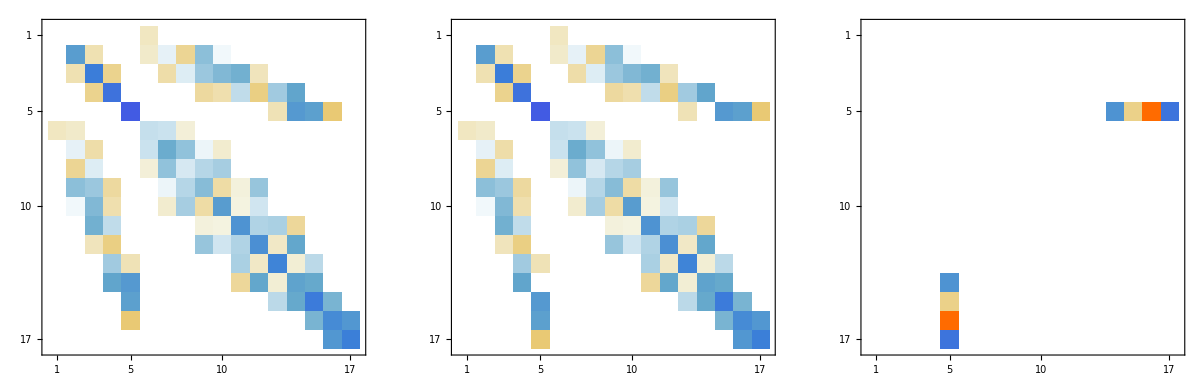
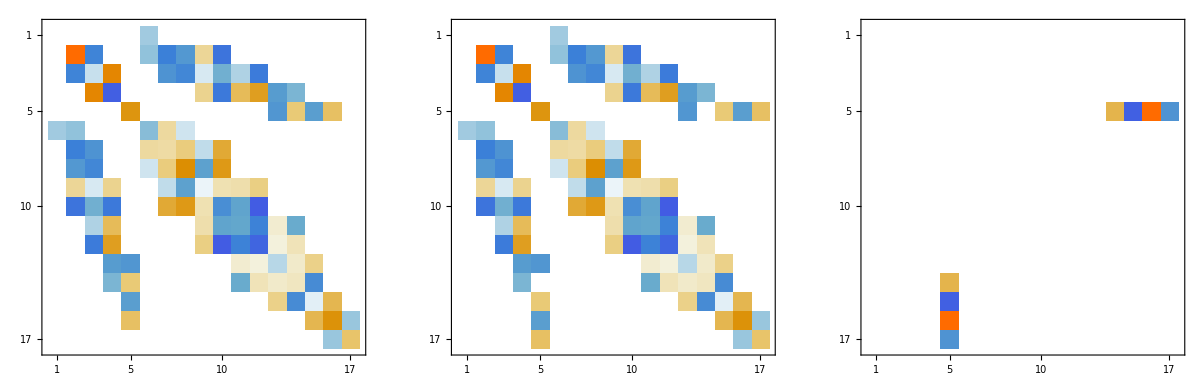
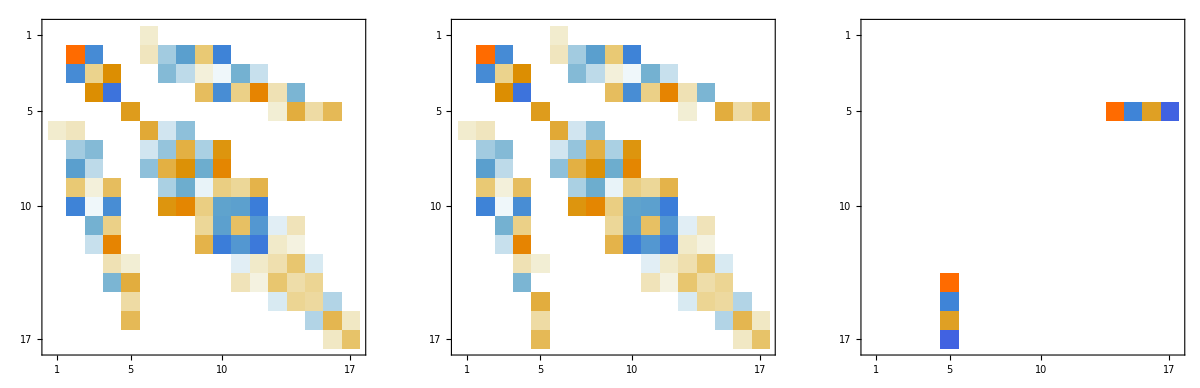
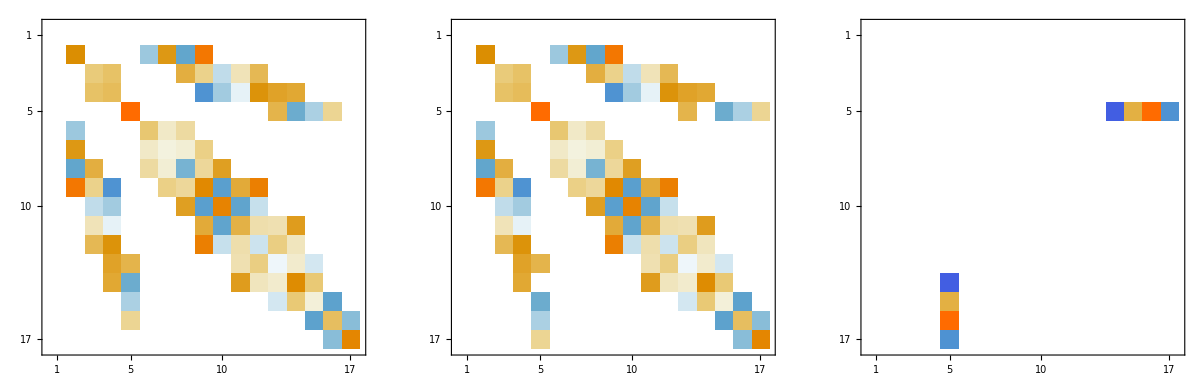
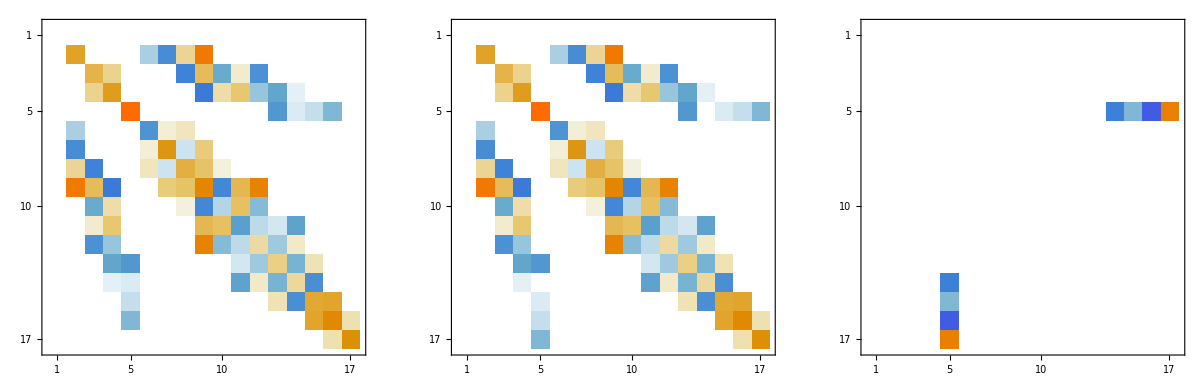
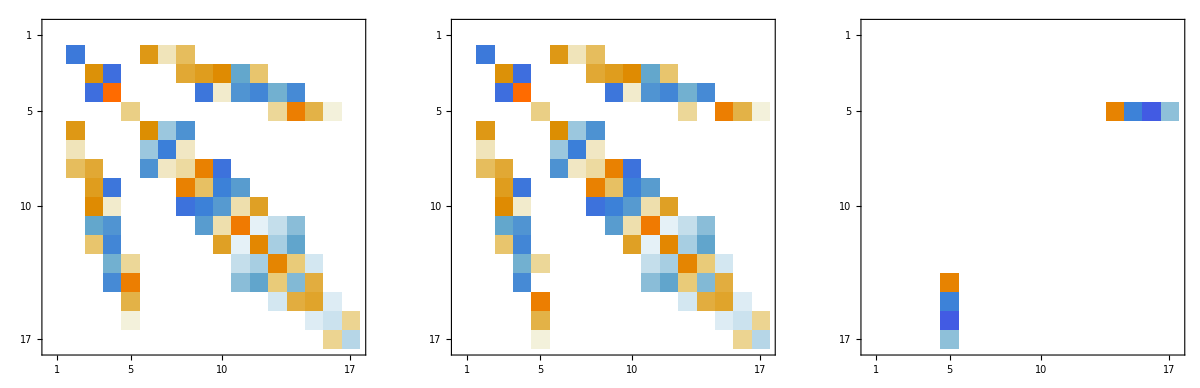
-Graphics-{M0,0.930102}
-Graphics-{M2,0.961892}
-Graphics-{M4,0.988961}
-Graphics-{P2,0.973619}
-Graphics-{P4,0.99575}
-Graphics-{P6,0.957749}

```mathematica
big=Column[rows]
```

```mathematica
Rasterize[big]
```

-Graphics-

```mathematica
plots=Table[(
PrintTemporary[numElectrons];
configTerms=fncross[["terms"]][numElectrons];
matrixReps=<||>;
Do[
(
magElements=fncross[["MKPK"]][op];
magKeys=Keys[magElements];
tab=Table[
(
val=If[MemberQ[magKeys,{numElectrons,braT,ketT}],
magElements[{numElectrons,braT,ketT}],
0
];
If[MemberQ[magKeys,{numElectrons,ketT,braT}],
val=magElements[{numElectrons,ketT,braT}]
];
val
),{braT,configTerms},{ketT,configTerms}];
matrixReps[op]=tab
),
{op,MsAndPs}];
configTerms=fncrossDef[["terms"]][numElectrons];
matrixRepsDef=<||>;
Do[
(
magElements=fncrossDef[["MKPK"]][op];
magKeys=Keys[magElements];
tab=Table[
(
val=If[MemberQ[magKeys,{numElectrons,braT,ketT}],
magElements[{numElectrons,braT,ketT}],
0
];
If[MemberQ[magKeys,{numElectrons,ketT,braT}],
val=magElements[{numElectrons,ketT,braT}]
];
val
),{braT,configTerms},{ketT,configTerms}];
matrixRepsDef[op]=tab
),
{op,MsAndPs}];

rows=Table[(
m1=matrixReps[op];
m2=matrixRepsDef[op];
v1=Flatten[m1];
v2=Flatten[m2];
dist=(v1.v2)/(Sqrt[v1.v1] * Sqrt[v2.v2]);
Labeled[
GraphicsRow[{
MatrixPlot[m1],
MatrixPlot[m2],
MatrixPlot[m1-m2]
}],
{numElectrons,op,dist}
]
),{op,MsAndPs}];
Rasterize[Column[rows]]
)
,{numElectrons,{2,3,5,7}}];
```

```mathematica
Do[(
fname=FileNameJoin[{"~/Desktop","someplots","diff-f"<>{2,3,5,6}[[i]]<>".png"}];
Export[fname,plots[[i]]];
),{i,1,Length[plots]}]
```

## Crosswhite vs David

```mathematica
AppendTo[$Path,NotebookDirectory[]];
SetDirectory[NotebookDirectory[]];
Get["qlanth.m"]
```

```mathematica
numElectrons=3;
allParams={E0,E1,E3,M0,M2,M4,P2,P4,P6,α,β,γ,ζ,B22,S22,B12,S12,B02,B44,S44,B34,S34,B24,S24,B14,S14,B04,B66,S66,B56,S56,B46,S46,B36,S36,B26,S26,B16,S16,B06,E2,T6,T7,T8,T11,T12,T14,T15,T16,T17,T18,T19,T2,T3,T4};
singleSymbol=α;
deletor=(#->0)&/@Select[allParams,Not[#===singleSymbol]&];
mat=HamMatrixAssembly[numElectrons,0];
mat=ReplaceInSparseArray[mat,deletor];
mat=ReplaceInSparseArray[mat,{singleSymbol->1}];
```

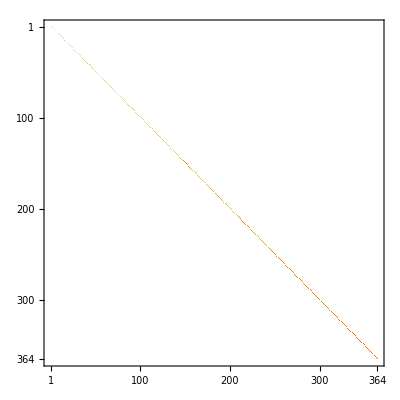

```mathematica
MatrixPlot[mat]
```

```mathematica
1/2 (-1+√(1+4#))&/@DeleteDuplicates[Sort[Eigenvalues[mat]]]
```

{0,1,2,3,4,5,6,7,8}

```mathematica
terms=StringSplit["4S 4D 4F 4G 4I 2P 2D1 2D2 2F1 2F2 2G1 2G2 2H1 2H2 2I 2K 2L"," "];
SLterms=findSL/@terms;
SLterms=SortBy[SLterms,Last];
```

```mathematica
rmat=Table[Tooltip[TwoBodyNKSL[bt,kt],{bt,kt}]/.{β->0,γ->0,α->α},{bt,terms},{kt,terms}];
rmat=Table[TwoBodyNKSL[bt,kt]/.{β->0,γ->0,α->1},{bt,terms},{kt,terms}];
```

```mathematica
1/2 (-1+√(1+4#))&/@Sort[DeleteDuplicates[Diagonal[rmat]]]
```

{0,1,2,3,4,5,6,7,8}

```mathematica
1/2 (-1+√(1+4#))&/@Sort[DeleteDuplicates[Diagonal[rmat]]]
```

{0,1,2,3,4,5,6,7,8}

```mathematica
1/2 (-1+√(1+4#))&/@DeleteDuplicates[Sort[Eigenvalues[rmat]]]
```

{0,1,1/2 (-1+√73),1/2 (-1+√145),7,1/2 (-1+√241),8,1/2 (-1+√337)}

```mathematica
findSL["2L"]
```

{1/2,8}

```mathematica
8*9
```

72

```mathematica
findSL["3P"]
```

{1,1}

```mathematica
Diagonal[mat]//Normal
```

{2,0,2,2,2,2,2,2,2,2,12,12,12,12,12,6,6,6,6,6,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,30,30,30,30,30,30,30,30,30,20,20,20,20,20,20,20,20,20,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,42,42,42,42,42,42,42,42,42,42,42,42,42}

```mathematica
Solve[y(y+1)==x,y]
```

{{y→1/2 (-1-√(1+4 x))},{y→1/2 (-1+√(1+4 x))}}

```mathematica
1/2 (-1+√(1+4#))&/@{0,2,6,12,20,30,42,56,72}
```

{0,1,2,3,4,5,6,7,8}

```mathematica
-1/2 (-1-√(1+4#))&/@{2,6,12,18,20,36,42,56,60,72}
```

{2,3,4,1/2 (1+√73),5,1/2 (1+√145),7,8,1/2 (1+√241),9}

```mathematica
Sort[DeleteDuplicates[Eigenvalues[mat]]]
```

{0,6,12,18,20,42,60,72,80,90,110,112,120,126,160,168,180,216,252}

```mathematica
Sort[DeleteDuplicates[Diagonal[Normal[mat]/.{α->1}]]]
```

{0,2,6,12,20,30,42,56,72}

```mathematica
Table[i*(i+1),{i,1,10,1}]
```

{2,6,12,20,30,42,56,72,90,110}

```mathematica
ReplaceInSparseArray[mat,{}]
```

```mathematica
DeleteDuplicates[Flatten[Variables/@Flatten[Normal[mat]]]]
```

{E0,E1,E3,M0,M2,M4,P2,P4,P6,α,β,γ,ζ,B22,S22,B12,S12,B02,B44,S44,B34,S34,B24,S24,B14,S14,B04,B66,S66,B56,S56,B46,S46,B36,S36,B26,S26,B16,S16,B06,E2}

```mathematica
Flatten[mat]
```